### Casually testing new ratio normalization function

```mathematica
ratioNormalize5[list_,pos_ :4]:=Map[(#/#[[pos]])&,list,-2]
```

```mathematica
matrix1={{1,2,3,4},{2,1,7,3},{1,6,9,3}}
```

{{1,2,3,4},{2,1,7,3},{1,6,9,3}}

```mathematica
ratioNormalize5[matrix1,2]
```

{{1/2,1,3/2,2},{2,1,7,3},{1/6,1,3/2,1/2}}

```mathematica
(*Excellent. Now let's try with some real data.*)
```

```mathematica
imported=Import["/Users/themarchhare/Documents/GitHub/Wolfram-Summer-School-2018/Project/Table of Aouidate data.xlsx"]
```

{{{logMU,ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,n,γ,D,logP,},{2.72,−82328.726,7.374,−5.682,5.522,−0.160,3.242,0.046,−0.707,274.154,1.54,37.9,1.324,2.455,},{1.96,−30241.000,7.125,−5.428,5.258,−0.170,1.996,0.135,−0.708,255.376,1.545,42.6,1.08,2.452,},{2.02,−19406.400,6.731,−5.029,5.302,0.273,1.234,0.126,−0.712,223.311,1.509,33.9,0.998,2.778,},{1.95,−20476.100,6.724,−5.037,5.295,0.258,1.283,0.126,−0.709,237.338,1.507,33.9,0.998,3.307,},{1.9,−18336.700,6.765,−5.009,5.282,0.273,1.117,0.127,−0.710,209.285,1.511,34.2,1.01,2.249,},{1.71,−31310.656,7.238,−4.780,5.066,0.286,2.498,−0.150,−0.712,269.403,1.539,41.2,1.07,2.761,},{1.69,−86156.656,7.374,−5.687,5.527,−0.160,3.271,0.046,−0.709,260.128,1.548,39.5,1.368,2.146,},{1.68,−21545.885,6.721,−5.025,5.3,0.275,1.25,0.122,−0.713,251.365,1.504,33.9,0.979,3.386,},{1.66,−29171.207,7.121,−5.453,5.295,−0.158,2.115,−0.131,−0.707,241.35,1.55,43.1,1.1,1.923,},{1.36,−29171.025,6.993,−5.327,5.234,−0.093,4.017,−0.219,−0.713,241.35,1.552,44.2,1.1,1.743,},{1.33,−20382.821,6.83,−5.101,5.576,0.475,3.159,0.349,−0.713,225.284,1.507,34.3,1.048,1.392,},{1.25,−18336.601,6.802,−5.024,5.301,0.278,1.323,0.125,−0.716,209.285,1.514,34.9,1.012,2.469,},{1.29,−30240.922,7.156,−5.333,5.236,−0.097,4.084,−0.220,−0.707,255.376,1.547,43.6,1.09,2.272,},{1.27,−17266.813,8.353,−5.142,5.451,0.309,1.618,0.133,−0.714,195.258,1.516,35.3,1.026,1.94,},{1.14,−22396.415,7.075,−5.349,5.755,0.407,1.297,0.273,−0.713,239.268,1.54,43.5,1.184,1.644,},{1.36,−21452.636,6.803,−5.073,5.531,0.458,3.234,0.353,−0.707,239.311,1.504,34.3,1.034,1.921,},{1.11,−28101.400,7.292,−5.423,5.335,−0.088,4.378,−0.223,−0.708,227.323,1.559,45.,1.12,1.214,},{1.,−19280.462,7.265,−5.393,5.876,0.483,1.539,0.326,−0.707,209.242,1.55,45.4,1.175,1.699,},{1.05,−21452.636,7.265,−5.505,5.911,0.406,3.041,0.265,−0.713,239.311,1.504,34.3,1.034,1.571,},{1.,−19280.543,6.803,−4.968,5.226,0.258,1.505,0.326,−0.715,209.242,1.55,45.4,1.175,1.699,},{1.38,−22522.370,6.911,−5.063,5.528,0.465,3.276,0.352,−0.713,253.337,1.502,34.2,1.022,2.45,},{0.87,−20382.821,7.265,−5.505,5.908,0.403,3.089,0.225,−0.714,225.284,1.508,35.2,1.05,1.262,},{0.86,−23498.638,7.374,−5.703,5.961,0.257,1.288,0.269,−0.714,255.31,1.503,34.,1.069,0.637,},{0.83,−21452.500,7.183,−5.443,5.831,0.389,2.994,0.264,−0.714,239.311,1.506,35.1,1.036,−1.842,},{0.84,−29171.025,7.129,−5.499,5.468,−0.030,3.92,0.293,−0.712,241.35,1.552,44.2,1.1,1.248,},{0.84,−29171.025,7.102,−5.569,5.499,−0.070,3.714,0.289,−0.708,241.35,1.552,44.2,1.1,−1.003,},{0.81,−28101.400,7.319,−5.536,5.488,−0.049,4.009,0.293,−0.702,227.323,1.559,45.,1.12,0.719,},{0.76,−22396.388,7.02,−5.281,5.594,0.313,0.427,0.283,−0.702,239.268,1.54,43.5,1.184,1.294,},{0.66,−29171.025,7.047,−5.407,5.332,−0.075,4.42,−0.226,−0.705,241.35,1.552,44.2,1.1,1.743,},{0.68,−30240.922,7.02,−5.303,5.221,−0.082,4.043,−0.222,−0.713,255.376,1.547,43.6,1.09,2.272,},{0.67,−17266.922,7.047,−5.243,5.765,0.522,2.553,0.378,−0.713,195.258,1.512,34.7,1.023,−1.265,},{0.59,−12104.477,7.809,−5.971,6.34,0.37,1.567,0.179,−0.707,149.233,1.525,35.2,0.938,2.241,},{0.58,−31310.547,7.02,−5.311,5.224,−0.088,4.067,−0.219,−0.712,269.403,1.543,43.1,1.07,2.801,},{0.46,−26669.745,7.238,−5.590,5.669,0.079,3.375,0.267,−0.712,301.38,1.555,39.8,1.093,2.81,},{0.43,−19280.462,7.211,−5.328,5.872,0.544,1.369,0.265,−0.713,209.242,1.55,45.4,1.175,1.699,},{0.41,−16164.481,7.211,−5.293,5.602,0.309,1.899,0.329,−0.708,179.216,1.564,48.,1.163,1.707,},{0.38,−22522.234,7.156,−5.435,5.827,0.391,2.947,0.265,−0.713,253.337,1.503,35.,1.023,1.777,},{0.38,−30240.922,7.02,−5.247,5.533,0.286,3.05,0.3,−0.711,255.376,1.547,43.6,1.09,1.777,},{0.38,−30240.922,7.156,−5.533,5.466,−0.067,3.751,0.285,−0.710,255.376,1.547,43.6,1.09,1.777,},{0.33,−20382.766,7.319,−5.524,5.912,0.388,3.136,0.245,−0.719,225.284,1.507,34.3,1.048,1.042,},{0.23,−21452.609,7.129,−5.410,5.794,0.384,2.979,0.26,−0.713,239.311,1.506,35.1,1.036,1.273,},{0.03,−20382.739,7.238,−5.481,5.872,0.39,3.237,0.249,−0.713,225.284,1.508,35.2,1.05,0.744,},{0.,−19312.923,7.319,−5.523,5.914,0.391,3.203,0.253,−0.707,211.258,1.511,35.4,1.067,0.215,},{−0.030,−19312.787,7.456,−5.719,6.007,0.288,1.449,0.305,−0.710,211.258,1.511,35.4,1.067,−3.080,},{−0.060,−17266.759,7.292,−5.444,5.849,0.405,3.673,0.308,−0.717,195.258,1.512,34.7,1.023,0.435,},{−0.670,−16196.943,7.292,−5.443,5.848,0.406,3.724,0.307,−0.713,181.232,1.517,36.,1.041,0.126,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,}},{{Compd,W,J,Sz,MTD1,sMTD,E,MR,LogP},{1.,522.,2.6008,720.,1.,2.,33.263,64.97,2.34},{2.,718.,2.6522,982.,2.,3.,35.515,74.23,2.46},{3.,611.,2.6443,842.,2.,3.,34.013,74.23,2.34},{4.,718.,2.6522,982.,2.,3.,35.106,66.83,2.87},{5.,522.,2.6008,720.,1.,2.,32.513,64.97,1.82},{6.,827.,2.6844,1124.,2.,4.,36.393,62.11,3.16},{7.,453.,2.5035,633.,2.,3.,31.43,78.84,2.05},{8.,844.,2.6349,1141.,2.,3.,35.18,60.38,3.41},{9.,611.,2.6443,842.,2.,3.,34.346,76.1,1.92},{10.,632.,2.5678,872.,4.,4.,34.037,69.6,2.19},{11.,611.,2.6443,842.,2.,3.,36.013,74.23,1.43},{12.,534.,2.555,744.,3.,4.,32.18,63.96,2.04},{13.,746.,2.5627,1014.,4.,4.,35.513,62.24,2.73},{14.,453.,2.5035,633.,2.,3.,30.68,74.26,1.52},{15.,669.,2.0781,950.,2.,1.,38.683,57.51,0.24},{16.,718.,2.6522,982.,2.,3.,37.565,63.44,1.92},{17.,536.,2.5432,748.,5.,4.,32.513,68.59,1.65},{18.,507.,1.9685,722.,4.,3.,33.513,65.,0.77},{19.,720.,2.6419,986.,4.,3.,37.513,80.73,1.58},{20.,513.,1.9417,734.,3.,4.,33.513,68.59,1.11},{21.,844.,2.6349,1141.,2.,3.,39.013,56.76,2.45},{22.,632.,2.5678,872.,4.,4.,35.68,73.23,1.28},{23.,776.,2.8727,1065.,3.,2.,41.183,64.,0.56},{24.,746.,2.5627,1014.,4.,4.,37.18,70.64,1.82},{25.,629.,2.5777,866.,4.,3.,34.013,68.63,2.28},{26.,632.,2.5678,872.,4.,4.,34.013,69.63,2.22},{27.,536.,2.5432,748.,5.,4.,32.513,69.63,1.74},{28.,667.,2.0816,946.,4.,3.,38.683,65.,0.24},{29.,629.,2.5777,866.,5.,5.,34.013,63.44,2.13},{30.,732.,2.6112,998.,4.,5.,35.513,69.63,2.67},{31.,458.,2.4644,631.,4.,5.,30.843,74.26,1.4},{32.,337.,2.2157,472.,5.,6.,25.673,57.28,1.59},{33.,879.,2.5373,1175.,4.,5.,37.013,50.6,3.26},{34.,434.,1.8958,2044.,5.,4.,47.183,78.89,2.7},{35.,519.,1.9189,746.,5.,4.,33.513,93.08,0.77},{36.,381.,1.7972,554.,5.,4.,28.343,61.4,1.49},{37.,879.,2.5373,1175.,4.,5.,38.68,50.09,2.36},{38.,732.,2.6112,998.,4.,5.,35.513,73.27,2.77},{39.,732.,2.6112,998.,4.,5.,35.513,74.26,2.71},{40.,615.,2.6224,850.,4.,3.,36.013,74.26,1.09},{41.,732.,2.6112,998.,4.,5.,37.18,63.96,1.77},{42.,629.,2.5777,866.,5.,5.,35.68,68.63,1.28},{43.,536.,2.5432,748.,5.,4.,34.18,64.,0.8},{44.,526.,2.5996,728.,6.,5.,34.18,59.37,0.8},{45.,466.,2.4125,647.,6.,5.,30.843,59.37,1.63},{46.,400.,2.3204,562.,7.,6.,29.01,57.28,1.33}},{{Column # in Mathematica -->,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,-1.,,,,,,,,,,,,,,},{Variable Name -->,ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,γ,D,logP,logMU,From DFT,,,η,logMU,,,,,,,,DM,logMU},{Pearson's correlation with logUM  -->,-0.445075,-0.264673,0.37217,-0.577815,-0.333557,-0.259118,-0.352955,0.196377,0.342209,-0.0293615,0.199581,0.531941,1.,,,,5.522,2.72,,,,,,,,3.242,2.72},{Actual data for 46 cmpds -->,−82328.726,7.374,−5.682,5.522,−0.160,3.242,0.046,−0.707,274.154,37.9,1.324,2.455,2.72,From DFT but could be calculated another way,,,5.258,1.96,,,,,,,,1.996,1.96},{,−30241.000,7.125,−5.428,5.258,−0.170,1.996,0.135,−0.708,255.376,42.6,1.08,2.452,1.96,Physicochemical,,,5.302,2.02,,,,,,,,1.234,2.02},{,−19406.400,6.731,−5.029,5.302,0.273,1.234,0.126,−0.712,223.311,33.9,0.998,2.778,2.02,Biochemical activity, response variable,,,5.295,1.95,,,,,,,,1.283,1.95},{,−20476.100,6.724,−5.037,5.295,0.258,1.283,0.126,−0.709,237.338,33.9,0.998,3.307,1.95,,,,5.282,1.9,,,,,,,,1.117,1.9},{,−18336.700,6.765,−5.009,5.282,0.273,1.117,0.127,−0.710,209.285,34.2,1.01,2.249,1.9,,,,5.066,1.71,,,,,,,,2.498,1.71},{,−31310.656,7.238,−4.780,5.066,0.286,2.498,−0.150,−0.712,269.403,41.2,1.07,2.761,1.71,,,,5.527,1.69,,,,,,,,3.271,1.69},{,−86156.656,7.374,−5.687,5.527,−0.160,3.271,0.046,−0.709,260.128,39.5,1.368,2.146,1.69,,,,5.3,1.68,,,,,,,,1.25,1.68},{,−21545.885,6.721,−5.025,5.3,0.275,1.25,0.122,−0.713,251.365,33.9,0.979,3.386,1.68,,,,5.295,1.66,,,,,,,,2.115,1.66},{,−29171.207,7.121,−5.453,5.295,−0.158,2.115,−0.131,−0.707,241.35,43.1,1.1,1.923,1.66,,,,5.234,1.36,,,,,,,,4.017,1.36},{,−29171.025,6.993,−5.327,5.234,−0.093,4.017,−0.219,−0.713,241.35,44.2,1.1,1.743,1.36,,,,5.576,1.33,,,,,,,,3.159,1.33},{,−20382.821,6.83,−5.101,5.576,0.475,3.159,0.349,−0.713,225.284,34.3,1.048,1.392,1.33,,,,5.301,1.25,,,,,,,,1.323,1.25},{,−18336.601,6.802,−5.024,5.301,0.278,1.323,0.125,−0.716,209.285,34.9,1.012,2.469,1.25,,,,5.236,1.29,,,,,,,,4.084,1.29},{,−30240.922,7.156,−5.333,5.236,−0.097,4.084,−0.220,−0.707,255.376,43.6,1.09,2.272,1.29,,,,5.451,1.27,,,,,,,,1.618,1.27},{,−17266.813,8.353,−5.142,5.451,0.309,1.618,0.133,−0.714,195.258,35.3,1.026,1.94,1.27,,,,5.755,1.14,,,,,,,,1.297,1.14},{,−22396.415,7.075,−5.349,5.755,0.407,1.297,0.273,−0.713,239.268,43.5,1.184,1.644,1.14,,,,5.531,1.36,,,,,,,,3.234,1.36},{,−21452.636,6.803,−5.073,5.531,0.458,3.234,0.353,−0.707,239.311,34.3,1.034,1.921,1.36,,,,5.335,1.11,,,,,,,,4.378,1.11},{,−28101.400,7.292,−5.423,5.335,−0.088,4.378,−0.223,−0.708,227.323,45.,1.12,1.214,1.11,,,,5.876,1.,,,,,,,,1.539,1.},{,−19280.462,7.265,−5.393,5.876,0.483,1.539,0.326,−0.707,209.242,45.4,1.175,1.699,1.,,,,5.911,1.05,,,,,,,,3.041,1.05},{,−21452.636,7.265,−5.505,5.911,0.406,3.041,0.265,−0.713,239.311,34.3,1.034,1.571,1.05,,,,5.226,1.,,,,,,,,1.505,1.},{,−19280.543,6.803,−4.968,5.226,0.258,1.505,0.326,−0.715,209.242,45.4,1.175,1.699,1.,,,,5.528,1.38,,,,,,,,3.276,1.38},{,−22522.370,6.911,−5.063,5.528,0.465,3.276,0.352,−0.713,253.337,34.2,1.022,2.45,1.38,,,,5.908,0.87,,,,,,,,3.089,0.87},{,−20382.821,7.265,−5.505,5.908,0.403,3.089,0.225,−0.714,225.284,35.2,1.05,1.262,0.87,,,,5.961,0.86,,,,,,,,1.288,0.86},{,−23498.638,7.374,−5.703,5.961,0.257,1.288,0.269,−0.714,255.31,34.,1.069,0.637,0.86,,,,5.831,0.83,,,,,,,,2.994,0.83},{,−21452.500,7.183,−5.443,5.831,0.389,2.994,0.264,−0.714,239.311,35.1,1.036,−1.842,0.83,,,,5.468,0.84,,,,,,,,3.92,0.84},{,−29171.025,7.129,−5.499,5.468,−0.030,3.92,0.293,−0.712,241.35,44.2,1.1,1.248,0.84,,,,5.499,0.84,,,,,,,,3.714,0.84},{,−29171.025,7.102,−5.569,5.499,−0.070,3.714,0.289,−0.708,241.35,44.2,1.1,−1.003,0.84,,,,5.488,0.81,,,,,,,,4.009,0.81},{,−28101.400,7.319,−5.536,5.488,−0.049,4.009,0.293,−0.702,227.323,45.,1.12,0.719,0.81,,,,5.594,0.76,,,,,,,,0.427,0.76},{,−22396.388,7.02,−5.281,5.594,0.313,0.427,0.283,−0.702,239.268,43.5,1.184,1.294,0.76,,,,5.332,0.66,,,,,,,,4.42,0.66},{,−29171.025,7.047,−5.407,5.332,−0.075,4.42,−0.226,−0.705,241.35,44.2,1.1,1.743,0.66,,,,5.221,0.68,,,,,,,,4.043,0.68},{,−30240.922,7.02,−5.303,5.221,−0.082,4.043,−0.222,−0.713,255.376,43.6,1.09,2.272,0.68,,,,5.765,0.67,,,,,,,,2.553,0.67},{,−17266.922,7.047,−5.243,5.765,0.522,2.553,0.378,−0.713,195.258,34.7,1.023,−1.265,0.67,,,,6.34,0.59,,,,,,,,1.567,0.59},{,−12104.477,7.809,−5.971,6.34,0.37,1.567,0.179,−0.707,149.233,35.2,0.938,2.241,0.59,,,,5.224,0.58,,,,,,,,4.067,0.58},{,−31310.547,7.02,−5.311,5.224,−0.088,4.067,−0.219,−0.712,269.403,43.1,1.07,2.801,0.58,,,,5.669,0.46,,,,,,,,3.375,0.46},{,−26669.745,7.238,−5.590,5.669,0.079,3.375,0.267,−0.712,301.38,39.8,1.093,2.81,0.46,,,,5.872,0.43,,,,,,,,1.369,0.43},{,−19280.462,7.211,−5.328,5.872,0.544,1.369,0.265,−0.713,209.242,45.4,1.175,1.699,0.43,,,,5.602,0.41,,,,,,,,1.899,0.41},{,−16164.481,7.211,−5.293,5.602,0.309,1.899,0.329,−0.708,179.216,48.,1.163,1.707,0.41,,,,5.827,0.38,,,,,,,,2.947,0.38},{,−22522.234,7.156,−5.435,5.827,0.391,2.947,0.265,−0.713,253.337,35.,1.023,1.777,0.38,,,,5.533,0.38,,,,,,,,3.05,0.38},{,−30240.922,7.02,−5.247,5.533,0.286,3.05,0.3,−0.711,255.376,43.6,1.09,1.777,0.38,,,,5.466,0.38,,,,,,,,3.751,0.38},{,−30240.922,7.156,−5.533,5.466,−0.067,3.751,0.285,−0.710,255.376,43.6,1.09,1.777,0.38,,,,5.912,0.33,,,,,,,,3.136,0.33},{,−20382.766,7.319,−5.524,5.912,0.388,3.136,0.245,−0.719,225.284,34.3,1.048,1.042,0.33,,,,5.794,0.23,,,,,,,,2.979,0.23},{,−21452.609,7.129,−5.410,5.794,0.384,2.979,0.26,−0.713,239.311,35.1,1.036,1.273,0.23,,,,5.872,0.03,,,,,,,,3.237,0.03},{,−20382.739,7.238,−5.481,5.872,0.39,3.237,0.249,−0.713,225.284,35.2,1.05,0.744,0.03,,,,5.914,0.,,,,,,,,3.203,0.},{,−19312.923,7.319,−5.523,5.914,0.391,3.203,0.253,−0.707,211.258,35.4,1.067,0.215,0.,,,,6.007,−0.030,,,,,,,,1.449,−0.030},{,−19312.787,7.456,−5.719,6.007,0.288,1.449,0.305,−0.710,211.258,35.4,1.067,−3.080,−0.030,,,,5.849,−0.060,,,,,,,,3.673,−0.060},{,−17266.759,7.292,−5.444,5.849,0.405,3.673,0.308,−0.717,195.258,34.7,1.023,0.435,−0.060,,,,5.848,−0.670,,,,,,,,3.724,−0.670},{,−16196.943,7.292,−5.443,5.848,0.406,3.724,0.307,−0.713,181.232,36.,1.041,0.126,−0.670,,,,,,,,,,,,,,}},{{,logMU,cLogP,Solubility,TPSA,Druglikeness,Dipole moment from Millsian,,Druglikeness,logMU,,,,,,,,TPSA,logMU,,,,,,,,cLogP,logMU,,,,,,,cLogP,Solubility,,,,,,,Solubility,logMU,,,,,Dipole moment from Millsian,logMU,,,,,,,Dipole moment from Millsian,DM from DFT,,},{1.,2.72,2.04,-2.94,44.48,-2.1,2.8154,,-2.1,2.72,,,,,,,,44.48,2.72,,,,,,,,2.04,2.72,,,,,,,2.04,-2.94,,,,,,,-2.94,2.72,,,,,2.8154,2.72,,,,,,,2.8154,3.242,,},{2.,1.96,2.29,-3.18,69.78,0.19,2.2187,,0.19,1.96,,,,,,,,69.78,1.96,,,,,,,,2.29,1.96,,,,,,,2.29,-3.18,,,,,,,-3.18,1.96,,,,,2.2187,1.96,,,,,,,2.2187,1.996,,},{3.,2.02,2.07,-2.61,44.48,-0.47,2.4151,,-0.47,2.02,,,,,,,,44.48,2.02,,,,,,,,2.07,2.02,,,,,,,2.07,-2.61,,,,,,,-2.61,2.02,,,,,2.4151,2.02,,,,,,,2.4151,1.234,,},{4.,1.95,2.53,-2.88,44.48,-2.43,2.4073,,-2.43,1.95,,,,,,,,44.48,1.95,,,,,,,,2.53,1.95,,,,,,,2.53,-2.88,,,,,,,-2.88,1.95,,,,,2.4073,1.95,,,,,,,2.4073,1.283,,},{5.,1.9,1.66,-2.45,44.48,-0.31,2.3756,,-0.31,1.9,,,,,,,,44.48,1.9,,,,,,,,1.66,1.9,,,,,,,1.66,-2.45,,,,,,,-2.45,1.9,,,,,2.3756,1.9,,,,,,,2.3756,1.117,,},{6.,1.71,2.69,-3.38,69.78,0.86,3.9221,,0.86,1.71,,,,,,,,69.78,1.71,,,,,,,,2.69,1.71,,,,,,,2.69,-3.38,,,,,,,-3.38,1.71,,,,,3.9221,1.71,,,,,,,3.9221,2.498,,},{7.,1.69,1.68,-2.56,44.48,-2.71,2.7816,,-2.71,1.69,,,,,,,,44.48,1.69,,,,,,,,1.68,1.69,,,,,,,1.68,-2.56,,,,,,,-2.56,1.69,,,,,2.7816,1.69,,,,,,,2.7816,3.271,,},{8.,1.68,2.98,-3.14,44.48,-5.7,2.2935,,-5.7,1.68,,,,,,,,44.48,1.68,,,,,,,,2.98,1.68,,,,,,,2.98,-3.14,,,,,,,-3.14,1.68,,,,,2.2935,1.68,,,,,,,2.2935,1.25,,},{9.,1.66,1.79,-2.95,69.78,0.01,3.8763,,0.01,1.66,,,,,,,,69.78,1.66,,,,,,,,1.79,1.66,,,,,,,1.79,-2.95,,,,,,,-2.95,1.66,,,,,3.8763,1.66,,,,,,,3.8763,2.115,,},{10.,1.36,1.93,-2.8,69.78,1.48,3.5554,,1.48,1.36,,,,,,,,69.78,1.36,,,,,,,,1.93,1.36,,,,,,,1.93,-2.8,,,,,,,-2.8,1.36,,,,,3.5554,1.36,,,,,,,3.5554,4.017,,},{11.,1.33,1.24,-2.12,53.71,0.68,3.7961,,0.68,1.33,,,,,,,,53.71,1.33,,,,,,,,1.24,1.33,,,,,,,1.24,-2.12,,,,,,,-2.12,1.33,,,,,3.7961,1.33,,,,,,,3.7961,3.159,,},{12.,1.25,1.71,-2.23,44.48,-1.08,1.3017,,-1.08,1.25,,,,,,,,44.48,1.25,,,,,,,,1.71,1.25,,,,,,,1.71,-2.23,,,,,,,-2.23,1.25,,,,,1.3017,1.25,,,,,,,1.3017,1.323,,},{13.,1.29,2.38,-3.07,69.78,1.43,3.5394,,1.43,1.29,,,,,,,,69.78,1.29,,,,,,,,2.38,1.29,,,,,,,2.38,-3.07,,,,,,,-3.07,1.29,,,,,3.5394,1.29,,,,,,,3.5394,4.084,,},{14.,1.27,1.3,-2.07,44.48,-0.92,1.2589,,-0.92,1.27,,,,,,,,44.48,1.27,,,,,,,,1.3,1.27,,,,,,,1.3,-2.07,,,,,,,-2.07,1.27,,,,,1.2589,1.27,,,,,,,1.2589,1.618,,},{15.,1.14,1.43,-2.81,62.94,-1.15,1.3148,,-1.15,1.14,,,,,,,,62.94,1.14,,,,,,,,1.43,1.14,,,,,,,1.43,-2.81,,,,,,,-2.81,1.14,,,,,1.3148,1.14,,,,,,,1.3148,1.297,,},{16.,1.36,1.65,-2.42,53.71,-1.63,3.5769,,-1.63,1.36,,^bwahahahaha,,,,,,53.71,1.36,,,,,,,,1.65,1.36,,,,,,,1.65,-2.42,,,,,,,-2.42,1.36,,,,,3.5769,1.36,,,,,,,3.5769,3.234,,},{17.,1.11,1.43,-2.57,69.78,1.33,3.5557,,1.33,1.11,,,,,,,,69.78,1.11,,,,,,,,1.43,1.11,,,,,,,1.43,-2.57,,,,,,,-2.57,1.11,,,,,3.5557,1.11,,,,,,,3.5557,4.378,,},{18.,1.,1.5,-2.8,53.71,-0.45,2.5885,,-0.45,1.,,,,,,,,53.71,1.,,,,,,,,1.5,1.,,,,,,,1.5,-2.8,,,,,,,-2.8,1.,,,,,2.5885,1.,,,,,,,2.5885,1.539,,},{19.,1.05,1.65,-2.42,53.71,0.43,2.9286,,0.43,1.05,,,,,,,,53.71,1.05,,,,,,,,1.65,1.05,,,,,,,1.65,-2.42,,,,,,,-2.42,1.05,,,,,2.9286,1.05,,,,,,,2.9286,3.041,,},{20.,1.,1.5,-2.79,53.71,-0.56,2.065,,-0.56,1.,,,,,,,,53.71,1.,,,,,,,,1.5,1.,,,,,,,1.5,-2.79,,,,,,,-2.79,1.,,,,,2.065,1.,,,,,,,2.065,1.505,,},{21.,1.38,2.1,-2.69,53.71,-0.53,3.6099,,-0.53,1.38,,,,,,,,53.71,1.38,,,,,,,,2.1,1.38,,,,,,,2.1,-2.69,,,,,,,-2.69,1.38,,,,,3.6099,1.38,,,,,,,3.6099,3.276,,},{22.,0.87,1.29,-2.04,53.71,-0.04,2.9414,,-0.04,0.87,,,,,,,,53.71,0.87,,,,,,,,1.29,0.87,,,,,,,1.29,-2.04,,,,,,,-2.04,0.87,,,,,2.9414,0.87,,,,,,,2.9414,3.089,,},{23.,0.86,1.17,-2.14,62.94,-1.21,5.1462,Note: "energy minimized" structure has all O methyls cis,-1.21,0.86,,,,,,,,62.94,0.86,,,,,,,,1.17,0.86,,,,,,,1.17,-2.14,,,,,,,-2.14,0.86,,,,,5.1462,0.86,,,,,,,5.1462,1.288,,},{24.,0.83,1.75,-2.31,53.71,1.01,4.9241,,1.01,0.83,,,,,,,,53.71,0.83,,,,,,,,1.75,0.83,,,,,,,1.75,-2.31,,,,,,,-2.31,0.83,,,,,4.9241,0.83,,,,,,,4.9241,2.994,,},{25.,0.84,1.93,-2.8,69.78,2.35,5.1501,,2.35,0.84,,,,,,,,69.78,0.84,,,,,,,,1.93,0.84,,,,,,,1.93,-2.8,,,,,,,-2.8,0.84,,,,,5.1501,0.84,,,,,,,5.1501,3.92,,},{26.,0.84,1.84,-2.87,69.78,-0.78,5.1634,,-0.78,0.84,,,,,,,,69.78,0.84,,,,,,,,1.84,0.84,,,,,,,1.84,-2.87,,,,,,,-2.87,0.84,,,,,5.1634,0.84,,,,,,,5.1634,3.714,,fI00g8DG},{27.,0.81,1.43,-2.57,69.78,2.21,5.1512,,2.21,0.81,,,,,,,,69.78,0.81,,,,,,,,1.43,0.81,,,,,,,1.43,-2.57,,,,,,,-2.57,0.81,,,,,5.1512,0.81,,,,,,,5.1512,4.009,,},{28.,0.76,1.43,-2.81,62.94,-1.15,0.8071,,-1.15,0.76,,,,,,,,62.94,0.76,,,,,,,,1.43,0.76,,,,,,,1.43,-2.81,,,,,,,-2.81,0.76,,,,,0.8071,0.76,,,,,,,0.8071,0.427,,},{29.,0.66,1.84,-2.87,69.78,-1.06,3.5591,,-1.06,0.66,,,,,,,,69.78,0.66,,,,,,,,1.84,0.66,,,,,,,1.84,-2.87,,,,,,,-2.87,0.66,,,,,3.5591,0.66,,,,,,,3.5591,4.42,,},{30.,0.68,2.34,-3.1,69.78,-0.88,3.5628,,-0.88,0.68,,,,,,,,69.78,0.68,,,,,,,,2.34,0.68,,,,,,,2.34,-3.1,,,,,,,-3.1,0.68,,,,,3.5628,0.68,,,,,,,3.5628,4.043,,},{31.,0.67,1.31,-2.1,44.48,-2.,2.87,,-2.,0.67,,,,,,,,44.48,0.67,,,,,,,,1.31,0.67,,,,,,,1.31,-2.1,,,,,,,-2.1,0.67,,,,,2.87,0.67,,,,,,,2.87,2.553,,},{32.,0.59,1.8,-2.41,26.02,-1.75,1.3362,,-1.75,0.59,,,,,,,,26.02,0.59,,,,,,,,1.8,0.59,,,,,,,1.8,-2.41,,,,,,,-2.41,0.59,,,,,1.3362,0.59,,,,,,,1.3362,1.567,,},{33.,0.58,2.84,-3.34,69.78,-0.69,5.2338,,-0.69,0.58,,,,,,,,69.78,0.58,,,,,,,,2.84,0.58,,,,,,,2.84,-3.34,,,,,,,-3.34,0.58,,,,,5.2338,0.58,,,,,,,5.2338,4.067,,},{34.,0.46,2.66,-3.44,53.71,-3.54,4.8593,,-3.54,0.46,,,,,,,,53.71,0.46,,,,,,,,2.66,0.46,,,,,,,2.66,-3.44,,,,,,,-3.44,0.46,,,,,4.8593,0.46,,,,,,,4.8593,3.375,,},{35.,0.43,1.5,-2.79,53.71,0.81,2.8125,,0.81,0.43,,,,,,,,53.71,0.43,,,,,,,,1.5,0.43,,,,,,,1.5,-2.79,,,,,,,-2.79,0.43,,,,,2.8125,0.43,,,,,,,2.8125,1.369,,},{36.,0.41,1.57,-2.78,44.48,0.11,1.3784,,0.11,0.41,,,,,,,,44.48,0.41,,,,,,,,1.57,0.41,,,,,,,1.57,-2.78,,,,,,,-2.78,0.41,,,,,1.3784,0.41,,,,,,,1.3784,1.899,,},{37.,0.38,2.2,-2.58,53.71,-3.79,4.914,,-3.79,0.38,,,,,,,,53.71,0.38,,,,,,,,2.2,0.38,,,,,,,2.2,-2.58,,,,,,,-2.58,0.38,,,,,4.914,0.38,,,,,,,4.914,2.947,,},{38.,0.38,2.34,-3.1,69.78,-0.6,5.1602,,-0.6,0.38,,,,,,,,69.78,0.38,,,,,,,,2.34,0.38,,,,,,,2.34,-3.1,,,,,,,-3.1,0.38,,,,,5.1602,0.38,,,,,,,5.1602,3.05,,},{39.,0.38,2.24,-3.17,69.78,-2.06,5.1389,,-2.06,0.38,,,,,,,,69.78,0.38,,,,,,,,2.24,0.38,,,,,,,2.24,-3.17,,,,,,,-3.17,0.38,,,,,5.1389,0.38,,,,,,,5.1389,3.751,,},{40.,0.33,1.24,-2.12,53.71,3.93,4.5648,,3.93,0.33,,,,,,,,53.71,0.33,,,,,,,,1.24,0.33,,,,,,,1.24,-2.12,,,,,,,-2.12,0.33,,,,,4.5648,0.33,,,,,,,4.5648,3.136,,},{41.,0.23,1.7,-2.34,53.71,-1.07,2.8654,,-1.07,0.23,,,,,,,,53.71,0.23,,,,,,,,1.7,0.23,,,,,,,1.7,-2.34,,,,,,,-2.34,0.23,,,,,2.8654,0.23,,,,,,,2.8654,2.979,,},{42.,0.03,1.29,-2.04,53.71,0.59,2.8561,,0.59,0.03,,,,,,,,53.71,0.03,,,,,,,,1.29,0.03,,,,,,,1.29,-2.04,,,,,,,-2.04,0.03,,,,,2.8561,0.03,,,,,,,2.8561,3.237,,},{43.,0.,0.88,-1.74,53.71,3.64,2.9357,,3.64,0.,,,,,,,,53.71,0.,,,,,,,,0.88,0.,,,,,,,0.88,-1.74,,,,,,,-1.74,0.,,,,,2.9357,0.,,,,,,,2.9357,3.203,,},{44.,−0.030,0.88,-1.74,53.71,0.01,2.8568,,0.01,−0.030,,,,,,,,53.71,−0.030,,,,,,,,0.88,−0.030,,,,,,,0.88,-1.74,,,,,,,-1.74,−0.030,,,,,2.8568,−0.030,,,,,,,2.8568,1.449,,},{45.,−0.060,1.31,-2.1,44.48,2.81,3.5818,,2.81,−0.060,,,,,,,,44.48,−0.060,,,,,,,,1.31,−0.060,,,,,,,1.31,-2.1,,,,,,,-2.1,−0.060,,,,,3.5818,−0.060,,,,,,,3.5818,3.673,,},{46.,−0.670,0.95,-1.72,44.48,2.43,3.3747,,2.43,−0.670,,,,,,,,44.48,−0.670,,,,,,,,0.95,−0.670,,,,,,,0.95,-1.72,,,,,,,-1.72,−0.670,,,,,3.3747,−0.670,,,,,,,3.3747,3.724,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}}}

```mathematica
originaldata=imported[[1]];
```

```mathematica
data1=ReplaceAll[originaldata,s_String:>ToExpression[s]];
```

```mathematica
<<DataImportandNormalization`
```

```mathematica
data2=deleteZeroRows[data1];
```

```mathematica
data3=deleteZeroColumns[data2]
```

(logMU | ET | IP | EHOMO | η | ELUMO | DM | Qp | Qmin | MW | n | γ | D | logP
2.72 | -82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 3.242 | 0.046 | -0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455
1.96 | -30241. | 7.125 | -5.428 | 5.258 | -0.17 | 1.996 | 0.135 | -0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452
2.02 | -19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 1.234 | 0.126 | -0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778
1.95 | -20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 1.283 | 0.126 | -0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307
1.9 | -18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 1.117 | 0.127 | -0.71 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249
1.71 | -31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | 2.498 | -0.15 | -0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761
1.69 | -86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 3.271 | 0.046 | -0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146
1.68 | -21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 1.25 | 0.122 | -0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386
1.66 | -29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | 2.115 | -0.131 | -0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923
1.36 | -29171. | 6.993 | -5.327 | 5.234 | -0.093 | 4.017 | -0.219 | -0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743
1.33 | -20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 3.159 | 0.349 | -0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392
1.25 | -18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 1.323 | 0.125 | -0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469
1.29 | -30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | 4.084 | -0.22 | -0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272
1.27 | -17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 1.618 | 0.133 | -0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94
1.14 | -22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 1.297 | 0.273 | -0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644
1.36 | -21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 3.234 | 0.353 | -0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921
1.11 | -28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | 4.378 | -0.223 | -0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214
1. | -19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 1.539 | 0.326 | -0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699
1.05 | -21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 3.041 | 0.265 | -0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571
1. | -19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 1.505 | 0.326 | -0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699
1.38 | -22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 3.276 | 0.352 | -0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45
0.87 | -20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 3.089 | 0.225 | -0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262
0.86 | -23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 1.288 | 0.269 | -0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637
0.83 | -21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 2.994 | 0.264 | -0.714 | 239.311 | 1.506 | 35.1 | 1.036 | -1.842
0.84 | -29171. | 7.129 | -5.499 | 5.468 | -0.03 | 3.92 | 0.293 | -0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248
0.84 | -29171. | 7.102 | -5.569 | 5.499 | -0.07 | 3.714 | 0.289 | -0.708 | 241.35 | 1.552 | 44.2 | 1.1 | -1.003
0.81 | -28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 4.009 | 0.293 | -0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719
0.76 | -22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.427 | 0.283 | -0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294
0.66 | -29171. | 7.047 | -5.407 | 5.332 | -0.075 | 4.42 | -0.226 | -0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743
0.68 | -30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | 4.043 | -0.222 | -0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272
0.67 | -17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 2.553 | 0.378 | -0.713 | 195.258 | 1.512 | 34.7 | 1.023 | -1.265
0.59 | -12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 1.567 | 0.179 | -0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241
0.58 | -31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | 4.067 | -0.219 | -0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801
0.46 | -26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 3.375 | 0.267 | -0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81
0.43 | -19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 1.369 | 0.265 | -0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699
0.41 | -16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 1.899 | 0.329 | -0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707
0.38 | -22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 2.947 | 0.265 | -0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777
0.38 | -30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 3.05 | 0.3 | -0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777
0.38 | -30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 3.751 | 0.285 | -0.71 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777
0.33 | -20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 3.136 | 0.245 | -0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042
0.23 | -21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 2.979 | 0.26 | -0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273
0.03 | -20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 3.237 | 0.249 | -0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744
0. | -19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 3.203 | 0.253 | -0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215
-0.03 | -19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 1.449 | 0.305 | -0.71 | 211.258 | 1.511 | 35.4 | 1.067 | -3.08
-0.06 | -17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 3.673 | 0.308 | -0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435
-0.67 | -16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 3.724 | 0.307 | -0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126)

```mathematica
data4=Map[Flatten@{#[[2;;-1]],#[[1]]}&,data3]
```

(ET | IP | EHOMO | η | ELUMO | DM | Qp | Qmin | MW | n | γ | D | logP | logMU
-82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 3.242 | 0.046 | -0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455 | 2.72
-30241. | 7.125 | -5.428 | 5.258 | -0.17 | 1.996 | 0.135 | -0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452 | 1.96
-19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 1.234 | 0.126 | -0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778 | 2.02
-20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 1.283 | 0.126 | -0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307 | 1.95
-18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 1.117 | 0.127 | -0.71 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249 | 1.9
-31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | 2.498 | -0.15 | -0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761 | 1.71
-86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 3.271 | 0.046 | -0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146 | 1.69
-21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 1.25 | 0.122 | -0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386 | 1.68
-29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | 2.115 | -0.131 | -0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923 | 1.66
-29171. | 6.993 | -5.327 | 5.234 | -0.093 | 4.017 | -0.219 | -0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 1.36
-20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 3.159 | 0.349 | -0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392 | 1.33
-18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 1.323 | 0.125 | -0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469 | 1.25
-30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | 4.084 | -0.22 | -0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 1.29
-17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 1.618 | 0.133 | -0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94 | 1.27
-22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 1.297 | 0.273 | -0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644 | 1.14
-21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 3.234 | 0.353 | -0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921 | 1.36
-28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | 4.378 | -0.223 | -0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214 | 1.11
-19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 1.539 | 0.326 | -0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 1.
-21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 3.041 | 0.265 | -0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571 | 1.05
-19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 1.505 | 0.326 | -0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 1.
-22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 3.276 | 0.352 | -0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45 | 1.38
-20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 3.089 | 0.225 | -0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262 | 0.87
-23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 1.288 | 0.269 | -0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637 | 0.86
-21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 2.994 | 0.264 | -0.714 | 239.311 | 1.506 | 35.1 | 1.036 | -1.842 | 0.83
-29171. | 7.129 | -5.499 | 5.468 | -0.03 | 3.92 | 0.293 | -0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248 | 0.84
-29171. | 7.102 | -5.569 | 5.499 | -0.07 | 3.714 | 0.289 | -0.708 | 241.35 | 1.552 | 44.2 | 1.1 | -1.003 | 0.84
-28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 4.009 | 0.293 | -0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719 | 0.81
-22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.427 | 0.283 | -0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294 | 0.76
-29171. | 7.047 | -5.407 | 5.332 | -0.075 | 4.42 | -0.226 | -0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 0.66
-30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | 4.043 | -0.222 | -0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 0.68
-17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 2.553 | 0.378 | -0.713 | 195.258 | 1.512 | 34.7 | 1.023 | -1.265 | 0.67
-12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 1.567 | 0.179 | -0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241 | 0.59
-31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | 4.067 | -0.219 | -0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801 | 0.58
-26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 3.375 | 0.267 | -0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81 | 0.46
-19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 1.369 | 0.265 | -0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 0.43
-16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 1.899 | 0.329 | -0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707 | 0.41
-22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 2.947 | 0.265 | -0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777 | 0.38
-30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 3.05 | 0.3 | -0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 0.38
-30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 3.751 | 0.285 | -0.71 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 0.38
-20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 3.136 | 0.245 | -0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042 | 0.33
-21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 2.979 | 0.26 | -0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273 | 0.23
-20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 3.237 | 0.249 | -0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744 | 0.03
-19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 3.203 | 0.253 | -0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215 | 0.
-19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 1.449 | 0.305 | -0.71 | 211.258 | 1.511 | 35.4 | 1.067 | -3.08 | -0.03
-17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 3.673 | 0.308 | -0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435 | -0.06
-16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 3.724 | 0.307 | -0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126 | -0.67)

```mathematica
{Header,NumericalData}={First@data4,Rest@data4}
```

{{ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,n,γ,D,logP,logMU},(-82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 3.242 | 0.046 | -0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455 | 2.72
-30241. | 7.125 | -5.428 | 5.258 | -0.17 | 1.996 | 0.135 | -0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452 | 1.96
-19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 1.234 | 0.126 | -0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778 | 2.02
-20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 1.283 | 0.126 | -0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307 | 1.95
-18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 1.117 | 0.127 | -0.71 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249 | 1.9
-31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | 2.498 | -0.15 | -0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761 | 1.71
-86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 3.271 | 0.046 | -0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146 | 1.69
-21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 1.25 | 0.122 | -0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386 | 1.68
-29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | 2.115 | -0.131 | -0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923 | 1.66
-29171. | 6.993 | -5.327 | 5.234 | -0.093 | 4.017 | -0.219 | -0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 1.36
-20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 3.159 | 0.349 | -0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392 | 1.33
-18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 1.323 | 0.125 | -0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469 | 1.25
-30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | 4.084 | -0.22 | -0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 1.29
-17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 1.618 | 0.133 | -0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94 | 1.27
-22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 1.297 | 0.273 | -0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644 | 1.14
-21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 3.234 | 0.353 | -0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921 | 1.36
-28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | 4.378 | -0.223 | -0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214 | 1.11
-19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 1.539 | 0.326 | -0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 1.
-21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 3.041 | 0.265 | -0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571 | 1.05
-19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 1.505 | 0.326 | -0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 1.
-22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 3.276 | 0.352 | -0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45 | 1.38
-20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 3.089 | 0.225 | -0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262 | 0.87
-23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 1.288 | 0.269 | -0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637 | 0.86
-21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 2.994 | 0.264 | -0.714 | 239.311 | 1.506 | 35.1 | 1.036 | -1.842 | 0.83
-29171. | 7.129 | -5.499 | 5.468 | -0.03 | 3.92 | 0.293 | -0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248 | 0.84
-29171. | 7.102 | -5.569 | 5.499 | -0.07 | 3.714 | 0.289 | -0.708 | 241.35 | 1.552 | 44.2 | 1.1 | -1.003 | 0.84
-28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 4.009 | 0.293 | -0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719 | 0.81
-22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.427 | 0.283 | -0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294 | 0.76
-29171. | 7.047 | -5.407 | 5.332 | -0.075 | 4.42 | -0.226 | -0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 0.66
-30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | 4.043 | -0.222 | -0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 0.68
-17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 2.553 | 0.378 | -0.713 | 195.258 | 1.512 | 34.7 | 1.023 | -1.265 | 0.67
-12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 1.567 | 0.179 | -0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241 | 0.59
-31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | 4.067 | -0.219 | -0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801 | 0.58
-26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 3.375 | 0.267 | -0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81 | 0.46
-19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 1.369 | 0.265 | -0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 0.43
-16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 1.899 | 0.329 | -0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707 | 0.41
-22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 2.947 | 0.265 | -0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777 | 0.38
-30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 3.05 | 0.3 | -0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 0.38
-30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 3.751 | 0.285 | -0.71 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 0.38
-20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 3.136 | 0.245 | -0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042 | 0.33
-21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 2.979 | 0.26 | -0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273 | 0.23
-20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 3.237 | 0.249 | -0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744 | 0.03
-19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 3.203 | 0.253 | -0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215 | 0.
-19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 1.449 | 0.305 | -0.71 | 211.258 | 1.511 | 35.4 | 1.067 | -3.08 | -0.03
-17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 3.673 | 0.308 | -0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435 | -0.06
-16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 3.724 | 0.307 | -0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126 | -0.67)}

```mathematica
Clear[logMUsOriginal,ToNormalize]
```

```mathematica
NumericalInput=Transpose[NumericalData]
```

(-82328.7 | -30241. | -19406.4 | -20476.1 | -18336.7 | -31310.7 | -86156.7 | -21545.9 | -29171.2 | -29171. | -20382.8 | -18336.6 | -30240.9 | -17266.8 | -22396.4 | -21452.6 | -28101.4 | -19280.5 | -21452.6 | -19280.5 | -22522.4 | -20382.8 | -23498.6 | -21452.5 | -29171. | -29171. | -28101.4 | -22396.4 | -29171. | -30240.9 | -17266.9 | -12104.5 | -31310.5 | -26669.7 | -19280.5 | -16164.5 | -22522.2 | -30240.9 | -30240.9 | -20382.8 | -21452.6 | -20382.7 | -19312.9 | -19312.8 | -17266.8 | -16196.9
7.374 | 7.125 | 6.731 | 6.724 | 6.765 | 7.238 | 7.374 | 6.721 | 7.121 | 6.993 | 6.83 | 6.802 | 7.156 | 8.353 | 7.075 | 6.803 | 7.292 | 7.265 | 7.265 | 6.803 | 6.911 | 7.265 | 7.374 | 7.183 | 7.129 | 7.102 | 7.319 | 7.02 | 7.047 | 7.02 | 7.047 | 7.809 | 7.02 | 7.238 | 7.211 | 7.211 | 7.156 | 7.02 | 7.156 | 7.319 | 7.129 | 7.238 | 7.319 | 7.456 | 7.292 | 7.292
-5.682 | -5.428 | -5.029 | -5.037 | -5.009 | -4.78 | -5.687 | -5.025 | -5.453 | -5.327 | -5.101 | -5.024 | -5.333 | -5.142 | -5.349 | -5.073 | -5.423 | -5.393 | -5.505 | -4.968 | -5.063 | -5.505 | -5.703 | -5.443 | -5.499 | -5.569 | -5.536 | -5.281 | -5.407 | -5.303 | -5.243 | -5.971 | -5.311 | -5.59 | -5.328 | -5.293 | -5.435 | -5.247 | -5.533 | -5.524 | -5.41 | -5.481 | -5.523 | -5.719 | -5.444 | -5.443
5.522 | 5.258 | 5.302 | 5.295 | 5.282 | 5.066 | 5.527 | 5.3 | 5.295 | 5.234 | 5.576 | 5.301 | 5.236 | 5.451 | 5.755 | 5.531 | 5.335 | 5.876 | 5.911 | 5.226 | 5.528 | 5.908 | 5.961 | 5.831 | 5.468 | 5.499 | 5.488 | 5.594 | 5.332 | 5.221 | 5.765 | 6.34 | 5.224 | 5.669 | 5.872 | 5.602 | 5.827 | 5.533 | 5.466 | 5.912 | 5.794 | 5.872 | 5.914 | 6.007 | 5.849 | 5.848
-0.16 | -0.17 | 0.273 | 0.258 | 0.273 | 0.286 | -0.16 | 0.275 | -0.158 | -0.093 | 0.475 | 0.278 | -0.097 | 0.309 | 0.407 | 0.458 | -0.088 | 0.483 | 0.406 | 0.258 | 0.465 | 0.403 | 0.257 | 0.389 | -0.03 | -0.07 | -0.049 | 0.313 | -0.075 | -0.082 | 0.522 | 0.37 | -0.088 | 0.079 | 0.544 | 0.309 | 0.391 | 0.286 | -0.067 | 0.388 | 0.384 | 0.39 | 0.391 | 0.288 | 0.405 | 0.406
3.242 | 1.996 | 1.234 | 1.283 | 1.117 | 2.498 | 3.271 | 1.25 | 2.115 | 4.017 | 3.159 | 1.323 | 4.084 | 1.618 | 1.297 | 3.234 | 4.378 | 1.539 | 3.041 | 1.505 | 3.276 | 3.089 | 1.288 | 2.994 | 3.92 | 3.714 | 4.009 | 0.427 | 4.42 | 4.043 | 2.553 | 1.567 | 4.067 | 3.375 | 1.369 | 1.899 | 2.947 | 3.05 | 3.751 | 3.136 | 2.979 | 3.237 | 3.203 | 1.449 | 3.673 | 3.724
0.046 | 0.135 | 0.126 | 0.126 | 0.127 | -0.15 | 0.046 | 0.122 | -0.131 | -0.219 | 0.349 | 0.125 | -0.22 | 0.133 | 0.273 | 0.353 | -0.223 | 0.326 | 0.265 | 0.326 | 0.352 | 0.225 | 0.269 | 0.264 | 0.293 | 0.289 | 0.293 | 0.283 | -0.226 | -0.222 | 0.378 | 0.179 | -0.219 | 0.267 | 0.265 | 0.329 | 0.265 | 0.3 | 0.285 | 0.245 | 0.26 | 0.249 | 0.253 | 0.305 | 0.308 | 0.307
-0.707 | -0.708 | -0.712 | -0.709 | -0.71 | -0.712 | -0.709 | -0.713 | -0.707 | -0.713 | -0.713 | -0.716 | -0.707 | -0.714 | -0.713 | -0.707 | -0.708 | -0.707 | -0.713 | -0.715 | -0.713 | -0.714 | -0.714 | -0.714 | -0.712 | -0.708 | -0.702 | -0.702 | -0.705 | -0.713 | -0.713 | -0.707 | -0.712 | -0.712 | -0.713 | -0.708 | -0.713 | -0.711 | -0.71 | -0.719 | -0.713 | -0.713 | -0.707 | -0.71 | -0.717 | -0.713
274.154 | 255.376 | 223.311 | 237.338 | 209.285 | 269.403 | 260.128 | 251.365 | 241.35 | 241.35 | 225.284 | 209.285 | 255.376 | 195.258 | 239.268 | 239.311 | 227.323 | 209.242 | 239.311 | 209.242 | 253.337 | 225.284 | 255.31 | 239.311 | 241.35 | 241.35 | 227.323 | 239.268 | 241.35 | 255.376 | 195.258 | 149.233 | 269.403 | 301.38 | 209.242 | 179.216 | 253.337 | 255.376 | 255.376 | 225.284 | 239.311 | 225.284 | 211.258 | 211.258 | 195.258 | 181.232
1.54 | 1.545 | 1.509 | 1.507 | 1.511 | 1.539 | 1.548 | 1.504 | 1.55 | 1.552 | 1.507 | 1.514 | 1.547 | 1.516 | 1.54 | 1.504 | 1.559 | 1.55 | 1.504 | 1.55 | 1.502 | 1.508 | 1.503 | 1.506 | 1.552 | 1.552 | 1.559 | 1.54 | 1.552 | 1.547 | 1.512 | 1.525 | 1.543 | 1.555 | 1.55 | 1.564 | 1.503 | 1.547 | 1.547 | 1.507 | 1.506 | 1.508 | 1.511 | 1.511 | 1.512 | 1.517
37.9 | 42.6 | 33.9 | 33.9 | 34.2 | 41.2 | 39.5 | 33.9 | 43.1 | 44.2 | 34.3 | 34.9 | 43.6 | 35.3 | 43.5 | 34.3 | 45. | 45.4 | 34.3 | 45.4 | 34.2 | 35.2 | 34. | 35.1 | 44.2 | 44.2 | 45. | 43.5 | 44.2 | 43.6 | 34.7 | 35.2 | 43.1 | 39.8 | 45.4 | 48. | 35. | 43.6 | 43.6 | 34.3 | 35.1 | 35.2 | 35.4 | 35.4 | 34.7 | 36.
1.324 | 1.08 | 0.998 | 0.998 | 1.01 | 1.07 | 1.368 | 0.979 | 1.1 | 1.1 | 1.048 | 1.012 | 1.09 | 1.026 | 1.184 | 1.034 | 1.12 | 1.175 | 1.034 | 1.175 | 1.022 | 1.05 | 1.069 | 1.036 | 1.1 | 1.1 | 1.12 | 1.184 | 1.1 | 1.09 | 1.023 | 0.938 | 1.07 | 1.093 | 1.175 | 1.163 | 1.023 | 1.09 | 1.09 | 1.048 | 1.036 | 1.05 | 1.067 | 1.067 | 1.023 | 1.041
2.455 | 2.452 | 2.778 | 3.307 | 2.249 | 2.761 | 2.146 | 3.386 | 1.923 | 1.743 | 1.392 | 2.469 | 2.272 | 1.94 | 1.644 | 1.921 | 1.214 | 1.699 | 1.571 | 1.699 | 2.45 | 1.262 | 0.637 | -1.842 | 1.248 | -1.003 | 0.719 | 1.294 | 1.743 | 2.272 | -1.265 | 2.241 | 2.801 | 2.81 | 1.699 | 1.707 | 1.777 | 1.777 | 1.777 | 1.042 | 1.273 | 0.744 | 0.215 | -3.08 | 0.435 | 0.126
2.72 | 1.96 | 2.02 | 1.95 | 1.9 | 1.71 | 1.69 | 1.68 | 1.66 | 1.36 | 1.33 | 1.25 | 1.29 | 1.27 | 1.14 | 1.36 | 1.11 | 1. | 1.05 | 1. | 1.38 | 0.87 | 0.86 | 0.83 | 0.84 | 0.84 | 0.81 | 0.76 | 0.66 | 0.68 | 0.67 | 0.59 | 0.58 | 0.46 | 0.43 | 0.41 | 0.38 | 0.38 | 0.38 | 0.33 | 0.23 | 0.03 | 0. | -0.03 | -0.06 | -0.67)

```mathematica
{ToNormalize,LogMUsOriginal}={Most@NumericalInput,Last@NumericalInput}
```

{(-82328.7 | -30241. | -19406.4 | -20476.1 | -18336.7 | -31310.7 | -86156.7 | -21545.9 | -29171.2 | -29171. | -20382.8 | -18336.6 | -30240.9 | -17266.8 | -22396.4 | -21452.6 | -28101.4 | -19280.5 | -21452.6 | -19280.5 | -22522.4 | -20382.8 | -23498.6 | -21452.5 | -29171. | -29171. | -28101.4 | -22396.4 | -29171. | -30240.9 | -17266.9 | -12104.5 | -31310.5 | -26669.7 | -19280.5 | -16164.5 | -22522.2 | -30240.9 | -30240.9 | -20382.8 | -21452.6 | -20382.7 | -19312.9 | -19312.8 | -17266.8 | -16196.9
7.374 | 7.125 | 6.731 | 6.724 | 6.765 | 7.238 | 7.374 | 6.721 | 7.121 | 6.993 | 6.83 | 6.802 | 7.156 | 8.353 | 7.075 | 6.803 | 7.292 | 7.265 | 7.265 | 6.803 | 6.911 | 7.265 | 7.374 | 7.183 | 7.129 | 7.102 | 7.319 | 7.02 | 7.047 | 7.02 | 7.047 | 7.809 | 7.02 | 7.238 | 7.211 | 7.211 | 7.156 | 7.02 | 7.156 | 7.319 | 7.129 | 7.238 | 7.319 | 7.456 | 7.292 | 7.292
-5.682 | -5.428 | -5.029 | -5.037 | -5.009 | -4.78 | -5.687 | -5.025 | -5.453 | -5.327 | -5.101 | -5.024 | -5.333 | -5.142 | -5.349 | -5.073 | -5.423 | -5.393 | -5.505 | -4.968 | -5.063 | -5.505 | -5.703 | -5.443 | -5.499 | -5.569 | -5.536 | -5.281 | -5.407 | -5.303 | -5.243 | -5.971 | -5.311 | -5.59 | -5.328 | -5.293 | -5.435 | -5.247 | -5.533 | -5.524 | -5.41 | -5.481 | -5.523 | -5.719 | -5.444 | -5.443
5.522 | 5.258 | 5.302 | 5.295 | 5.282 | 5.066 | 5.527 | 5.3 | 5.295 | 5.234 | 5.576 | 5.301 | 5.236 | 5.451 | 5.755 | 5.531 | 5.335 | 5.876 | 5.911 | 5.226 | 5.528 | 5.908 | 5.961 | 5.831 | 5.468 | 5.499 | 5.488 | 5.594 | 5.332 | 5.221 | 5.765 | 6.34 | 5.224 | 5.669 | 5.872 | 5.602 | 5.827 | 5.533 | 5.466 | 5.912 | 5.794 | 5.872 | 5.914 | 6.007 | 5.849 | 5.848
-0.16 | -0.17 | 0.273 | 0.258 | 0.273 | 0.286 | -0.16 | 0.275 | -0.158 | -0.093 | 0.475 | 0.278 | -0.097 | 0.309 | 0.407 | 0.458 | -0.088 | 0.483 | 0.406 | 0.258 | 0.465 | 0.403 | 0.257 | 0.389 | -0.03 | -0.07 | -0.049 | 0.313 | -0.075 | -0.082 | 0.522 | 0.37 | -0.088 | 0.079 | 0.544 | 0.309 | 0.391 | 0.286 | -0.067 | 0.388 | 0.384 | 0.39 | 0.391 | 0.288 | 0.405 | 0.406
3.242 | 1.996 | 1.234 | 1.283 | 1.117 | 2.498 | 3.271 | 1.25 | 2.115 | 4.017 | 3.159 | 1.323 | 4.084 | 1.618 | 1.297 | 3.234 | 4.378 | 1.539 | 3.041 | 1.505 | 3.276 | 3.089 | 1.288 | 2.994 | 3.92 | 3.714 | 4.009 | 0.427 | 4.42 | 4.043 | 2.553 | 1.567 | 4.067 | 3.375 | 1.369 | 1.899 | 2.947 | 3.05 | 3.751 | 3.136 | 2.979 | 3.237 | 3.203 | 1.449 | 3.673 | 3.724
0.046 | 0.135 | 0.126 | 0.126 | 0.127 | -0.15 | 0.046 | 0.122 | -0.131 | -0.219 | 0.349 | 0.125 | -0.22 | 0.133 | 0.273 | 0.353 | -0.223 | 0.326 | 0.265 | 0.326 | 0.352 | 0.225 | 0.269 | 0.264 | 0.293 | 0.289 | 0.293 | 0.283 | -0.226 | -0.222 | 0.378 | 0.179 | -0.219 | 0.267 | 0.265 | 0.329 | 0.265 | 0.3 | 0.285 | 0.245 | 0.26 | 0.249 | 0.253 | 0.305 | 0.308 | 0.307
-0.707 | -0.708 | -0.712 | -0.709 | -0.71 | -0.712 | -0.709 | -0.713 | -0.707 | -0.713 | -0.713 | -0.716 | -0.707 | -0.714 | -0.713 | -0.707 | -0.708 | -0.707 | -0.713 | -0.715 | -0.713 | -0.714 | -0.714 | -0.714 | -0.712 | -0.708 | -0.702 | -0.702 | -0.705 | -0.713 | -0.713 | -0.707 | -0.712 | -0.712 | -0.713 | -0.708 | -0.713 | -0.711 | -0.71 | -0.719 | -0.713 | -0.713 | -0.707 | -0.71 | -0.717 | -0.713
274.154 | 255.376 | 223.311 | 237.338 | 209.285 | 269.403 | 260.128 | 251.365 | 241.35 | 241.35 | 225.284 | 209.285 | 255.376 | 195.258 | 239.268 | 239.311 | 227.323 | 209.242 | 239.311 | 209.242 | 253.337 | 225.284 | 255.31 | 239.311 | 241.35 | 241.35 | 227.323 | 239.268 | 241.35 | 255.376 | 195.258 | 149.233 | 269.403 | 301.38 | 209.242 | 179.216 | 253.337 | 255.376 | 255.376 | 225.284 | 239.311 | 225.284 | 211.258 | 211.258 | 195.258 | 181.232
1.54 | 1.545 | 1.509 | 1.507 | 1.511 | 1.539 | 1.548 | 1.504 | 1.55 | 1.552 | 1.507 | 1.514 | 1.547 | 1.516 | 1.54 | 1.504 | 1.559 | 1.55 | 1.504 | 1.55 | 1.502 | 1.508 | 1.503 | 1.506 | 1.552 | 1.552 | 1.559 | 1.54 | 1.552 | 1.547 | 1.512 | 1.525 | 1.543 | 1.555 | 1.55 | 1.564 | 1.503 | 1.547 | 1.547 | 1.507 | 1.506 | 1.508 | 1.511 | 1.511 | 1.512 | 1.517
37.9 | 42.6 | 33.9 | 33.9 | 34.2 | 41.2 | 39.5 | 33.9 | 43.1 | 44.2 | 34.3 | 34.9 | 43.6 | 35.3 | 43.5 | 34.3 | 45. | 45.4 | 34.3 | 45.4 | 34.2 | 35.2 | 34. | 35.1 | 44.2 | 44.2 | 45. | 43.5 | 44.2 | 43.6 | 34.7 | 35.2 | 43.1 | 39.8 | 45.4 | 48. | 35. | 43.6 | 43.6 | 34.3 | 35.1 | 35.2 | 35.4 | 35.4 | 34.7 | 36.
1.324 | 1.08 | 0.998 | 0.998 | 1.01 | 1.07 | 1.368 | 0.979 | 1.1 | 1.1 | 1.048 | 1.012 | 1.09 | 1.026 | 1.184 | 1.034 | 1.12 | 1.175 | 1.034 | 1.175 | 1.022 | 1.05 | 1.069 | 1.036 | 1.1 | 1.1 | 1.12 | 1.184 | 1.1 | 1.09 | 1.023 | 0.938 | 1.07 | 1.093 | 1.175 | 1.163 | 1.023 | 1.09 | 1.09 | 1.048 | 1.036 | 1.05 | 1.067 | 1.067 | 1.023 | 1.041
2.455 | 2.452 | 2.778 | 3.307 | 2.249 | 2.761 | 2.146 | 3.386 | 1.923 | 1.743 | 1.392 | 2.469 | 2.272 | 1.94 | 1.644 | 1.921 | 1.214 | 1.699 | 1.571 | 1.699 | 2.45 | 1.262 | 0.637 | -1.842 | 1.248 | -1.003 | 0.719 | 1.294 | 1.743 | 2.272 | -1.265 | 2.241 | 2.801 | 2.81 | 1.699 | 1.707 | 1.777 | 1.777 | 1.777 | 1.042 | 1.273 | 0.744 | 0.215 | -3.08 | 0.435 | 0.126),{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,0.,-0.03,-0.06,-0.67}}

```mathematica
Dimensions[ToNormalize]
```

{13,46}

```mathematica
Dimensions[LogMUsOriginal]
```

{46}

```mathematica
goodDataToNorm=ReplacePart[ToNormalize,{-4}->Nothing]
```

(-82328.7 | -30241. | -19406.4 | -20476.1 | -18336.7 | -31310.7 | -86156.7 | -21545.9 | -29171.2 | -29171. | -20382.8 | -18336.6 | -30240.9 | -17266.8 | -22396.4 | -21452.6 | -28101.4 | -19280.5 | -21452.6 | -19280.5 | -22522.4 | -20382.8 | -23498.6 | -21452.5 | -29171. | -29171. | -28101.4 | -22396.4 | -29171. | -30240.9 | -17266.9 | -12104.5 | -31310.5 | -26669.7 | -19280.5 | -16164.5 | -22522.2 | -30240.9 | -30240.9 | -20382.8 | -21452.6 | -20382.7 | -19312.9 | -19312.8 | -17266.8 | -16196.9
7.374 | 7.125 | 6.731 | 6.724 | 6.765 | 7.238 | 7.374 | 6.721 | 7.121 | 6.993 | 6.83 | 6.802 | 7.156 | 8.353 | 7.075 | 6.803 | 7.292 | 7.265 | 7.265 | 6.803 | 6.911 | 7.265 | 7.374 | 7.183 | 7.129 | 7.102 | 7.319 | 7.02 | 7.047 | 7.02 | 7.047 | 7.809 | 7.02 | 7.238 | 7.211 | 7.211 | 7.156 | 7.02 | 7.156 | 7.319 | 7.129 | 7.238 | 7.319 | 7.456 | 7.292 | 7.292
-5.682 | -5.428 | -5.029 | -5.037 | -5.009 | -4.78 | -5.687 | -5.025 | -5.453 | -5.327 | -5.101 | -5.024 | -5.333 | -5.142 | -5.349 | -5.073 | -5.423 | -5.393 | -5.505 | -4.968 | -5.063 | -5.505 | -5.703 | -5.443 | -5.499 | -5.569 | -5.536 | -5.281 | -5.407 | -5.303 | -5.243 | -5.971 | -5.311 | -5.59 | -5.328 | -5.293 | -5.435 | -5.247 | -5.533 | -5.524 | -5.41 | -5.481 | -5.523 | -5.719 | -5.444 | -5.443
5.522 | 5.258 | 5.302 | 5.295 | 5.282 | 5.066 | 5.527 | 5.3 | 5.295 | 5.234 | 5.576 | 5.301 | 5.236 | 5.451 | 5.755 | 5.531 | 5.335 | 5.876 | 5.911 | 5.226 | 5.528 | 5.908 | 5.961 | 5.831 | 5.468 | 5.499 | 5.488 | 5.594 | 5.332 | 5.221 | 5.765 | 6.34 | 5.224 | 5.669 | 5.872 | 5.602 | 5.827 | 5.533 | 5.466 | 5.912 | 5.794 | 5.872 | 5.914 | 6.007 | 5.849 | 5.848
-0.16 | -0.17 | 0.273 | 0.258 | 0.273 | 0.286 | -0.16 | 0.275 | -0.158 | -0.093 | 0.475 | 0.278 | -0.097 | 0.309 | 0.407 | 0.458 | -0.088 | 0.483 | 0.406 | 0.258 | 0.465 | 0.403 | 0.257 | 0.389 | -0.03 | -0.07 | -0.049 | 0.313 | -0.075 | -0.082 | 0.522 | 0.37 | -0.088 | 0.079 | 0.544 | 0.309 | 0.391 | 0.286 | -0.067 | 0.388 | 0.384 | 0.39 | 0.391 | 0.288 | 0.405 | 0.406
3.242 | 1.996 | 1.234 | 1.283 | 1.117 | 2.498 | 3.271 | 1.25 | 2.115 | 4.017 | 3.159 | 1.323 | 4.084 | 1.618 | 1.297 | 3.234 | 4.378 | 1.539 | 3.041 | 1.505 | 3.276 | 3.089 | 1.288 | 2.994 | 3.92 | 3.714 | 4.009 | 0.427 | 4.42 | 4.043 | 2.553 | 1.567 | 4.067 | 3.375 | 1.369 | 1.899 | 2.947 | 3.05 | 3.751 | 3.136 | 2.979 | 3.237 | 3.203 | 1.449 | 3.673 | 3.724
0.046 | 0.135 | 0.126 | 0.126 | 0.127 | -0.15 | 0.046 | 0.122 | -0.131 | -0.219 | 0.349 | 0.125 | -0.22 | 0.133 | 0.273 | 0.353 | -0.223 | 0.326 | 0.265 | 0.326 | 0.352 | 0.225 | 0.269 | 0.264 | 0.293 | 0.289 | 0.293 | 0.283 | -0.226 | -0.222 | 0.378 | 0.179 | -0.219 | 0.267 | 0.265 | 0.329 | 0.265 | 0.3 | 0.285 | 0.245 | 0.26 | 0.249 | 0.253 | 0.305 | 0.308 | 0.307
-0.707 | -0.708 | -0.712 | -0.709 | -0.71 | -0.712 | -0.709 | -0.713 | -0.707 | -0.713 | -0.713 | -0.716 | -0.707 | -0.714 | -0.713 | -0.707 | -0.708 | -0.707 | -0.713 | -0.715 | -0.713 | -0.714 | -0.714 | -0.714 | -0.712 | -0.708 | -0.702 | -0.702 | -0.705 | -0.713 | -0.713 | -0.707 | -0.712 | -0.712 | -0.713 | -0.708 | -0.713 | -0.711 | -0.71 | -0.719 | -0.713 | -0.713 | -0.707 | -0.71 | -0.717 | -0.713
274.154 | 255.376 | 223.311 | 237.338 | 209.285 | 269.403 | 260.128 | 251.365 | 241.35 | 241.35 | 225.284 | 209.285 | 255.376 | 195.258 | 239.268 | 239.311 | 227.323 | 209.242 | 239.311 | 209.242 | 253.337 | 225.284 | 255.31 | 239.311 | 241.35 | 241.35 | 227.323 | 239.268 | 241.35 | 255.376 | 195.258 | 149.233 | 269.403 | 301.38 | 209.242 | 179.216 | 253.337 | 255.376 | 255.376 | 225.284 | 239.311 | 225.284 | 211.258 | 211.258 | 195.258 | 181.232
37.9 | 42.6 | 33.9 | 33.9 | 34.2 | 41.2 | 39.5 | 33.9 | 43.1 | 44.2 | 34.3 | 34.9 | 43.6 | 35.3 | 43.5 | 34.3 | 45. | 45.4 | 34.3 | 45.4 | 34.2 | 35.2 | 34. | 35.1 | 44.2 | 44.2 | 45. | 43.5 | 44.2 | 43.6 | 34.7 | 35.2 | 43.1 | 39.8 | 45.4 | 48. | 35. | 43.6 | 43.6 | 34.3 | 35.1 | 35.2 | 35.4 | 35.4 | 34.7 | 36.
1.324 | 1.08 | 0.998 | 0.998 | 1.01 | 1.07 | 1.368 | 0.979 | 1.1 | 1.1 | 1.048 | 1.012 | 1.09 | 1.026 | 1.184 | 1.034 | 1.12 | 1.175 | 1.034 | 1.175 | 1.022 | 1.05 | 1.069 | 1.036 | 1.1 | 1.1 | 1.12 | 1.184 | 1.1 | 1.09 | 1.023 | 0.938 | 1.07 | 1.093 | 1.175 | 1.163 | 1.023 | 1.09 | 1.09 | 1.048 | 1.036 | 1.05 | 1.067 | 1.067 | 1.023 | 1.041
2.455 | 2.452 | 2.778 | 3.307 | 2.249 | 2.761 | 2.146 | 3.386 | 1.923 | 1.743 | 1.392 | 2.469 | 2.272 | 1.94 | 1.644 | 1.921 | 1.214 | 1.699 | 1.571 | 1.699 | 2.45 | 1.262 | 0.637 | -1.842 | 1.248 | -1.003 | 0.719 | 1.294 | 1.743 | 2.272 | -1.265 | 2.241 | 2.801 | 2.81 | 1.699 | 1.707 | 1.777 | 1.777 | 1.777 | 1.042 | 1.273 | 0.744 | 0.215 | -3.08 | 0.435 | 0.126)

```mathematica
RatioNormedOriginal=ratioNormalize5[goodDataToNorm,43]
```

(4.26288 | 1.56584 | 1.00484 | 1.06023 | 0.949452 | 1.62123 | 4.46109 | 1.11562 | 1.51045 | 1.51044 | 1.0554 | 0.949447 | 1.56584 | 0.894055 | 1.15966 | 1.11079 | 1.45506 | 0.998319 | 1.11079 | 0.998323 | 1.16618 | 1.0554 | 1.21673 | 1.11078 | 1.51044 | 1.51044 | 1.45506 | 1.15966 | 1.51044 | 1.56584 | 0.894061 | 0.626755 | 1.62122 | 1.38093 | 0.998319 | 0.836977 | 1.16617 | 1.56584 | 1.56584 | 1.0554 | 1.11079 | 1.05539 | 1. | 0.999993 | 0.894052 | 0.838658
1.00751 | 0.973494 | 0.919661 | 0.918705 | 0.924307 | 0.988933 | 1.00751 | 0.918295 | 0.972947 | 0.955458 | 0.933188 | 0.929362 | 0.977729 | 1.14128 | 0.966662 | 0.929499 | 0.996311 | 0.992622 | 0.992622 | 0.929499 | 0.944255 | 0.992622 | 1.00751 | 0.981418 | 0.97404 | 0.970351 | 1. | 0.959147 | 0.962836 | 0.959147 | 0.962836 | 1.06695 | 0.959147 | 0.988933 | 0.985244 | 0.985244 | 0.977729 | 0.959147 | 0.977729 | 1. | 0.97404 | 0.988933 | 1. | 1.01872 | 0.996311 | 0.996311
1.02879 | 0.982799 | 0.910556 | 0.912004 | 0.906935 | 0.865472 | 1.02969 | 0.909832 | 0.987326 | 0.964512 | 0.923592 | 0.909651 | 0.965598 | 0.931016 | 0.968495 | 0.918523 | 0.981894 | 0.976462 | 0.996741 | 0.899511 | 0.916712 | 0.996741 | 1.03259 | 0.985515 | 0.995655 | 1.00833 | 1.00235 | 0.956183 | 0.978997 | 0.960167 | 0.949303 | 1.08112 | 0.961615 | 1.01213 | 0.964693 | 0.958356 | 0.984067 | 0.950027 | 1.00181 | 1.00018 | 0.97954 | 0.992395 | 1. | 1.03549 | 0.985696 | 0.985515
0.933717 | 0.889077 | 0.896517 | 0.895333 | 0.893135 | 0.856611 | 0.934562 | 0.896179 | 0.895333 | 0.885019 | 0.942847 | 0.896348 | 0.885357 | 0.921711 | 0.973115 | 0.935238 | 0.902097 | 0.993575 | 0.999493 | 0.883666 | 0.934731 | 0.998985 | 1.00795 | 0.985966 | 0.924586 | 0.929828 | 0.927968 | 0.945891 | 0.901589 | 0.88282 | 0.974806 | 1.07203 | 0.883328 | 0.958573 | 0.992898 | 0.947244 | 0.985289 | 0.935577 | 0.924248 | 0.999662 | 0.979709 | 0.992898 | 1. | 1.01573 | 0.989009 | 0.98884
-0.409207 | -0.434783 | 0.69821 | 0.659847 | 0.69821 | 0.731458 | -0.409207 | 0.703325 | -0.404092 | -0.237852 | 1.21483 | 0.710997 | -0.248082 | 0.790281 | 1.04092 | 1.17136 | -0.225064 | 1.23529 | 1.03836 | 0.659847 | 1.18926 | 1.03069 | 0.657289 | 0.994885 | -0.0767263 | -0.179028 | -0.12532 | 0.800512 | -0.191816 | -0.209719 | 1.33504 | 0.946292 | -0.225064 | 0.202046 | 1.3913 | 0.790281 | 1. | 0.731458 | -0.171355 | 0.992327 | 0.982097 | 0.997442 | 1. | 0.736573 | 1.03581 | 1.03836
1.01218 | 0.623166 | 0.385264 | 0.400562 | 0.348736 | 0.779894 | 1.02123 | 0.390259 | 0.660318 | 1.25414 | 0.986263 | 0.41305 | 1.27505 | 0.505151 | 0.404933 | 1.00968 | 1.36684 | 0.480487 | 0.949422 | 0.469872 | 1.02279 | 0.964408 | 0.402123 | 0.934749 | 1.22385 | 1.15954 | 1.25164 | 0.133313 | 1.37996 | 1.26225 | 0.797065 | 0.489229 | 1.26975 | 1.0537 | 0.427412 | 0.592882 | 0.920075 | 0.952232 | 1.17109 | 0.979082 | 0.930066 | 1.01062 | 1. | 0.452388 | 1.14674 | 1.16266
0.181818 | 0.533597 | 0.498024 | 0.498024 | 0.501976 | -0.592885 | 0.181818 | 0.482213 | -0.517787 | -0.865613 | 1.37945 | 0.494071 | -0.869565 | 0.525692 | 1.07905 | 1.39526 | -0.881423 | 1.28854 | 1.04743 | 1.28854 | 1.3913 | 0.889328 | 1.06324 | 1.04348 | 1.1581 | 1.14229 | 1.1581 | 1.11858 | -0.893281 | -0.87747 | 1.49407 | 0.70751 | -0.865613 | 1.05534 | 1.04743 | 1.3004 | 1.04743 | 1.18577 | 1.12648 | 0.968379 | 1.02767 | 0.98419 | 1. | 1.20553 | 1.21739 | 1.21344
1. | 1.00141 | 1.00707 | 1.00283 | 1.00424 | 1.00707 | 1.00283 | 1.00849 | 1. | 1.00849 | 1.00849 | 1.01273 | 1. | 1.0099 | 1.00849 | 1. | 1.00141 | 1. | 1.00849 | 1.01132 | 1.00849 | 1.0099 | 1.0099 | 1.0099 | 1.00707 | 1.00141 | 0.992928 | 0.992928 | 0.997171 | 1.00849 | 1.00849 | 1. | 1.00707 | 1.00707 | 1.00849 | 1.00141 | 1.00849 | 1.00566 | 1.00424 | 1.01697 | 1.00849 | 1.00849 | 1. | 1.00424 | 1.01414 | 1.00849
1.29772 | 1.20883 | 1.05705 | 1.12345 | 0.990661 | 1.27523 | 1.23133 | 1.18985 | 1.14244 | 1.14244 | 1.06639 | 0.990661 | 1.20883 | 0.924263 | 1.13259 | 1.13279 | 1.07604 | 0.990457 | 1.13279 | 0.990457 | 1.19918 | 1.06639 | 1.20852 | 1.13279 | 1.14244 | 1.14244 | 1.07604 | 1.13259 | 1.14244 | 1.20883 | 0.924263 | 0.706402 | 1.27523 | 1.4266 | 0.990457 | 0.848328 | 1.19918 | 1.20883 | 1.20883 | 1.06639 | 1.13279 | 1.06639 | 1. | 1. | 0.924263 | 0.85787
1.07062 | 1.20339 | 0.957627 | 0.957627 | 0.966102 | 1.16384 | 1.11582 | 0.957627 | 1.21751 | 1.24859 | 0.968927 | 0.985876 | 1.23164 | 0.997175 | 1.22881 | 0.968927 | 1.27119 | 1.28249 | 0.968927 | 1.28249 | 0.966102 | 0.99435 | 0.960452 | 0.991525 | 1.24859 | 1.24859 | 1.27119 | 1.22881 | 1.24859 | 1.23164 | 0.980226 | 0.99435 | 1.21751 | 1.12429 | 1.28249 | 1.35593 | 0.988701 | 1.23164 | 1.23164 | 0.968927 | 0.991525 | 0.99435 | 1. | 1. | 0.980226 | 1.01695
1.24086 | 1.01218 | 0.935333 | 0.935333 | 0.946579 | 1.00281 | 1.2821 | 0.917526 | 1.03093 | 1.03093 | 0.982193 | 0.948454 | 1.02156 | 0.961575 | 1.10965 | 0.969072 | 1.04967 | 1.10122 | 0.969072 | 1.10122 | 0.957826 | 0.984067 | 1.00187 | 0.970947 | 1.03093 | 1.03093 | 1.04967 | 1.10965 | 1.03093 | 1.02156 | 0.958763 | 0.8791 | 1.00281 | 1.02437 | 1.10122 | 1.08997 | 0.958763 | 1.02156 | 1.02156 | 0.982193 | 0.970947 | 0.984067 | 1. | 1. | 0.958763 | 0.975633
11.4186 | 11.4047 | 12.9209 | 15.3814 | 10.4605 | 12.8419 | 9.9814 | 15.7488 | 8.94419 | 8.10698 | 6.47442 | 11.4837 | 10.5674 | 9.02326 | 7.64651 | 8.93488 | 5.64651 | 7.90233 | 7.30698 | 7.90233 | 11.3953 | 5.86977 | 2.96279 | -8.56744 | 5.80465 | -4.66512 | 3.34419 | 6.0186 | 8.10698 | 10.5674 | -5.88372 | 10.4233 | 13.0279 | 13.0698 | 7.90233 | 7.93953 | 8.26512 | 8.26512 | 8.26512 | 4.84651 | 5.92093 | 3.46047 | 1. | -14.3256 | 2.02326 | 0.586047)

```mathematica
(*Confirmed this works correctly!*)
```

```mathematica
Dimensions[%]
```

{12,46}

### Generating input for Predict[]

```mathematica
(*Input the data below to test Predict on ratio-normalized data*)
```

```mathematica
RatioNormedInput=ReplacePart[RatioNormedOriginal,{_,43}->Nothing]
```

(4.26288 | 1.56584 | 1.00484 | 1.06023 | 0.949452 | 1.62123 | 4.46109 | 1.11562 | 1.51045 | 1.51044 | 1.0554 | 0.949447 | 1.56584 | 0.894055 | 1.15966 | 1.11079 | 1.45506 | 0.998319 | 1.11079 | 0.998323 | 1.16618 | 1.0554 | 1.21673 | 1.11078 | 1.51044 | 1.51044 | 1.45506 | 1.15966 | 1.51044 | 1.56584 | 0.894061 | 0.626755 | 1.62122 | 1.38093 | 0.998319 | 0.836977 | 1.16617 | 1.56584 | 1.56584 | 1.0554 | 1.11079 | 1.05539 | 0.999993 | 0.894052 | 0.838658
1.00751 | 0.973494 | 0.919661 | 0.918705 | 0.924307 | 0.988933 | 1.00751 | 0.918295 | 0.972947 | 0.955458 | 0.933188 | 0.929362 | 0.977729 | 1.14128 | 0.966662 | 0.929499 | 0.996311 | 0.992622 | 0.992622 | 0.929499 | 0.944255 | 0.992622 | 1.00751 | 0.981418 | 0.97404 | 0.970351 | 1. | 0.959147 | 0.962836 | 0.959147 | 0.962836 | 1.06695 | 0.959147 | 0.988933 | 0.985244 | 0.985244 | 0.977729 | 0.959147 | 0.977729 | 1. | 0.97404 | 0.988933 | 1.01872 | 0.996311 | 0.996311
1.02879 | 0.982799 | 0.910556 | 0.912004 | 0.906935 | 0.865472 | 1.02969 | 0.909832 | 0.987326 | 0.964512 | 0.923592 | 0.909651 | 0.965598 | 0.931016 | 0.968495 | 0.918523 | 0.981894 | 0.976462 | 0.996741 | 0.899511 | 0.916712 | 0.996741 | 1.03259 | 0.985515 | 0.995655 | 1.00833 | 1.00235 | 0.956183 | 0.978997 | 0.960167 | 0.949303 | 1.08112 | 0.961615 | 1.01213 | 0.964693 | 0.958356 | 0.984067 | 0.950027 | 1.00181 | 1.00018 | 0.97954 | 0.992395 | 1.03549 | 0.985696 | 0.985515
0.933717 | 0.889077 | 0.896517 | 0.895333 | 0.893135 | 0.856611 | 0.934562 | 0.896179 | 0.895333 | 0.885019 | 0.942847 | 0.896348 | 0.885357 | 0.921711 | 0.973115 | 0.935238 | 0.902097 | 0.993575 | 0.999493 | 0.883666 | 0.934731 | 0.998985 | 1.00795 | 0.985966 | 0.924586 | 0.929828 | 0.927968 | 0.945891 | 0.901589 | 0.88282 | 0.974806 | 1.07203 | 0.883328 | 0.958573 | 0.992898 | 0.947244 | 0.985289 | 0.935577 | 0.924248 | 0.999662 | 0.979709 | 0.992898 | 1.01573 | 0.989009 | 0.98884
-0.409207 | -0.434783 | 0.69821 | 0.659847 | 0.69821 | 0.731458 | -0.409207 | 0.703325 | -0.404092 | -0.237852 | 1.21483 | 0.710997 | -0.248082 | 0.790281 | 1.04092 | 1.17136 | -0.225064 | 1.23529 | 1.03836 | 0.659847 | 1.18926 | 1.03069 | 0.657289 | 0.994885 | -0.0767263 | -0.179028 | -0.12532 | 0.800512 | -0.191816 | -0.209719 | 1.33504 | 0.946292 | -0.225064 | 0.202046 | 1.3913 | 0.790281 | 1. | 0.731458 | -0.171355 | 0.992327 | 0.982097 | 0.997442 | 0.736573 | 1.03581 | 1.03836
1.01218 | 0.623166 | 0.385264 | 0.400562 | 0.348736 | 0.779894 | 1.02123 | 0.390259 | 0.660318 | 1.25414 | 0.986263 | 0.41305 | 1.27505 | 0.505151 | 0.404933 | 1.00968 | 1.36684 | 0.480487 | 0.949422 | 0.469872 | 1.02279 | 0.964408 | 0.402123 | 0.934749 | 1.22385 | 1.15954 | 1.25164 | 0.133313 | 1.37996 | 1.26225 | 0.797065 | 0.489229 | 1.26975 | 1.0537 | 0.427412 | 0.592882 | 0.920075 | 0.952232 | 1.17109 | 0.979082 | 0.930066 | 1.01062 | 0.452388 | 1.14674 | 1.16266
0.181818 | 0.533597 | 0.498024 | 0.498024 | 0.501976 | -0.592885 | 0.181818 | 0.482213 | -0.517787 | -0.865613 | 1.37945 | 0.494071 | -0.869565 | 0.525692 | 1.07905 | 1.39526 | -0.881423 | 1.28854 | 1.04743 | 1.28854 | 1.3913 | 0.889328 | 1.06324 | 1.04348 | 1.1581 | 1.14229 | 1.1581 | 1.11858 | -0.893281 | -0.87747 | 1.49407 | 0.70751 | -0.865613 | 1.05534 | 1.04743 | 1.3004 | 1.04743 | 1.18577 | 1.12648 | 0.968379 | 1.02767 | 0.98419 | 1.20553 | 1.21739 | 1.21344
1. | 1.00141 | 1.00707 | 1.00283 | 1.00424 | 1.00707 | 1.00283 | 1.00849 | 1. | 1.00849 | 1.00849 | 1.01273 | 1. | 1.0099 | 1.00849 | 1. | 1.00141 | 1. | 1.00849 | 1.01132 | 1.00849 | 1.0099 | 1.0099 | 1.0099 | 1.00707 | 1.00141 | 0.992928 | 0.992928 | 0.997171 | 1.00849 | 1.00849 | 1. | 1.00707 | 1.00707 | 1.00849 | 1.00141 | 1.00849 | 1.00566 | 1.00424 | 1.01697 | 1.00849 | 1.00849 | 1.00424 | 1.01414 | 1.00849
1.29772 | 1.20883 | 1.05705 | 1.12345 | 0.990661 | 1.27523 | 1.23133 | 1.18985 | 1.14244 | 1.14244 | 1.06639 | 0.990661 | 1.20883 | 0.924263 | 1.13259 | 1.13279 | 1.07604 | 0.990457 | 1.13279 | 0.990457 | 1.19918 | 1.06639 | 1.20852 | 1.13279 | 1.14244 | 1.14244 | 1.07604 | 1.13259 | 1.14244 | 1.20883 | 0.924263 | 0.706402 | 1.27523 | 1.4266 | 0.990457 | 0.848328 | 1.19918 | 1.20883 | 1.20883 | 1.06639 | 1.13279 | 1.06639 | 1. | 0.924263 | 0.85787
1.07062 | 1.20339 | 0.957627 | 0.957627 | 0.966102 | 1.16384 | 1.11582 | 0.957627 | 1.21751 | 1.24859 | 0.968927 | 0.985876 | 1.23164 | 0.997175 | 1.22881 | 0.968927 | 1.27119 | 1.28249 | 0.968927 | 1.28249 | 0.966102 | 0.99435 | 0.960452 | 0.991525 | 1.24859 | 1.24859 | 1.27119 | 1.22881 | 1.24859 | 1.23164 | 0.980226 | 0.99435 | 1.21751 | 1.12429 | 1.28249 | 1.35593 | 0.988701 | 1.23164 | 1.23164 | 0.968927 | 0.991525 | 0.99435 | 1. | 0.980226 | 1.01695
1.24086 | 1.01218 | 0.935333 | 0.935333 | 0.946579 | 1.00281 | 1.2821 | 0.917526 | 1.03093 | 1.03093 | 0.982193 | 0.948454 | 1.02156 | 0.961575 | 1.10965 | 0.969072 | 1.04967 | 1.10122 | 0.969072 | 1.10122 | 0.957826 | 0.984067 | 1.00187 | 0.970947 | 1.03093 | 1.03093 | 1.04967 | 1.10965 | 1.03093 | 1.02156 | 0.958763 | 0.8791 | 1.00281 | 1.02437 | 1.10122 | 1.08997 | 0.958763 | 1.02156 | 1.02156 | 0.982193 | 0.970947 | 0.984067 | 1. | 0.958763 | 0.975633
11.4186 | 11.4047 | 12.9209 | 15.3814 | 10.4605 | 12.8419 | 9.9814 | 15.7488 | 8.94419 | 8.10698 | 6.47442 | 11.4837 | 10.5674 | 9.02326 | 7.64651 | 8.93488 | 5.64651 | 7.90233 | 7.30698 | 7.90233 | 11.3953 | 5.86977 | 2.96279 | -8.56744 | 5.80465 | -4.66512 | 3.34419 | 6.0186 | 8.10698 | 10.5674 | -5.88372 | 10.4233 | 13.0279 | 13.0698 | 7.90233 | 7.93953 | 8.26512 | 8.26512 | 8.26512 | 4.84651 | 5.92093 | 3.46047 | -14.3256 | 2.02326 | 0.586047)

```mathematica
Dimensions[RatioNormedInput]
```

{12,45}

```mathematica
InputFinal=Transpose[RatioNormedInput]
```

(4.26288 | 1.00751 | 1.02879 | 0.933717 | -0.409207 | 1.01218 | 0.181818 | 1. | 1.29772 | 1.07062 | 1.24086 | 11.4186
1.56584 | 0.973494 | 0.982799 | 0.889077 | -0.434783 | 0.623166 | 0.533597 | 1.00141 | 1.20883 | 1.20339 | 1.01218 | 11.4047
1.00484 | 0.919661 | 0.910556 | 0.896517 | 0.69821 | 0.385264 | 0.498024 | 1.00707 | 1.05705 | 0.957627 | 0.935333 | 12.9209
1.06023 | 0.918705 | 0.912004 | 0.895333 | 0.659847 | 0.400562 | 0.498024 | 1.00283 | 1.12345 | 0.957627 | 0.935333 | 15.3814
0.949452 | 0.924307 | 0.906935 | 0.893135 | 0.69821 | 0.348736 | 0.501976 | 1.00424 | 0.990661 | 0.966102 | 0.946579 | 10.4605
1.62123 | 0.988933 | 0.865472 | 0.856611 | 0.731458 | 0.779894 | -0.592885 | 1.00707 | 1.27523 | 1.16384 | 1.00281 | 12.8419
4.46109 | 1.00751 | 1.02969 | 0.934562 | -0.409207 | 1.02123 | 0.181818 | 1.00283 | 1.23133 | 1.11582 | 1.2821 | 9.9814
1.11562 | 0.918295 | 0.909832 | 0.896179 | 0.703325 | 0.390259 | 0.482213 | 1.00849 | 1.18985 | 0.957627 | 0.917526 | 15.7488
1.51045 | 0.972947 | 0.987326 | 0.895333 | -0.404092 | 0.660318 | -0.517787 | 1. | 1.14244 | 1.21751 | 1.03093 | 8.94419
1.51044 | 0.955458 | 0.964512 | 0.885019 | -0.237852 | 1.25414 | -0.865613 | 1.00849 | 1.14244 | 1.24859 | 1.03093 | 8.10698
1.0554 | 0.933188 | 0.923592 | 0.942847 | 1.21483 | 0.986263 | 1.37945 | 1.00849 | 1.06639 | 0.968927 | 0.982193 | 6.47442
0.949447 | 0.929362 | 0.909651 | 0.896348 | 0.710997 | 0.41305 | 0.494071 | 1.01273 | 0.990661 | 0.985876 | 0.948454 | 11.4837
1.56584 | 0.977729 | 0.965598 | 0.885357 | -0.248082 | 1.27505 | -0.869565 | 1. | 1.20883 | 1.23164 | 1.02156 | 10.5674
0.894055 | 1.14128 | 0.931016 | 0.921711 | 0.790281 | 0.505151 | 0.525692 | 1.0099 | 0.924263 | 0.997175 | 0.961575 | 9.02326
1.15966 | 0.966662 | 0.968495 | 0.973115 | 1.04092 | 0.404933 | 1.07905 | 1.00849 | 1.13259 | 1.22881 | 1.10965 | 7.64651
1.11079 | 0.929499 | 0.918523 | 0.935238 | 1.17136 | 1.00968 | 1.39526 | 1. | 1.13279 | 0.968927 | 0.969072 | 8.93488
1.45506 | 0.996311 | 0.981894 | 0.902097 | -0.225064 | 1.36684 | -0.881423 | 1.00141 | 1.07604 | 1.27119 | 1.04967 | 5.64651
0.998319 | 0.992622 | 0.976462 | 0.993575 | 1.23529 | 0.480487 | 1.28854 | 1. | 0.990457 | 1.28249 | 1.10122 | 7.90233
1.11079 | 0.992622 | 0.996741 | 0.999493 | 1.03836 | 0.949422 | 1.04743 | 1.00849 | 1.13279 | 0.968927 | 0.969072 | 7.30698
0.998323 | 0.929499 | 0.899511 | 0.883666 | 0.659847 | 0.469872 | 1.28854 | 1.01132 | 0.990457 | 1.28249 | 1.10122 | 7.90233
1.16618 | 0.944255 | 0.916712 | 0.934731 | 1.18926 | 1.02279 | 1.3913 | 1.00849 | 1.19918 | 0.966102 | 0.957826 | 11.3953
1.0554 | 0.992622 | 0.996741 | 0.998985 | 1.03069 | 0.964408 | 0.889328 | 1.0099 | 1.06639 | 0.99435 | 0.984067 | 5.86977
1.21673 | 1.00751 | 1.03259 | 1.00795 | 0.657289 | 0.402123 | 1.06324 | 1.0099 | 1.20852 | 0.960452 | 1.00187 | 2.96279
1.11078 | 0.981418 | 0.985515 | 0.985966 | 0.994885 | 0.934749 | 1.04348 | 1.0099 | 1.13279 | 0.991525 | 0.970947 | -8.56744
1.51044 | 0.97404 | 0.995655 | 0.924586 | -0.0767263 | 1.22385 | 1.1581 | 1.00707 | 1.14244 | 1.24859 | 1.03093 | 5.80465
1.51044 | 0.970351 | 1.00833 | 0.929828 | -0.179028 | 1.15954 | 1.14229 | 1.00141 | 1.14244 | 1.24859 | 1.03093 | -4.66512
1.45506 | 1. | 1.00235 | 0.927968 | -0.12532 | 1.25164 | 1.1581 | 0.992928 | 1.07604 | 1.27119 | 1.04967 | 3.34419
1.15966 | 0.959147 | 0.956183 | 0.945891 | 0.800512 | 0.133313 | 1.11858 | 0.992928 | 1.13259 | 1.22881 | 1.10965 | 6.0186
1.51044 | 0.962836 | 0.978997 | 0.901589 | -0.191816 | 1.37996 | -0.893281 | 0.997171 | 1.14244 | 1.24859 | 1.03093 | 8.10698
1.56584 | 0.959147 | 0.960167 | 0.88282 | -0.209719 | 1.26225 | -0.87747 | 1.00849 | 1.20883 | 1.23164 | 1.02156 | 10.5674
0.894061 | 0.962836 | 0.949303 | 0.974806 | 1.33504 | 0.797065 | 1.49407 | 1.00849 | 0.924263 | 0.980226 | 0.958763 | -5.88372
0.626755 | 1.06695 | 1.08112 | 1.07203 | 0.946292 | 0.489229 | 0.70751 | 1. | 0.706402 | 0.99435 | 0.8791 | 10.4233
1.62122 | 0.959147 | 0.961615 | 0.883328 | -0.225064 | 1.26975 | -0.865613 | 1.00707 | 1.27523 | 1.21751 | 1.00281 | 13.0279
1.38093 | 0.988933 | 1.01213 | 0.958573 | 0.202046 | 1.0537 | 1.05534 | 1.00707 | 1.4266 | 1.12429 | 1.02437 | 13.0698
0.998319 | 0.985244 | 0.964693 | 0.992898 | 1.3913 | 0.427412 | 1.04743 | 1.00849 | 0.990457 | 1.28249 | 1.10122 | 7.90233
0.836977 | 0.985244 | 0.958356 | 0.947244 | 0.790281 | 0.592882 | 1.3004 | 1.00141 | 0.848328 | 1.35593 | 1.08997 | 7.93953
1.16617 | 0.977729 | 0.984067 | 0.985289 | 1. | 0.920075 | 1.04743 | 1.00849 | 1.19918 | 0.988701 | 0.958763 | 8.26512
1.56584 | 0.959147 | 0.950027 | 0.935577 | 0.731458 | 0.952232 | 1.18577 | 1.00566 | 1.20883 | 1.23164 | 1.02156 | 8.26512
1.56584 | 0.977729 | 1.00181 | 0.924248 | -0.171355 | 1.17109 | 1.12648 | 1.00424 | 1.20883 | 1.23164 | 1.02156 | 8.26512
1.0554 | 1. | 1.00018 | 0.999662 | 0.992327 | 0.979082 | 0.968379 | 1.01697 | 1.06639 | 0.968927 | 0.982193 | 4.84651
1.11079 | 0.97404 | 0.97954 | 0.979709 | 0.982097 | 0.930066 | 1.02767 | 1.00849 | 1.13279 | 0.991525 | 0.970947 | 5.92093
1.05539 | 0.988933 | 0.992395 | 0.992898 | 0.997442 | 1.01062 | 0.98419 | 1.00849 | 1.06639 | 0.99435 | 0.984067 | 3.46047
0.999993 | 1.01872 | 1.03549 | 1.01573 | 0.736573 | 0.452388 | 1.20553 | 1.00424 | 1. | 1. | 1. | -14.3256
0.894052 | 0.996311 | 0.985696 | 0.989009 | 1.03581 | 1.14674 | 1.21739 | 1.01414 | 0.924263 | 0.980226 | 0.958763 | 2.02326
0.838658 | 0.996311 | 0.985515 | 0.98884 | 1.03836 | 1.16266 | 1.21344 | 1.00849 | 0.85787 | 1.01695 | 0.975633 | 0.586047)

```mathematica
Dimensions[InputFinal]
```

{45,12}

```mathematica
(*Now to remove the reference from the logMUs*)
```

```mathematica
LogMUsOriginal
```

{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,0.,-0.03,-0.06,-0.67}

```mathematica
Dimensions[LogMUsOriginal]
```

{46}

```mathematica
LogMUsInput=ReplacePart[LogMUsOriginal,{43}->Nothing]
```

{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,-0.03,-0.06,-0.67}

```mathematica
Dimensions[%]
```

{45}

```mathematica
trainingIndices1={1,4,5,6,8,9,11,13,14,15,16,17,18,19,20,22,24,25,26,27,28,30,31,32,33,34,35,37,38,39,40,41,43,44,45}
```

{1,4,5,6,8,9,11,13,14,15,16,17,18,19,20,22,24,25,26,27,28,30,31,32,33,34,35,37,38,39,40,41,43,44,45}

```mathematica
Dimensions[%]
```

{35}

```mathematica
?Complement
```

Complement[e_all,e_1,e_2,…] gives the elements in e_all that are not in any of the e_i.

```mathematica
testIndices1=Complement[Range[45],trainingIndices1]
```

{2,3,7,10,12,21,23,29,36,42}

```mathematica
Dimensions[testIndices1]
```

{10}

```mathematica
trainingData1=InputFinal[[trainingIndices1]]
```

(4.26288 | 1.00751 | 1.02879 | 0.933717 | -0.409207 | 1.01218 | 0.181818 | 1. | 1.29772 | 1.07062 | 1.24086 | 11.4186
1.06023 | 0.918705 | 0.912004 | 0.895333 | 0.659847 | 0.400562 | 0.498024 | 1.00283 | 1.12345 | 0.957627 | 0.935333 | 15.3814
0.949452 | 0.924307 | 0.906935 | 0.893135 | 0.69821 | 0.348736 | 0.501976 | 1.00424 | 0.990661 | 0.966102 | 0.946579 | 10.4605
1.62123 | 0.988933 | 0.865472 | 0.856611 | 0.731458 | 0.779894 | -0.592885 | 1.00707 | 1.27523 | 1.16384 | 1.00281 | 12.8419
1.11562 | 0.918295 | 0.909832 | 0.896179 | 0.703325 | 0.390259 | 0.482213 | 1.00849 | 1.18985 | 0.957627 | 0.917526 | 15.7488
1.51045 | 0.972947 | 0.987326 | 0.895333 | -0.404092 | 0.660318 | -0.517787 | 1. | 1.14244 | 1.21751 | 1.03093 | 8.94419
1.0554 | 0.933188 | 0.923592 | 0.942847 | 1.21483 | 0.986263 | 1.37945 | 1.00849 | 1.06639 | 0.968927 | 0.982193 | 6.47442
1.56584 | 0.977729 | 0.965598 | 0.885357 | -0.248082 | 1.27505 | -0.869565 | 1. | 1.20883 | 1.23164 | 1.02156 | 10.5674
0.894055 | 1.14128 | 0.931016 | 0.921711 | 0.790281 | 0.505151 | 0.525692 | 1.0099 | 0.924263 | 0.997175 | 0.961575 | 9.02326
1.15966 | 0.966662 | 0.968495 | 0.973115 | 1.04092 | 0.404933 | 1.07905 | 1.00849 | 1.13259 | 1.22881 | 1.10965 | 7.64651
1.11079 | 0.929499 | 0.918523 | 0.935238 | 1.17136 | 1.00968 | 1.39526 | 1. | 1.13279 | 0.968927 | 0.969072 | 8.93488
1.45506 | 0.996311 | 0.981894 | 0.902097 | -0.225064 | 1.36684 | -0.881423 | 1.00141 | 1.07604 | 1.27119 | 1.04967 | 5.64651
0.998319 | 0.992622 | 0.976462 | 0.993575 | 1.23529 | 0.480487 | 1.28854 | 1. | 0.990457 | 1.28249 | 1.10122 | 7.90233
1.11079 | 0.992622 | 0.996741 | 0.999493 | 1.03836 | 0.949422 | 1.04743 | 1.00849 | 1.13279 | 0.968927 | 0.969072 | 7.30698
0.998323 | 0.929499 | 0.899511 | 0.883666 | 0.659847 | 0.469872 | 1.28854 | 1.01132 | 0.990457 | 1.28249 | 1.10122 | 7.90233
1.0554 | 0.992622 | 0.996741 | 0.998985 | 1.03069 | 0.964408 | 0.889328 | 1.0099 | 1.06639 | 0.99435 | 0.984067 | 5.86977
1.11078 | 0.981418 | 0.985515 | 0.985966 | 0.994885 | 0.934749 | 1.04348 | 1.0099 | 1.13279 | 0.991525 | 0.970947 | -8.56744
1.51044 | 0.97404 | 0.995655 | 0.924586 | -0.0767263 | 1.22385 | 1.1581 | 1.00707 | 1.14244 | 1.24859 | 1.03093 | 5.80465
1.51044 | 0.970351 | 1.00833 | 0.929828 | -0.179028 | 1.15954 | 1.14229 | 1.00141 | 1.14244 | 1.24859 | 1.03093 | -4.66512
1.45506 | 1. | 1.00235 | 0.927968 | -0.12532 | 1.25164 | 1.1581 | 0.992928 | 1.07604 | 1.27119 | 1.04967 | 3.34419
1.15966 | 0.959147 | 0.956183 | 0.945891 | 0.800512 | 0.133313 | 1.11858 | 0.992928 | 1.13259 | 1.22881 | 1.10965 | 6.0186
1.56584 | 0.959147 | 0.960167 | 0.88282 | -0.209719 | 1.26225 | -0.87747 | 1.00849 | 1.20883 | 1.23164 | 1.02156 | 10.5674
0.894061 | 0.962836 | 0.949303 | 0.974806 | 1.33504 | 0.797065 | 1.49407 | 1.00849 | 0.924263 | 0.980226 | 0.958763 | -5.88372
0.626755 | 1.06695 | 1.08112 | 1.07203 | 0.946292 | 0.489229 | 0.70751 | 1. | 0.706402 | 0.99435 | 0.8791 | 10.4233
1.62122 | 0.959147 | 0.961615 | 0.883328 | -0.225064 | 1.26975 | -0.865613 | 1.00707 | 1.27523 | 1.21751 | 1.00281 | 13.0279
1.38093 | 0.988933 | 1.01213 | 0.958573 | 0.202046 | 1.0537 | 1.05534 | 1.00707 | 1.4266 | 1.12429 | 1.02437 | 13.0698
0.998319 | 0.985244 | 0.964693 | 0.992898 | 1.3913 | 0.427412 | 1.04743 | 1.00849 | 0.990457 | 1.28249 | 1.10122 | 7.90233
1.16617 | 0.977729 | 0.984067 | 0.985289 | 1. | 0.920075 | 1.04743 | 1.00849 | 1.19918 | 0.988701 | 0.958763 | 8.26512
1.56584 | 0.959147 | 0.950027 | 0.935577 | 0.731458 | 0.952232 | 1.18577 | 1.00566 | 1.20883 | 1.23164 | 1.02156 | 8.26512
1.56584 | 0.977729 | 1.00181 | 0.924248 | -0.171355 | 1.17109 | 1.12648 | 1.00424 | 1.20883 | 1.23164 | 1.02156 | 8.26512
1.0554 | 1. | 1.00018 | 0.999662 | 0.992327 | 0.979082 | 0.968379 | 1.01697 | 1.06639 | 0.968927 | 0.982193 | 4.84651
1.11079 | 0.97404 | 0.97954 | 0.979709 | 0.982097 | 0.930066 | 1.02767 | 1.00849 | 1.13279 | 0.991525 | 0.970947 | 5.92093
0.999993 | 1.01872 | 1.03549 | 1.01573 | 0.736573 | 0.452388 | 1.20553 | 1.00424 | 1. | 1. | 1. | -14.3256
0.894052 | 0.996311 | 0.985696 | 0.989009 | 1.03581 | 1.14674 | 1.21739 | 1.01414 | 0.924263 | 0.980226 | 0.958763 | 2.02326
0.838658 | 0.996311 | 0.985515 | 0.98884 | 1.03836 | 1.16266 | 1.21344 | 1.00849 | 0.85787 | 1.01695 | 0.975633 | 0.586047)

```mathematica
Dimensions[trainingData1]
```

{35,12}

```mathematica
trainingResults1=LogMUsInput[[trainingIndices1]]
```

{2.72,1.95,1.9,1.71,1.68,1.66,1.33,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,0.87,0.83,0.84,0.84,0.81,0.76,0.68,0.67,0.59,0.58,0.46,0.43,0.38,0.38,0.38,0.33,0.23,-0.03,-0.06,-0.67}

```mathematica
Dimensions[trainingResults1]
```

{35}

```mathematica
testData1=InputFinal[[testIndices1]]
```

(1.56584 | 0.973494 | 0.982799 | 0.889077 | -0.434783 | 0.623166 | 0.533597 | 1.00141 | 1.20883 | 1.20339 | 1.01218 | 11.4047
1.00484 | 0.919661 | 0.910556 | 0.896517 | 0.69821 | 0.385264 | 0.498024 | 1.00707 | 1.05705 | 0.957627 | 0.935333 | 12.9209
4.46109 | 1.00751 | 1.02969 | 0.934562 | -0.409207 | 1.02123 | 0.181818 | 1.00283 | 1.23133 | 1.11582 | 1.2821 | 9.9814
1.51044 | 0.955458 | 0.964512 | 0.885019 | -0.237852 | 1.25414 | -0.865613 | 1.00849 | 1.14244 | 1.24859 | 1.03093 | 8.10698
0.949447 | 0.929362 | 0.909651 | 0.896348 | 0.710997 | 0.41305 | 0.494071 | 1.01273 | 0.990661 | 0.985876 | 0.948454 | 11.4837
1.16618 | 0.944255 | 0.916712 | 0.934731 | 1.18926 | 1.02279 | 1.3913 | 1.00849 | 1.19918 | 0.966102 | 0.957826 | 11.3953
1.21673 | 1.00751 | 1.03259 | 1.00795 | 0.657289 | 0.402123 | 1.06324 | 1.0099 | 1.20852 | 0.960452 | 1.00187 | 2.96279
1.51044 | 0.962836 | 0.978997 | 0.901589 | -0.191816 | 1.37996 | -0.893281 | 0.997171 | 1.14244 | 1.24859 | 1.03093 | 8.10698
0.836977 | 0.985244 | 0.958356 | 0.947244 | 0.790281 | 0.592882 | 1.3004 | 1.00141 | 0.848328 | 1.35593 | 1.08997 | 7.93953
1.05539 | 0.988933 | 0.992395 | 0.992898 | 0.997442 | 1.01062 | 0.98419 | 1.00849 | 1.06639 | 0.99435 | 0.984067 | 3.46047)

```mathematica
testResults1=LogMUsInput[[testIndices1]]
```

{1.96,2.02,1.69,1.36,1.25,1.38,0.86,0.66,0.41,0.03}

```mathematica
trainingSet1=Thread[trainingData1->trainingResults1]
```

{{4.26288,1.00751,1.02879,0.933717,-0.409207,1.01218,0.181818,1.,1.29772,1.07062,1.24086,11.4186}→2.72,{1.06023,0.918705,0.912004,0.895333,0.659847,0.400562,0.498024,1.00283,1.12345,0.957627,0.935333,15.3814}→1.95,{0.949452,0.924307,0.906935,0.893135,0.69821,0.348736,0.501976,1.00424,0.990661,0.966102,0.946579,10.4605}→1.9,{1.62123,0.988933,0.865472,0.856611,0.731458,0.779894,-0.592885,1.00707,1.27523,1.16384,1.00281,12.8419}→1.71,{1.11562,0.918295,0.909832,0.896179,0.703325,0.390259,0.482213,1.00849,1.18985,0.957627,0.917526,15.7488}→1.68,{1.51045,0.972947,0.987326,0.895333,-0.404092,0.660318,-0.517787,1.,1.14244,1.21751,1.03093,8.94419}→1.66,{1.0554,0.933188,0.923592,0.942847,1.21483,0.986263,1.37945,1.00849,1.06639,0.968927,0.982193,6.47442}→1.33,{1.56584,0.977729,0.965598,0.885357,-0.248082,1.27505,-0.869565,1.,1.20883,1.23164,1.02156,10.5674}→1.29,{0.894055,1.14128,0.931016,0.921711,0.790281,0.505151,0.525692,1.0099,0.924263,0.997175,0.961575,9.02326}→1.27,{1.15966,0.966662,0.968495,0.973115,1.04092,0.404933,1.07905,1.00849,1.13259,1.22881,1.10965,7.64651}→1.14,{1.11079,0.929499,0.918523,0.935238,1.17136,1.00968,1.39526,1.,1.13279,0.968927,0.969072,8.93488}→1.36,{1.45506,0.996311,0.981894,0.902097,-0.225064,1.36684,-0.881423,1.00141,1.07604,1.27119,1.04967,5.64651}→1.11,{0.998319,0.992622,0.976462,0.993575,1.23529,0.480487,1.28854,1.,0.990457,1.28249,1.10122,7.90233}→1.,{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,1.13279,0.968927,0.969072,7.30698}→1.05,{0.998323,0.929499,0.899511,0.883666,0.659847,0.469872,1.28854,1.01132,0.990457,1.28249,1.10122,7.90233}→1.,{1.0554,0.992622,0.996741,0.998985,1.03069,0.964408,0.889328,1.0099,1.06639,0.99435,0.984067,5.86977}→0.87,{1.11078,0.981418,0.985515,0.985966,0.994885,0.934749,1.04348,1.0099,1.13279,0.991525,0.970947,-8.56744}→0.83,{1.51044,0.97404,0.995655,0.924586,-0.0767263,1.22385,1.1581,1.00707,1.14244,1.24859,1.03093,5.80465}→0.84,{1.51044,0.970351,1.00833,0.929828,-0.179028,1.15954,1.14229,1.00141,1.14244,1.24859,1.03093,-4.66512}→0.84,{1.45506,1.,1.00235,0.927968,-0.12532,1.25164,1.1581,0.992928,1.07604,1.27119,1.04967,3.34419}→0.81,{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.13259,1.22881,1.10965,6.0186}→0.76,{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.20883,1.23164,1.02156,10.5674}→0.68,{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,0.924263,0.980226,0.958763,-5.88372}→0.67,{0.626755,1.06695,1.08112,1.07203,0.946292,0.489229,0.70751,1.,0.706402,0.99435,0.8791,10.4233}→0.59,{1.62122,0.959147,0.961615,0.883328,-0.225064,1.26975,-0.865613,1.00707,1.27523,1.21751,1.00281,13.0279}→0.58,{1.38093,0.988933,1.01213,0.958573,0.202046,1.0537,1.05534,1.00707,1.4266,1.12429,1.02437,13.0698}→0.46,{0.998319,0.985244,0.964693,0.992898,1.3913,0.427412,1.04743,1.00849,0.990457,1.28249,1.10122,7.90233}→0.43,{1.16617,0.977729,0.984067,0.985289,1.,0.920075,1.04743,1.00849,1.19918,0.988701,0.958763,8.26512}→0.38,{1.56584,0.959147,0.950027,0.935577,0.731458,0.952232,1.18577,1.00566,1.20883,1.23164,1.02156,8.26512}→0.38,{1.56584,0.977729,1.00181,0.924248,-0.171355,1.17109,1.12648,1.00424,1.20883,1.23164,1.02156,8.26512}→0.38,{1.0554,1.,1.00018,0.999662,0.992327,0.979082,0.968379,1.01697,1.06639,0.968927,0.982193,4.84651}→0.33,{1.11079,0.97404,0.97954,0.979709,0.982097,0.930066,1.02767,1.00849,1.13279,0.991525,0.970947,5.92093}→0.23,{0.999993,1.01872,1.03549,1.01573,0.736573,0.452388,1.20553,1.00424,1.,1.,1.,-14.3256}→-0.03,{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,0.924263,0.980226,0.958763,2.02326}→-0.06,{0.838658,0.996311,0.985515,0.98884,1.03836,1.16266,1.21344,1.00849,0.85787,1.01695,0.975633,0.586047}→-0.67}

```mathematica
testSet1=Thread[testData1->testResults1]
```

{{1.56584,0.973494,0.982799,0.889077,-0.434783,0.623166,0.533597,1.00141,1.20883,1.20339,1.01218,11.4047}→1.96,{1.00484,0.919661,0.910556,0.896517,0.69821,0.385264,0.498024,1.00707,1.05705,0.957627,0.935333,12.9209}→2.02,{4.46109,1.00751,1.02969,0.934562,-0.409207,1.02123,0.181818,1.00283,1.23133,1.11582,1.2821,9.9814}→1.69,{1.51044,0.955458,0.964512,0.885019,-0.237852,1.25414,-0.865613,1.00849,1.14244,1.24859,1.03093,8.10698}→1.36,{0.949447,0.929362,0.909651,0.896348,0.710997,0.41305,0.494071,1.01273,0.990661,0.985876,0.948454,11.4837}→1.25,{1.16618,0.944255,0.916712,0.934731,1.18926,1.02279,1.3913,1.00849,1.19918,0.966102,0.957826,11.3953}→1.38,{1.21673,1.00751,1.03259,1.00795,0.657289,0.402123,1.06324,1.0099,1.20852,0.960452,1.00187,2.96279}→0.86,{1.51044,0.962836,0.978997,0.901589,-0.191816,1.37996,-0.893281,0.997171,1.14244,1.24859,1.03093,8.10698}→0.66,{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,0.848328,1.35593,1.08997,7.93953}→0.41,{1.05539,0.988933,0.992395,0.992898,0.997442,1.01062,0.98419,1.00849,1.06639,0.99435,0.984067,3.46047}→0.03}

### Run

```mathematica
p1=Predict[trainingSet1,Method->{"RandomForest","LeafSize"->1,"DistributionSmoothing"->0.3}]
```

PredictorFunction[…]

```mathematica
pm1=PredictorMeasurements[p1,testSet1]
```

PredictorMeasurementsObject[…]

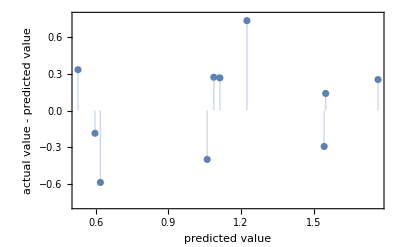
{-Graphics-,0.150988}

```mathematica
pm1/@{"ResidualPlot","MeanSquare"}
```

```mathematica
p12=Predict[trainingSet1,Method->{"RandomForest","LeafSize"->1}]
```

PredictorFunction[…]

```mathematica
pm12=PredictorMeasurements[p12,testSet1]
```

PredictorMeasurementsObject[…]

```mathematica
pm12/@{"ResidualPlot","MeanSquare"}
```

{-Graphics-,0.150988}

```mathematica
p13=Predict[trainingSet1,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

```mathematica
pm13=PredictorMeasurements[p13,testSet1]
```

PredictorMeasurementsObject[…]

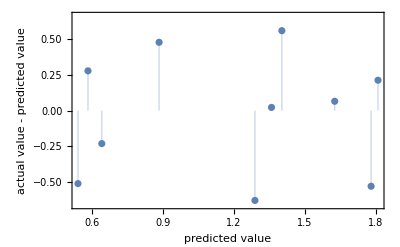
{-Graphics-,0.165381}

```mathematica
pm13/@{"ResidualPlot","MeanSquare"}
```

### Generating More Random Splits of the Data

```mathematica
InputFinal
```

(4.26288 | 1.00751 | 1.02879 | 0.933717 | -0.409207 | 1.01218 | 0.181818 | 1. | 1.29772 | 1.07062 | 1.24086 | 11.4186
1.56584 | 0.973494 | 0.982799 | 0.889077 | -0.434783 | 0.623166 | 0.533597 | 1.00141 | 1.20883 | 1.20339 | 1.01218 | 11.4047
1.00484 | 0.919661 | 0.910556 | 0.896517 | 0.69821 | 0.385264 | 0.498024 | 1.00707 | 1.05705 | 0.957627 | 0.935333 | 12.9209
1.06023 | 0.918705 | 0.912004 | 0.895333 | 0.659847 | 0.400562 | 0.498024 | 1.00283 | 1.12345 | 0.957627 | 0.935333 | 15.3814
0.949452 | 0.924307 | 0.906935 | 0.893135 | 0.69821 | 0.348736 | 0.501976 | 1.00424 | 0.990661 | 0.966102 | 0.946579 | 10.4605
1.62123 | 0.988933 | 0.865472 | 0.856611 | 0.731458 | 0.779894 | -0.592885 | 1.00707 | 1.27523 | 1.16384 | 1.00281 | 12.8419
4.46109 | 1.00751 | 1.02969 | 0.934562 | -0.409207 | 1.02123 | 0.181818 | 1.00283 | 1.23133 | 1.11582 | 1.2821 | 9.9814
1.11562 | 0.918295 | 0.909832 | 0.896179 | 0.703325 | 0.390259 | 0.482213 | 1.00849 | 1.18985 | 0.957627 | 0.917526 | 15.7488
1.51045 | 0.972947 | 0.987326 | 0.895333 | -0.404092 | 0.660318 | -0.517787 | 1. | 1.14244 | 1.21751 | 1.03093 | 8.94419
1.51044 | 0.955458 | 0.964512 | 0.885019 | -0.237852 | 1.25414 | -0.865613 | 1.00849 | 1.14244 | 1.24859 | 1.03093 | 8.10698
1.0554 | 0.933188 | 0.923592 | 0.942847 | 1.21483 | 0.986263 | 1.37945 | 1.00849 | 1.06639 | 0.968927 | 0.982193 | 6.47442
0.949447 | 0.929362 | 0.909651 | 0.896348 | 0.710997 | 0.41305 | 0.494071 | 1.01273 | 0.990661 | 0.985876 | 0.948454 | 11.4837
1.56584 | 0.977729 | 0.965598 | 0.885357 | -0.248082 | 1.27505 | -0.869565 | 1. | 1.20883 | 1.23164 | 1.02156 | 10.5674
0.894055 | 1.14128 | 0.931016 | 0.921711 | 0.790281 | 0.505151 | 0.525692 | 1.0099 | 0.924263 | 0.997175 | 0.961575 | 9.02326
1.15966 | 0.966662 | 0.968495 | 0.973115 | 1.04092 | 0.404933 | 1.07905 | 1.00849 | 1.13259 | 1.22881 | 1.10965 | 7.64651
1.11079 | 0.929499 | 0.918523 | 0.935238 | 1.17136 | 1.00968 | 1.39526 | 1. | 1.13279 | 0.968927 | 0.969072 | 8.93488
1.45506 | 0.996311 | 0.981894 | 0.902097 | -0.225064 | 1.36684 | -0.881423 | 1.00141 | 1.07604 | 1.27119 | 1.04967 | 5.64651
0.998319 | 0.992622 | 0.976462 | 0.993575 | 1.23529 | 0.480487 | 1.28854 | 1. | 0.990457 | 1.28249 | 1.10122 | 7.90233
1.11079 | 0.992622 | 0.996741 | 0.999493 | 1.03836 | 0.949422 | 1.04743 | 1.00849 | 1.13279 | 0.968927 | 0.969072 | 7.30698
0.998323 | 0.929499 | 0.899511 | 0.883666 | 0.659847 | 0.469872 | 1.28854 | 1.01132 | 0.990457 | 1.28249 | 1.10122 | 7.90233
1.16618 | 0.944255 | 0.916712 | 0.934731 | 1.18926 | 1.02279 | 1.3913 | 1.00849 | 1.19918 | 0.966102 | 0.957826 | 11.3953
1.0554 | 0.992622 | 0.996741 | 0.998985 | 1.03069 | 0.964408 | 0.889328 | 1.0099 | 1.06639 | 0.99435 | 0.984067 | 5.86977
1.21673 | 1.00751 | 1.03259 | 1.00795 | 0.657289 | 0.402123 | 1.06324 | 1.0099 | 1.20852 | 0.960452 | 1.00187 | 2.96279
1.11078 | 0.981418 | 0.985515 | 0.985966 | 0.994885 | 0.934749 | 1.04348 | 1.0099 | 1.13279 | 0.991525 | 0.970947 | -8.56744
1.51044 | 0.97404 | 0.995655 | 0.924586 | -0.0767263 | 1.22385 | 1.1581 | 1.00707 | 1.14244 | 1.24859 | 1.03093 | 5.80465
1.51044 | 0.970351 | 1.00833 | 0.929828 | -0.179028 | 1.15954 | 1.14229 | 1.00141 | 1.14244 | 1.24859 | 1.03093 | -4.66512
1.45506 | 1. | 1.00235 | 0.927968 | -0.12532 | 1.25164 | 1.1581 | 0.992928 | 1.07604 | 1.27119 | 1.04967 | 3.34419
1.15966 | 0.959147 | 0.956183 | 0.945891 | 0.800512 | 0.133313 | 1.11858 | 0.992928 | 1.13259 | 1.22881 | 1.10965 | 6.0186
1.51044 | 0.962836 | 0.978997 | 0.901589 | -0.191816 | 1.37996 | -0.893281 | 0.997171 | 1.14244 | 1.24859 | 1.03093 | 8.10698
1.56584 | 0.959147 | 0.960167 | 0.88282 | -0.209719 | 1.26225 | -0.87747 | 1.00849 | 1.20883 | 1.23164 | 1.02156 | 10.5674
0.894061 | 0.962836 | 0.949303 | 0.974806 | 1.33504 | 0.797065 | 1.49407 | 1.00849 | 0.924263 | 0.980226 | 0.958763 | -5.88372
0.626755 | 1.06695 | 1.08112 | 1.07203 | 0.946292 | 0.489229 | 0.70751 | 1. | 0.706402 | 0.99435 | 0.8791 | 10.4233
1.62122 | 0.959147 | 0.961615 | 0.883328 | -0.225064 | 1.26975 | -0.865613 | 1.00707 | 1.27523 | 1.21751 | 1.00281 | 13.0279
1.38093 | 0.988933 | 1.01213 | 0.958573 | 0.202046 | 1.0537 | 1.05534 | 1.00707 | 1.4266 | 1.12429 | 1.02437 | 13.0698
0.998319 | 0.985244 | 0.964693 | 0.992898 | 1.3913 | 0.427412 | 1.04743 | 1.00849 | 0.990457 | 1.28249 | 1.10122 | 7.90233
0.836977 | 0.985244 | 0.958356 | 0.947244 | 0.790281 | 0.592882 | 1.3004 | 1.00141 | 0.848328 | 1.35593 | 1.08997 | 7.93953
1.16617 | 0.977729 | 0.984067 | 0.985289 | 1. | 0.920075 | 1.04743 | 1.00849 | 1.19918 | 0.988701 | 0.958763 | 8.26512
1.56584 | 0.959147 | 0.950027 | 0.935577 | 0.731458 | 0.952232 | 1.18577 | 1.00566 | 1.20883 | 1.23164 | 1.02156 | 8.26512
1.56584 | 0.977729 | 1.00181 | 0.924248 | -0.171355 | 1.17109 | 1.12648 | 1.00424 | 1.20883 | 1.23164 | 1.02156 | 8.26512
1.0554 | 1. | 1.00018 | 0.999662 | 0.992327 | 0.979082 | 0.968379 | 1.01697 | 1.06639 | 0.968927 | 0.982193 | 4.84651
1.11079 | 0.97404 | 0.97954 | 0.979709 | 0.982097 | 0.930066 | 1.02767 | 1.00849 | 1.13279 | 0.991525 | 0.970947 | 5.92093
1.05539 | 0.988933 | 0.992395 | 0.992898 | 0.997442 | 1.01062 | 0.98419 | 1.00849 | 1.06639 | 0.99435 | 0.984067 | 3.46047
0.999993 | 1.01872 | 1.03549 | 1.01573 | 0.736573 | 0.452388 | 1.20553 | 1.00424 | 1. | 1. | 1. | -14.3256
0.894052 | 0.996311 | 0.985696 | 0.989009 | 1.03581 | 1.14674 | 1.21739 | 1.01414 | 0.924263 | 0.980226 | 0.958763 | 2.02326
0.838658 | 0.996311 | 0.985515 | 0.98884 | 1.03836 | 1.16266 | 1.21344 | 1.00849 | 0.85787 | 1.01695 | 0.975633 | 0.586047)

```mathematica
Dimensions[%]
```

{45,12}

```mathematica
LogMUsInput
```

{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,-0.03,-0.06,-0.67}

```mathematica
trainingIndices2=Sort@RandomSample[Range[45],35]
```

{2,3,4,5,6,8,9,10,11,12,13,14,15,16,18,19,20,21,22,24,25,27,28,30,33,34,35,36,37,38,39,41,43,44,45}

```mathematica
testIndices2=Complement[Range[45],trainingIndices2]
```

{1,7,17,23,26,29,31,32,40,42}

```mathematica
trainingData2=InputFinal[[trainingIndices2]]
```

(1.56584 | 0.973494 | 0.982799 | 0.889077 | -0.434783 | 0.623166 | 0.533597 | 1.00141 | 1.20883 | 1.20339 | 1.01218 | 11.4047
1.00484 | 0.919661 | 0.910556 | 0.896517 | 0.69821 | 0.385264 | 0.498024 | 1.00707 | 1.05705 | 0.957627 | 0.935333 | 12.9209
1.06023 | 0.918705 | 0.912004 | 0.895333 | 0.659847 | 0.400562 | 0.498024 | 1.00283 | 1.12345 | 0.957627 | 0.935333 | 15.3814
0.949452 | 0.924307 | 0.906935 | 0.893135 | 0.69821 | 0.348736 | 0.501976 | 1.00424 | 0.990661 | 0.966102 | 0.946579 | 10.4605
1.62123 | 0.988933 | 0.865472 | 0.856611 | 0.731458 | 0.779894 | -0.592885 | 1.00707 | 1.27523 | 1.16384 | 1.00281 | 12.8419
1.11562 | 0.918295 | 0.909832 | 0.896179 | 0.703325 | 0.390259 | 0.482213 | 1.00849 | 1.18985 | 0.957627 | 0.917526 | 15.7488
1.51045 | 0.972947 | 0.987326 | 0.895333 | -0.404092 | 0.660318 | -0.517787 | 1. | 1.14244 | 1.21751 | 1.03093 | 8.94419
1.51044 | 0.955458 | 0.964512 | 0.885019 | -0.237852 | 1.25414 | -0.865613 | 1.00849 | 1.14244 | 1.24859 | 1.03093 | 8.10698
1.0554 | 0.933188 | 0.923592 | 0.942847 | 1.21483 | 0.986263 | 1.37945 | 1.00849 | 1.06639 | 0.968927 | 0.982193 | 6.47442
0.949447 | 0.929362 | 0.909651 | 0.896348 | 0.710997 | 0.41305 | 0.494071 | 1.01273 | 0.990661 | 0.985876 | 0.948454 | 11.4837
1.56584 | 0.977729 | 0.965598 | 0.885357 | -0.248082 | 1.27505 | -0.869565 | 1. | 1.20883 | 1.23164 | 1.02156 | 10.5674
0.894055 | 1.14128 | 0.931016 | 0.921711 | 0.790281 | 0.505151 | 0.525692 | 1.0099 | 0.924263 | 0.997175 | 0.961575 | 9.02326
1.15966 | 0.966662 | 0.968495 | 0.973115 | 1.04092 | 0.404933 | 1.07905 | 1.00849 | 1.13259 | 1.22881 | 1.10965 | 7.64651
1.11079 | 0.929499 | 0.918523 | 0.935238 | 1.17136 | 1.00968 | 1.39526 | 1. | 1.13279 | 0.968927 | 0.969072 | 8.93488
0.998319 | 0.992622 | 0.976462 | 0.993575 | 1.23529 | 0.480487 | 1.28854 | 1. | 0.990457 | 1.28249 | 1.10122 | 7.90233
1.11079 | 0.992622 | 0.996741 | 0.999493 | 1.03836 | 0.949422 | 1.04743 | 1.00849 | 1.13279 | 0.968927 | 0.969072 | 7.30698
0.998323 | 0.929499 | 0.899511 | 0.883666 | 0.659847 | 0.469872 | 1.28854 | 1.01132 | 0.990457 | 1.28249 | 1.10122 | 7.90233
1.16618 | 0.944255 | 0.916712 | 0.934731 | 1.18926 | 1.02279 | 1.3913 | 1.00849 | 1.19918 | 0.966102 | 0.957826 | 11.3953
1.0554 | 0.992622 | 0.996741 | 0.998985 | 1.03069 | 0.964408 | 0.889328 | 1.0099 | 1.06639 | 0.99435 | 0.984067 | 5.86977
1.11078 | 0.981418 | 0.985515 | 0.985966 | 0.994885 | 0.934749 | 1.04348 | 1.0099 | 1.13279 | 0.991525 | 0.970947 | -8.56744
1.51044 | 0.97404 | 0.995655 | 0.924586 | -0.0767263 | 1.22385 | 1.1581 | 1.00707 | 1.14244 | 1.24859 | 1.03093 | 5.80465
1.45506 | 1. | 1.00235 | 0.927968 | -0.12532 | 1.25164 | 1.1581 | 0.992928 | 1.07604 | 1.27119 | 1.04967 | 3.34419
1.15966 | 0.959147 | 0.956183 | 0.945891 | 0.800512 | 0.133313 | 1.11858 | 0.992928 | 1.13259 | 1.22881 | 1.10965 | 6.0186
1.56584 | 0.959147 | 0.960167 | 0.88282 | -0.209719 | 1.26225 | -0.87747 | 1.00849 | 1.20883 | 1.23164 | 1.02156 | 10.5674
1.62122 | 0.959147 | 0.961615 | 0.883328 | -0.225064 | 1.26975 | -0.865613 | 1.00707 | 1.27523 | 1.21751 | 1.00281 | 13.0279
1.38093 | 0.988933 | 1.01213 | 0.958573 | 0.202046 | 1.0537 | 1.05534 | 1.00707 | 1.4266 | 1.12429 | 1.02437 | 13.0698
0.998319 | 0.985244 | 0.964693 | 0.992898 | 1.3913 | 0.427412 | 1.04743 | 1.00849 | 0.990457 | 1.28249 | 1.10122 | 7.90233
0.836977 | 0.985244 | 0.958356 | 0.947244 | 0.790281 | 0.592882 | 1.3004 | 1.00141 | 0.848328 | 1.35593 | 1.08997 | 7.93953
1.16617 | 0.977729 | 0.984067 | 0.985289 | 1. | 0.920075 | 1.04743 | 1.00849 | 1.19918 | 0.988701 | 0.958763 | 8.26512
1.56584 | 0.959147 | 0.950027 | 0.935577 | 0.731458 | 0.952232 | 1.18577 | 1.00566 | 1.20883 | 1.23164 | 1.02156 | 8.26512
1.56584 | 0.977729 | 1.00181 | 0.924248 | -0.171355 | 1.17109 | 1.12648 | 1.00424 | 1.20883 | 1.23164 | 1.02156 | 8.26512
1.11079 | 0.97404 | 0.97954 | 0.979709 | 0.982097 | 0.930066 | 1.02767 | 1.00849 | 1.13279 | 0.991525 | 0.970947 | 5.92093
0.999993 | 1.01872 | 1.03549 | 1.01573 | 0.736573 | 0.452388 | 1.20553 | 1.00424 | 1. | 1. | 1. | -14.3256
0.894052 | 0.996311 | 0.985696 | 0.989009 | 1.03581 | 1.14674 | 1.21739 | 1.01414 | 0.924263 | 0.980226 | 0.958763 | 2.02326
0.838658 | 0.996311 | 0.985515 | 0.98884 | 1.03836 | 1.16266 | 1.21344 | 1.00849 | 0.85787 | 1.01695 | 0.975633 | 0.586047)

```mathematica
Dimensions[trainingData1]
```

{35,12}

```mathematica
trainingResults2=LogMUsInput[[trainingIndices2]]
```

{1.96,2.02,1.95,1.9,1.71,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.,1.05,1.,1.38,0.87,0.83,0.84,0.81,0.76,0.68,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.23,-0.03,-0.06,-0.67}

```mathematica
Dimensions[trainingResults1]
```

{35}

```mathematica
trainingSet2=Thread[trainingData2->trainingResults2]
```

{{1.56584,0.973494,0.982799,0.889077,-0.434783,0.623166,0.533597,1.00141,1.20883,1.20339,1.01218,11.4047}→1.96,{1.00484,0.919661,0.910556,0.896517,0.69821,0.385264,0.498024,1.00707,1.05705,0.957627,0.935333,12.9209}→2.02,{1.06023,0.918705,0.912004,0.895333,0.659847,0.400562,0.498024,1.00283,1.12345,0.957627,0.935333,15.3814}→1.95,{0.949452,0.924307,0.906935,0.893135,0.69821,0.348736,0.501976,1.00424,0.990661,0.966102,0.946579,10.4605}→1.9,{1.62123,0.988933,0.865472,0.856611,0.731458,0.779894,-0.592885,1.00707,1.27523,1.16384,1.00281,12.8419}→1.71,{1.11562,0.918295,0.909832,0.896179,0.703325,0.390259,0.482213,1.00849,1.18985,0.957627,0.917526,15.7488}→1.68,{1.51045,0.972947,0.987326,0.895333,-0.404092,0.660318,-0.517787,1.,1.14244,1.21751,1.03093,8.94419}→1.66,{1.51044,0.955458,0.964512,0.885019,-0.237852,1.25414,-0.865613,1.00849,1.14244,1.24859,1.03093,8.10698}→1.36,{1.0554,0.933188,0.923592,0.942847,1.21483,0.986263,1.37945,1.00849,1.06639,0.968927,0.982193,6.47442}→1.33,{0.949447,0.929362,0.909651,0.896348,0.710997,0.41305,0.494071,1.01273,0.990661,0.985876,0.948454,11.4837}→1.25,{1.56584,0.977729,0.965598,0.885357,-0.248082,1.27505,-0.869565,1.,1.20883,1.23164,1.02156,10.5674}→1.29,{0.894055,1.14128,0.931016,0.921711,0.790281,0.505151,0.525692,1.0099,0.924263,0.997175,0.961575,9.02326}→1.27,{1.15966,0.966662,0.968495,0.973115,1.04092,0.404933,1.07905,1.00849,1.13259,1.22881,1.10965,7.64651}→1.14,{1.11079,0.929499,0.918523,0.935238,1.17136,1.00968,1.39526,1.,1.13279,0.968927,0.969072,8.93488}→1.36,{0.998319,0.992622,0.976462,0.993575,1.23529,0.480487,1.28854,1.,0.990457,1.28249,1.10122,7.90233}→1.,{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,1.13279,0.968927,0.969072,7.30698}→1.05,{0.998323,0.929499,0.899511,0.883666,0.659847,0.469872,1.28854,1.01132,0.990457,1.28249,1.10122,7.90233}→1.,{1.16618,0.944255,0.916712,0.934731,1.18926,1.02279,1.3913,1.00849,1.19918,0.966102,0.957826,11.3953}→1.38,{1.0554,0.992622,0.996741,0.998985,1.03069,0.964408,0.889328,1.0099,1.06639,0.99435,0.984067,5.86977}→0.87,{1.11078,0.981418,0.985515,0.985966,0.994885,0.934749,1.04348,1.0099,1.13279,0.991525,0.970947,-8.56744}→0.83,{1.51044,0.97404,0.995655,0.924586,-0.0767263,1.22385,1.1581,1.00707,1.14244,1.24859,1.03093,5.80465}→0.84,{1.45506,1.,1.00235,0.927968,-0.12532,1.25164,1.1581,0.992928,1.07604,1.27119,1.04967,3.34419}→0.81,{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.13259,1.22881,1.10965,6.0186}→0.76,{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.20883,1.23164,1.02156,10.5674}→0.68,{1.62122,0.959147,0.961615,0.883328,-0.225064,1.26975,-0.865613,1.00707,1.27523,1.21751,1.00281,13.0279}→0.58,{1.38093,0.988933,1.01213,0.958573,0.202046,1.0537,1.05534,1.00707,1.4266,1.12429,1.02437,13.0698}→0.46,{0.998319,0.985244,0.964693,0.992898,1.3913,0.427412,1.04743,1.00849,0.990457,1.28249,1.10122,7.90233}→0.43,{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,0.848328,1.35593,1.08997,7.93953}→0.41,{1.16617,0.977729,0.984067,0.985289,1.,0.920075,1.04743,1.00849,1.19918,0.988701,0.958763,8.26512}→0.38,{1.56584,0.959147,0.950027,0.935577,0.731458,0.952232,1.18577,1.00566,1.20883,1.23164,1.02156,8.26512}→0.38,{1.56584,0.977729,1.00181,0.924248,-0.171355,1.17109,1.12648,1.00424,1.20883,1.23164,1.02156,8.26512}→0.38,{1.11079,0.97404,0.97954,0.979709,0.982097,0.930066,1.02767,1.00849,1.13279,0.991525,0.970947,5.92093}→0.23,{0.999993,1.01872,1.03549,1.01573,0.736573,0.452388,1.20553,1.00424,1.,1.,1.,-14.3256}→-0.03,{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,0.924263,0.980226,0.958763,2.02326}→-0.06,{0.838658,0.996311,0.985515,0.98884,1.03836,1.16266,1.21344,1.00849,0.85787,1.01695,0.975633,0.586047}→-0.67}

```mathematica
testSet2=Thread[InputFinal[[testIndices2]]-> LogMUsInput[[testIndices2]]]
```

{{4.26288,1.00751,1.02879,0.933717,-0.409207,1.01218,0.181818,1.,1.29772,1.07062,1.24086,11.4186}→2.72,{4.46109,1.00751,1.02969,0.934562,-0.409207,1.02123,0.181818,1.00283,1.23133,1.11582,1.2821,9.9814}→1.69,{1.45506,0.996311,0.981894,0.902097,-0.225064,1.36684,-0.881423,1.00141,1.07604,1.27119,1.04967,5.64651}→1.11,{1.21673,1.00751,1.03259,1.00795,0.657289,0.402123,1.06324,1.0099,1.20852,0.960452,1.00187,2.96279}→0.86,{1.51044,0.970351,1.00833,0.929828,-0.179028,1.15954,1.14229,1.00141,1.14244,1.24859,1.03093,-4.66512}→0.84,{1.51044,0.962836,0.978997,0.901589,-0.191816,1.37996,-0.893281,0.997171,1.14244,1.24859,1.03093,8.10698}→0.66,{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,0.924263,0.980226,0.958763,-5.88372}→0.67,{0.626755,1.06695,1.08112,1.07203,0.946292,0.489229,0.70751,1.,0.706402,0.99435,0.8791,10.4233}→0.59,{1.0554,1.,1.00018,0.999662,0.992327,0.979082,0.968379,1.01697,1.06639,0.968927,0.982193,4.84651}→0.33,{1.05539,0.988933,0.992395,0.992898,0.997442,1.01062,0.98419,1.00849,1.06639,0.99435,0.984067,3.46047}→0.03}

```mathematica
trainingIndices3=Sort@RandomSample[Range[45],35]
```

{2,3,4,5,6,7,9,11,12,13,15,16,17,18,19,20,21,22,23,25,26,27,28,29,30,34,35,37,38,39,40,41,43,44,45}

```mathematica
testIndices3=Complement[Range[45],trainingIndices3]
```

{1,8,10,14,24,31,32,33,36,42}

```mathematica
trainingIndices4=Sort@RandomSample[Range[45],35]
```

{1,2,3,4,6,7,8,10,12,13,14,17,18,19,20,22,23,24,25,27,28,29,30,31,32,33,34,37,39,40,41,42,43,44,45}

```mathematica
testIndices4=Complement[Range[45],trainingIndices4]
```

{5,9,11,15,16,21,26,35,36,38}

```mathematica
trainingIndices5=Sort@RandomSample[Range[45],35]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,16,17,19,20,21,23,25,26,27,29,31,32,34,35,38,39,40,41,42,43,44,45}

```mathematica
testIndices5=Complement[Range[45],trainingIndices5]
```

{1,15,18,22,24,28,30,33,36,37}

```mathematica
trainingIndices6=Sort@RandomSample[Range[45],35]
```

{1,2,3,4,5,6,7,9,12,13,14,15,16,17,19,22,23,25,26,29,30,31,32,33,34,35,36,37,38,39,40,42,43,44,45}

```mathematica
testIndices6=Complement[Range[45],trainingIndices6]
```

{8,10,11,18,20,21,24,27,28,41}

```mathematica
trainingIndices7=Sort@RandomSample[Range[45],35]
```

{1,2,3,4,6,7,8,9,10,11,12,13,15,17,18,20,21,22,23,26,27,29,30,32,33,35,36,37,38,39,40,41,42,43,45}

```mathematica
testIndices7=Complement[Range[45],trainingIndices7]
```

{5,14,16,19,24,25,28,31,34,44}

```mathematica
trainingIndices8=Sort@RandomSample[Range[45],35]
```

{1,2,3,4,5,7,8,11,14,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,34,35,36,37,39,40,42,43,44,45}

```mathematica
testIndices8=Complement[Range[45],trainingIndices8]
```

{6,9,10,12,13,15,16,33,38,41}

```mathematica
trainingIndices9=Sort@RandomSample[Range[45],35]
```

{1,2,3,4,5,6,7,8,10,11,12,13,15,16,17,18,19,20,21,22,24,26,27,29,30,33,34,36,37,38,39,41,42,43,45}

```mathematica
testIndices9=Complement[Range[45],trainingIndices9]
```

{9,14,23,25,28,31,32,35,40,44}

```mathematica
trainingIndices10=Sort@RandomSample[Range[45],35]
```

{2,3,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,28,29,30,31,32,33,34,35,36,37,39,42,43,44}

```mathematica
testIndices10=Complement[Range[45],trainingIndices10]
```

{1,4,6,13,15,27,38,40,41,45}

### Test Predict[] for Robustness

```mathematica
p2=Predict[trainingSet2,Method->{"RandomForest","LeafSize"->1}]
```

PredictorFunction[…]

```mathematica
pm2=PredictorMeasurements[p2,testSet2]
```

PredictorMeasurementsObject[…]

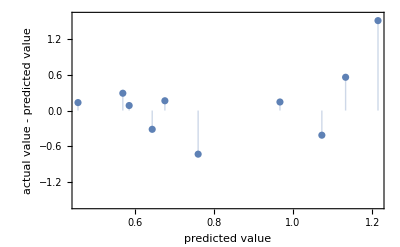
{-Graphics-,0.353535}

```mathematica
pm2/@{"ResidualPlot","MeanSquare"}
```

```mathematica
p3=Predict[Thread[InputFinal[[trainingIndices3]]->LogMUsInput[[trainingIndices3]]],Method->{"RandomForest","LeafSize"->1}]
```

```mathematica
pm3=PredictorMeasurements[p3,Thread[InputFinal[[testIndices3]]->LogMUsInput[[testIndices3]]]]
```

PredictorMeasurementsObject[…]

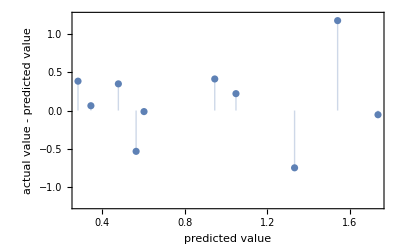
{-Graphics-,0.274352}

```mathematica
pm3/@{"ResidualPlot","MeanSquare"}
```

```mathematica
p4=Predict[Thread[InputFinal[[trainingIndices4]]->LogMUsInput[[trainingIndices4]]],Method->{"RandomForest","LeafSize"->1}]
```

PredictorFunction[…]

```mathematica
pm4=PredictorMeasurements[p4,Thread[InputFinal[[testIndices4]]->LogMUsInput[[testIndices4]]]]
```

PredictorMeasurementsObject[…]

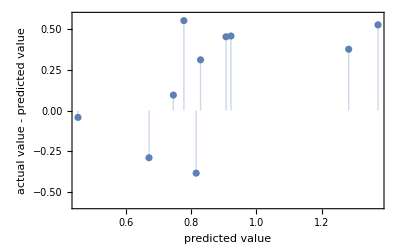
{-Graphics-,0.148094}

```mathematica
pm4/@{"ResidualPlot","MeanSquare"}
```

```mathematica
p5=Predict[Thread[InputFinal[[trainingIndices5]]->LogMUsInput[[trainingIndices5]]],Method->{"RandomForest","LeafSize"->1}]
```

PredictorFunction[…]

```mathematica
pm5=PredictorMeasurements[p5,Thread[InputFinal[[testIndices5]]->LogMUsInput[[testIndices5]]]]
```

PredictorMeasurementsObject[…]

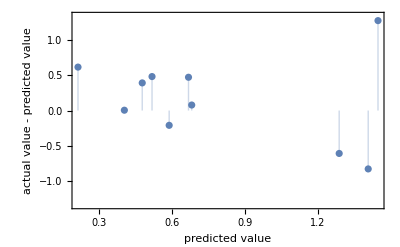
{-Graphics-,0.370791}

```mathematica
pm5/@{"ResidualPlot","MeanSquare"}
```

```mathematica
p6=Predict[Thread[InputFinal[[trainingIndices6]]->LogMUsInput[[trainingIndices6]],Method->{"RandomForest","LeafSize"->1}]]
```

PredictorFunction[…]

```mathematica
pm6=PredictorMeasurements[p6,Thread[InputFinal[[testIndices6]]->LogMUsInput[[testIndices6]]]]
```

PredictorMeasurementsObject[…]

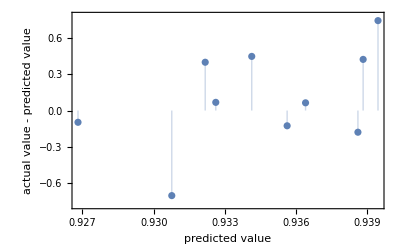
{-Graphics-,0.163957}

```mathematica
pm6/@{"ResidualPlot","MeanSquare"}
```

```mathematica
p7=Predict[Thread[InputFinal[[trainingIndices7]]->LogMUsInput[[trainingIndices7]]],Method->{"RandomForest","LeafSize"->1}]
```

PredictorFunction[…]

```mathematica
pm7=PredictorMeasurements[p7,Thread[InputFinal[[testIndices7]]->LogMUsInput[[testIndices7]]]]
```

PredictorMeasurementsObject[…]

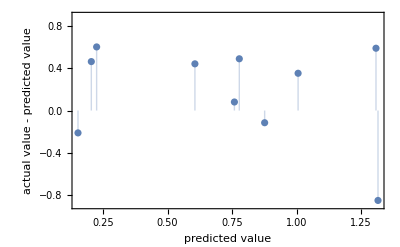
{-Graphics-,0.229586}

```mathematica
pm7/@{"ResidualPlot","MeanSquare"}
```

```mathematica
p8=Predict[Thread[InputFinal[[trainingIndices8]]->LogMUsInput[[trainingIndices8]]],Method->{"RandomForest","LeafSize"->1}]
```

PredictorFunction[…]

```mathematica
pm8=PredictorMeasurements[p8,Thread[InputFinal[[testIndices8]]->LogMUsInput[[testIndices8]]]]
```

PredictorMeasurementsObject[…]

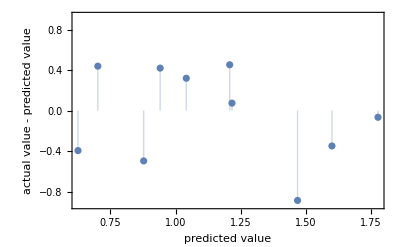
{-Graphics-,0.199941}

```mathematica
pm8/@{"ResidualPlot","MeanSquare"}
```

```mathematica
p9=Predict[Thread[InputFinal[[trainingIndices9]]->LogMUsInput[[trainingIndices9]]],Method->{"RandomForest","LeafSize"->1}]
```

PredictorFunction[…]

```mathematica
pm9=PredictorMeasurements[p9,Thread[InputFinal[[testIndices9]]->LogMUsInput[[testIndices9]]]]
```

PredictorMeasurementsObject[…]

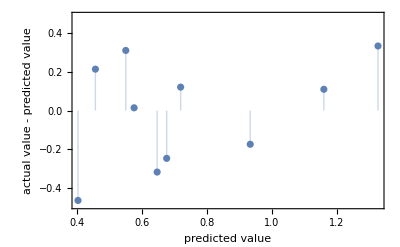
{-Graphics-,0.06846}

```mathematica
pm9/@{"ResidualPlot","MeanSquare"}
```

```mathematica
p10=Predict[Thread[InputFinal[[trainingIndices10]]->LogMUsInput[[trainingIndices10]]],Method->{"RandomForest","LeafSize"->1}]
```

PredictorFunction[…]

```mathematica
pm10=PredictorMeasurements[p10,Thread[InputFinal[[testIndices10]]->LogMUsInput[[testIndices10]]]]
```

PredictorMeasurementsObject[…]

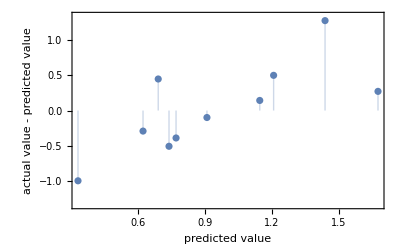
{-Graphics-,0.369737}

```mathematica
pm10/@{"ResidualPlot","MeanSquare"}
```

## Regression - Comparison

```mathematica
data4
```

(ET | IP | EHOMO | η | ELUMO | DM | Qp | Qmin | MW | n | γ | D | logP | logMU
-82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 3.242 | 0.046 | -0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455 | 2.72
-30241. | 7.125 | -5.428 | 5.258 | -0.17 | 1.996 | 0.135 | -0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452 | 1.96
-19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 1.234 | 0.126 | -0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778 | 2.02
-20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 1.283 | 0.126 | -0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307 | 1.95
-18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 1.117 | 0.127 | -0.71 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249 | 1.9
-31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | 2.498 | -0.15 | -0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761 | 1.71
-86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 3.271 | 0.046 | -0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146 | 1.69
-21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 1.25 | 0.122 | -0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386 | 1.68
-29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | 2.115 | -0.131 | -0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923 | 1.66
-29171. | 6.993 | -5.327 | 5.234 | -0.093 | 4.017 | -0.219 | -0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 1.36
-20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 3.159 | 0.349 | -0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392 | 1.33
-18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 1.323 | 0.125 | -0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469 | 1.25
-30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | 4.084 | -0.22 | -0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 1.29
-17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 1.618 | 0.133 | -0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94 | 1.27
-22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 1.297 | 0.273 | -0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644 | 1.14
-21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 3.234 | 0.353 | -0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921 | 1.36
-28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | 4.378 | -0.223 | -0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214 | 1.11
-19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 1.539 | 0.326 | -0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 1.
-21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 3.041 | 0.265 | -0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571 | 1.05
-19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 1.505 | 0.326 | -0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 1.
-22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 3.276 | 0.352 | -0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45 | 1.38
-20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 3.089 | 0.225 | -0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262 | 0.87
-23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 1.288 | 0.269 | -0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637 | 0.86
-21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 2.994 | 0.264 | -0.714 | 239.311 | 1.506 | 35.1 | 1.036 | -1.842 | 0.83
-29171. | 7.129 | -5.499 | 5.468 | -0.03 | 3.92 | 0.293 | -0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248 | 0.84
-29171. | 7.102 | -5.569 | 5.499 | -0.07 | 3.714 | 0.289 | -0.708 | 241.35 | 1.552 | 44.2 | 1.1 | -1.003 | 0.84
-28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 4.009 | 0.293 | -0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719 | 0.81
-22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.427 | 0.283 | -0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294 | 0.76
-29171. | 7.047 | -5.407 | 5.332 | -0.075 | 4.42 | -0.226 | -0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 0.66
-30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | 4.043 | -0.222 | -0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 0.68
-17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 2.553 | 0.378 | -0.713 | 195.258 | 1.512 | 34.7 | 1.023 | -1.265 | 0.67
-12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 1.567 | 0.179 | -0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241 | 0.59
-31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | 4.067 | -0.219 | -0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801 | 0.58
-26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 3.375 | 0.267 | -0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81 | 0.46
-19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 1.369 | 0.265 | -0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 0.43
-16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 1.899 | 0.329 | -0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707 | 0.41
-22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 2.947 | 0.265 | -0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777 | 0.38
-30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 3.05 | 0.3 | -0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 0.38
-30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 3.751 | 0.285 | -0.71 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 0.38
-20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 3.136 | 0.245 | -0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042 | 0.33
-21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 2.979 | 0.26 | -0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273 | 0.23
-20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 3.237 | 0.249 | -0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744 | 0.03
-19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 3.203 | 0.253 | -0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215 | 0.
-19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 1.449 | 0.305 | -0.71 | 211.258 | 1.511 | 35.4 | 1.067 | -3.08 | -0.03
-17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 3.673 | 0.308 | -0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435 | -0.06
-16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 3.724 | 0.307 | -0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126 | -0.67)

```mathematica
GoodData=ReplacePart[data4,{_,-5}->Nothing]
```

(ET | IP | EHOMO | η | ELUMO | DM | Qp | Qmin | MW | γ | D | logP | logMU
-82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 3.242 | 0.046 | -0.707 | 274.154 | 37.9 | 1.324 | 2.455 | 2.72
-30241. | 7.125 | -5.428 | 5.258 | -0.17 | 1.996 | 0.135 | -0.708 | 255.376 | 42.6 | 1.08 | 2.452 | 1.96
-19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 1.234 | 0.126 | -0.712 | 223.311 | 33.9 | 0.998 | 2.778 | 2.02
-20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 1.283 | 0.126 | -0.709 | 237.338 | 33.9 | 0.998 | 3.307 | 1.95
-18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 1.117 | 0.127 | -0.71 | 209.285 | 34.2 | 1.01 | 2.249 | 1.9
-31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | 2.498 | -0.15 | -0.712 | 269.403 | 41.2 | 1.07 | 2.761 | 1.71
-86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 3.271 | 0.046 | -0.709 | 260.128 | 39.5 | 1.368 | 2.146 | 1.69
-21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 1.25 | 0.122 | -0.713 | 251.365 | 33.9 | 0.979 | 3.386 | 1.68
-29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | 2.115 | -0.131 | -0.707 | 241.35 | 43.1 | 1.1 | 1.923 | 1.66
-29171. | 6.993 | -5.327 | 5.234 | -0.093 | 4.017 | -0.219 | -0.713 | 241.35 | 44.2 | 1.1 | 1.743 | 1.36
-20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 3.159 | 0.349 | -0.713 | 225.284 | 34.3 | 1.048 | 1.392 | 1.33
-18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 1.323 | 0.125 | -0.716 | 209.285 | 34.9 | 1.012 | 2.469 | 1.25
-30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | 4.084 | -0.22 | -0.707 | 255.376 | 43.6 | 1.09 | 2.272 | 1.29
-17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 1.618 | 0.133 | -0.714 | 195.258 | 35.3 | 1.026 | 1.94 | 1.27
-22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 1.297 | 0.273 | -0.713 | 239.268 | 43.5 | 1.184 | 1.644 | 1.14
-21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 3.234 | 0.353 | -0.707 | 239.311 | 34.3 | 1.034 | 1.921 | 1.36
-28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | 4.378 | -0.223 | -0.708 | 227.323 | 45. | 1.12 | 1.214 | 1.11
-19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 1.539 | 0.326 | -0.707 | 209.242 | 45.4 | 1.175 | 1.699 | 1.
-21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 3.041 | 0.265 | -0.713 | 239.311 | 34.3 | 1.034 | 1.571 | 1.05
-19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 1.505 | 0.326 | -0.715 | 209.242 | 45.4 | 1.175 | 1.699 | 1.
-22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 3.276 | 0.352 | -0.713 | 253.337 | 34.2 | 1.022 | 2.45 | 1.38
-20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 3.089 | 0.225 | -0.714 | 225.284 | 35.2 | 1.05 | 1.262 | 0.87
-23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 1.288 | 0.269 | -0.714 | 255.31 | 34. | 1.069 | 0.637 | 0.86
-21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 2.994 | 0.264 | -0.714 | 239.311 | 35.1 | 1.036 | -1.842 | 0.83
-29171. | 7.129 | -5.499 | 5.468 | -0.03 | 3.92 | 0.293 | -0.712 | 241.35 | 44.2 | 1.1 | 1.248 | 0.84
-29171. | 7.102 | -5.569 | 5.499 | -0.07 | 3.714 | 0.289 | -0.708 | 241.35 | 44.2 | 1.1 | -1.003 | 0.84
-28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 4.009 | 0.293 | -0.702 | 227.323 | 45. | 1.12 | 0.719 | 0.81
-22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.427 | 0.283 | -0.702 | 239.268 | 43.5 | 1.184 | 1.294 | 0.76
-29171. | 7.047 | -5.407 | 5.332 | -0.075 | 4.42 | -0.226 | -0.705 | 241.35 | 44.2 | 1.1 | 1.743 | 0.66
-30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | 4.043 | -0.222 | -0.713 | 255.376 | 43.6 | 1.09 | 2.272 | 0.68
-17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 2.553 | 0.378 | -0.713 | 195.258 | 34.7 | 1.023 | -1.265 | 0.67
-12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 1.567 | 0.179 | -0.707 | 149.233 | 35.2 | 0.938 | 2.241 | 0.59
-31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | 4.067 | -0.219 | -0.712 | 269.403 | 43.1 | 1.07 | 2.801 | 0.58
-26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 3.375 | 0.267 | -0.712 | 301.38 | 39.8 | 1.093 | 2.81 | 0.46
-19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 1.369 | 0.265 | -0.713 | 209.242 | 45.4 | 1.175 | 1.699 | 0.43
-16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 1.899 | 0.329 | -0.708 | 179.216 | 48. | 1.163 | 1.707 | 0.41
-22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 2.947 | 0.265 | -0.713 | 253.337 | 35. | 1.023 | 1.777 | 0.38
-30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 3.05 | 0.3 | -0.711 | 255.376 | 43.6 | 1.09 | 1.777 | 0.38
-30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 3.751 | 0.285 | -0.71 | 255.376 | 43.6 | 1.09 | 1.777 | 0.38
-20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 3.136 | 0.245 | -0.719 | 225.284 | 34.3 | 1.048 | 1.042 | 0.33
-21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 2.979 | 0.26 | -0.713 | 239.311 | 35.1 | 1.036 | 1.273 | 0.23
-20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 3.237 | 0.249 | -0.713 | 225.284 | 35.2 | 1.05 | 0.744 | 0.03
-19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 3.203 | 0.253 | -0.707 | 211.258 | 35.4 | 1.067 | 0.215 | 0.
-19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 1.449 | 0.305 | -0.71 | 211.258 | 35.4 | 1.067 | -3.08 | -0.03
-17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 3.673 | 0.308 | -0.717 | 195.258 | 34.7 | 1.023 | 0.435 | -0.06
-16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 3.724 | 0.307 | -0.713 | 181.232 | 36. | 1.041 | 0.126 | -0.67)

```mathematica
?LinearModelFit
```

LinearModelFit[{y_1,y_2,…},{f_1,f_2,…},x] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… that fits the y_i for successive x values 1, 2, ….
LinearModelFit[{{x_11,x_12,…,y_1},{x_21,x_22,…,y_2},…},{f_1,f_2,…},{x_1,x_2,…}] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… where the f_i depend on the variables x_k. 
LinearModelFit[{m,v}] constructs a linear model from the design matrix m and response vector v.

```mathematica
Indices={1,3,5,6,10,-1}
```

{1,3,5,6,10,-1}

```mathematica
FiveVariables=Transpose@Part[Transpose[GoodData],Indices]
```

(ET | EHOMO | ELUMO | DM | γ | logMU
-82328.7 | -5.682 | -0.16 | 3.242 | 37.9 | 2.72
-30241. | -5.428 | -0.17 | 1.996 | 42.6 | 1.96
-19406.4 | -5.029 | 0.273 | 1.234 | 33.9 | 2.02
-20476.1 | -5.037 | 0.258 | 1.283 | 33.9 | 1.95
-18336.7 | -5.009 | 0.273 | 1.117 | 34.2 | 1.9
-31310.7 | -4.78 | 0.286 | 2.498 | 41.2 | 1.71
-86156.7 | -5.687 | -0.16 | 3.271 | 39.5 | 1.69
-21545.9 | -5.025 | 0.275 | 1.25 | 33.9 | 1.68
-29171.2 | -5.453 | -0.158 | 2.115 | 43.1 | 1.66
-29171. | -5.327 | -0.093 | 4.017 | 44.2 | 1.36
-20382.8 | -5.101 | 0.475 | 3.159 | 34.3 | 1.33
-18336.6 | -5.024 | 0.278 | 1.323 | 34.9 | 1.25
-30240.9 | -5.333 | -0.097 | 4.084 | 43.6 | 1.29
-17266.8 | -5.142 | 0.309 | 1.618 | 35.3 | 1.27
-22396.4 | -5.349 | 0.407 | 1.297 | 43.5 | 1.14
-21452.6 | -5.073 | 0.458 | 3.234 | 34.3 | 1.36
-28101.4 | -5.423 | -0.088 | 4.378 | 45. | 1.11
-19280.5 | -5.393 | 0.483 | 1.539 | 45.4 | 1.
-21452.6 | -5.505 | 0.406 | 3.041 | 34.3 | 1.05
-19280.5 | -4.968 | 0.258 | 1.505 | 45.4 | 1.
-22522.4 | -5.063 | 0.465 | 3.276 | 34.2 | 1.38
-20382.8 | -5.505 | 0.403 | 3.089 | 35.2 | 0.87
-23498.6 | -5.703 | 0.257 | 1.288 | 34. | 0.86
-21452.5 | -5.443 | 0.389 | 2.994 | 35.1 | 0.83
-29171. | -5.499 | -0.03 | 3.92 | 44.2 | 0.84
-29171. | -5.569 | -0.07 | 3.714 | 44.2 | 0.84
-28101.4 | -5.536 | -0.049 | 4.009 | 45. | 0.81
-22396.4 | -5.281 | 0.313 | 0.427 | 43.5 | 0.76
-29171. | -5.407 | -0.075 | 4.42 | 44.2 | 0.66
-30240.9 | -5.303 | -0.082 | 4.043 | 43.6 | 0.68
-17266.9 | -5.243 | 0.522 | 2.553 | 34.7 | 0.67
-12104.5 | -5.971 | 0.37 | 1.567 | 35.2 | 0.59
-31310.5 | -5.311 | -0.088 | 4.067 | 43.1 | 0.58
-26669.7 | -5.59 | 0.079 | 3.375 | 39.8 | 0.46
-19280.5 | -5.328 | 0.544 | 1.369 | 45.4 | 0.43
-16164.5 | -5.293 | 0.309 | 1.899 | 48. | 0.41
-22522.2 | -5.435 | 0.391 | 2.947 | 35. | 0.38
-30240.9 | -5.247 | 0.286 | 3.05 | 43.6 | 0.38
-30240.9 | -5.533 | -0.067 | 3.751 | 43.6 | 0.38
-20382.8 | -5.524 | 0.388 | 3.136 | 34.3 | 0.33
-21452.6 | -5.41 | 0.384 | 2.979 | 35.1 | 0.23
-20382.7 | -5.481 | 0.39 | 3.237 | 35.2 | 0.03
-19312.9 | -5.523 | 0.391 | 3.203 | 35.4 | 0.
-19312.8 | -5.719 | 0.288 | 1.449 | 35.4 | -0.03
-17266.8 | -5.444 | 0.405 | 3.673 | 34.7 | -0.06
-16196.9 | -5.443 | 0.406 | 3.724 | 36. | -0.67)

```mathematica
{Headers,RegressionInput}={First@FiveVariables,Rest@FiveVariables}
```

{{ET,EHOMO,ELUMO,DM,γ,logMU},(-82328.7 | -5.682 | -0.16 | 3.242 | 37.9 | 2.72
-30241. | -5.428 | -0.17 | 1.996 | 42.6 | 1.96
-19406.4 | -5.029 | 0.273 | 1.234 | 33.9 | 2.02
-20476.1 | -5.037 | 0.258 | 1.283 | 33.9 | 1.95
-18336.7 | -5.009 | 0.273 | 1.117 | 34.2 | 1.9
-31310.7 | -4.78 | 0.286 | 2.498 | 41.2 | 1.71
-86156.7 | -5.687 | -0.16 | 3.271 | 39.5 | 1.69
-21545.9 | -5.025 | 0.275 | 1.25 | 33.9 | 1.68
-29171.2 | -5.453 | -0.158 | 2.115 | 43.1 | 1.66
-29171. | -5.327 | -0.093 | 4.017 | 44.2 | 1.36
-20382.8 | -5.101 | 0.475 | 3.159 | 34.3 | 1.33
-18336.6 | -5.024 | 0.278 | 1.323 | 34.9 | 1.25
-30240.9 | -5.333 | -0.097 | 4.084 | 43.6 | 1.29
-17266.8 | -5.142 | 0.309 | 1.618 | 35.3 | 1.27
-22396.4 | -5.349 | 0.407 | 1.297 | 43.5 | 1.14
-21452.6 | -5.073 | 0.458 | 3.234 | 34.3 | 1.36
-28101.4 | -5.423 | -0.088 | 4.378 | 45. | 1.11
-19280.5 | -5.393 | 0.483 | 1.539 | 45.4 | 1.
-21452.6 | -5.505 | 0.406 | 3.041 | 34.3 | 1.05
-19280.5 | -4.968 | 0.258 | 1.505 | 45.4 | 1.
-22522.4 | -5.063 | 0.465 | 3.276 | 34.2 | 1.38
-20382.8 | -5.505 | 0.403 | 3.089 | 35.2 | 0.87
-23498.6 | -5.703 | 0.257 | 1.288 | 34. | 0.86
-21452.5 | -5.443 | 0.389 | 2.994 | 35.1 | 0.83
-29171. | -5.499 | -0.03 | 3.92 | 44.2 | 0.84
-29171. | -5.569 | -0.07 | 3.714 | 44.2 | 0.84
-28101.4 | -5.536 | -0.049 | 4.009 | 45. | 0.81
-22396.4 | -5.281 | 0.313 | 0.427 | 43.5 | 0.76
-29171. | -5.407 | -0.075 | 4.42 | 44.2 | 0.66
-30240.9 | -5.303 | -0.082 | 4.043 | 43.6 | 0.68
-17266.9 | -5.243 | 0.522 | 2.553 | 34.7 | 0.67
-12104.5 | -5.971 | 0.37 | 1.567 | 35.2 | 0.59
-31310.5 | -5.311 | -0.088 | 4.067 | 43.1 | 0.58
-26669.7 | -5.59 | 0.079 | 3.375 | 39.8 | 0.46
-19280.5 | -5.328 | 0.544 | 1.369 | 45.4 | 0.43
-16164.5 | -5.293 | 0.309 | 1.899 | 48. | 0.41
-22522.2 | -5.435 | 0.391 | 2.947 | 35. | 0.38
-30240.9 | -5.247 | 0.286 | 3.05 | 43.6 | 0.38
-30240.9 | -5.533 | -0.067 | 3.751 | 43.6 | 0.38
-20382.8 | -5.524 | 0.388 | 3.136 | 34.3 | 0.33
-21452.6 | -5.41 | 0.384 | 2.979 | 35.1 | 0.23
-20382.7 | -5.481 | 0.39 | 3.237 | 35.2 | 0.03
-19312.9 | -5.523 | 0.391 | 3.203 | 35.4 | 0.
-19312.8 | -5.719 | 0.288 | 1.449 | 35.4 | -0.03
-17266.8 | -5.444 | 0.405 | 3.673 | 34.7 | -0.06
-16196.9 | -5.443 | 0.406 | 3.724 | 36. | -0.67)}

```mathematica
RegressionInputFinal=ReplacePart[RegressionInput,43->Nothing]
```

(-82328.7 | -5.682 | -0.16 | 3.242 | 37.9 | 2.72
-30241. | -5.428 | -0.17 | 1.996 | 42.6 | 1.96
-19406.4 | -5.029 | 0.273 | 1.234 | 33.9 | 2.02
-20476.1 | -5.037 | 0.258 | 1.283 | 33.9 | 1.95
-18336.7 | -5.009 | 0.273 | 1.117 | 34.2 | 1.9
-31310.7 | -4.78 | 0.286 | 2.498 | 41.2 | 1.71
-86156.7 | -5.687 | -0.16 | 3.271 | 39.5 | 1.69
-21545.9 | -5.025 | 0.275 | 1.25 | 33.9 | 1.68
-29171.2 | -5.453 | -0.158 | 2.115 | 43.1 | 1.66
-29171. | -5.327 | -0.093 | 4.017 | 44.2 | 1.36
-20382.8 | -5.101 | 0.475 | 3.159 | 34.3 | 1.33
-18336.6 | -5.024 | 0.278 | 1.323 | 34.9 | 1.25
-30240.9 | -5.333 | -0.097 | 4.084 | 43.6 | 1.29
-17266.8 | -5.142 | 0.309 | 1.618 | 35.3 | 1.27
-22396.4 | -5.349 | 0.407 | 1.297 | 43.5 | 1.14
-21452.6 | -5.073 | 0.458 | 3.234 | 34.3 | 1.36
-28101.4 | -5.423 | -0.088 | 4.378 | 45. | 1.11
-19280.5 | -5.393 | 0.483 | 1.539 | 45.4 | 1.
-21452.6 | -5.505 | 0.406 | 3.041 | 34.3 | 1.05
-19280.5 | -4.968 | 0.258 | 1.505 | 45.4 | 1.
-22522.4 | -5.063 | 0.465 | 3.276 | 34.2 | 1.38
-20382.8 | -5.505 | 0.403 | 3.089 | 35.2 | 0.87
-23498.6 | -5.703 | 0.257 | 1.288 | 34. | 0.86
-21452.5 | -5.443 | 0.389 | 2.994 | 35.1 | 0.83
-29171. | -5.499 | -0.03 | 3.92 | 44.2 | 0.84
-29171. | -5.569 | -0.07 | 3.714 | 44.2 | 0.84
-28101.4 | -5.536 | -0.049 | 4.009 | 45. | 0.81
-22396.4 | -5.281 | 0.313 | 0.427 | 43.5 | 0.76
-29171. | -5.407 | -0.075 | 4.42 | 44.2 | 0.66
-30240.9 | -5.303 | -0.082 | 4.043 | 43.6 | 0.68
-17266.9 | -5.243 | 0.522 | 2.553 | 34.7 | 0.67
-12104.5 | -5.971 | 0.37 | 1.567 | 35.2 | 0.59
-31310.5 | -5.311 | -0.088 | 4.067 | 43.1 | 0.58
-26669.7 | -5.59 | 0.079 | 3.375 | 39.8 | 0.46
-19280.5 | -5.328 | 0.544 | 1.369 | 45.4 | 0.43
-16164.5 | -5.293 | 0.309 | 1.899 | 48. | 0.41
-22522.2 | -5.435 | 0.391 | 2.947 | 35. | 0.38
-30240.9 | -5.247 | 0.286 | 3.05 | 43.6 | 0.38
-30240.9 | -5.533 | -0.067 | 3.751 | 43.6 | 0.38
-20382.8 | -5.524 | 0.388 | 3.136 | 34.3 | 0.33
-21452.6 | -5.41 | 0.384 | 2.979 | 35.1 | 0.23
-20382.7 | -5.481 | 0.39 | 3.237 | 35.2 | 0.03
-19312.8 | -5.719 | 0.288 | 1.449 | 35.4 | -0.03
-17266.8 | -5.444 | 0.405 | 3.673 | 34.7 | -0.06
-16196.9 | -5.443 | 0.406 | 3.724 | 36. | -0.67)

```mathematica
testIndicesRegression={5,7,8,12,13,18,35,39,43,44}
```

{5,7,8,12,13,18,35,39,43,44}

```mathematica
Dimensions[%]
```

{10}

```mathematica
trainingIndicesRegression=Complement[Range[45],testIndicesRegression]
```

{1,2,3,4,6,9,10,11,14,15,16,17,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,36,37,38,40,41,42,45}

```mathematica
trainingDataRegression=RegressionInputFinal[[trainingIndicesRegression]]
```

(-82328.7 | -5.682 | -0.16 | 3.242 | 37.9 | 2.72
-30241. | -5.428 | -0.17 | 1.996 | 42.6 | 1.96
-19406.4 | -5.029 | 0.273 | 1.234 | 33.9 | 2.02
-20476.1 | -5.037 | 0.258 | 1.283 | 33.9 | 1.95
-31310.7 | -4.78 | 0.286 | 2.498 | 41.2 | 1.71
-29171.2 | -5.453 | -0.158 | 2.115 | 43.1 | 1.66
-29171. | -5.327 | -0.093 | 4.017 | 44.2 | 1.36
-20382.8 | -5.101 | 0.475 | 3.159 | 34.3 | 1.33
-17266.8 | -5.142 | 0.309 | 1.618 | 35.3 | 1.27
-22396.4 | -5.349 | 0.407 | 1.297 | 43.5 | 1.14
-21452.6 | -5.073 | 0.458 | 3.234 | 34.3 | 1.36
-28101.4 | -5.423 | -0.088 | 4.378 | 45. | 1.11
-21452.6 | -5.505 | 0.406 | 3.041 | 34.3 | 1.05
-19280.5 | -4.968 | 0.258 | 1.505 | 45.4 | 1.
-22522.4 | -5.063 | 0.465 | 3.276 | 34.2 | 1.38
-20382.8 | -5.505 | 0.403 | 3.089 | 35.2 | 0.87
-23498.6 | -5.703 | 0.257 | 1.288 | 34. | 0.86
-21452.5 | -5.443 | 0.389 | 2.994 | 35.1 | 0.83
-29171. | -5.499 | -0.03 | 3.92 | 44.2 | 0.84
-29171. | -5.569 | -0.07 | 3.714 | 44.2 | 0.84
-28101.4 | -5.536 | -0.049 | 4.009 | 45. | 0.81
-22396.4 | -5.281 | 0.313 | 0.427 | 43.5 | 0.76
-29171. | -5.407 | -0.075 | 4.42 | 44.2 | 0.66
-30240.9 | -5.303 | -0.082 | 4.043 | 43.6 | 0.68
-17266.9 | -5.243 | 0.522 | 2.553 | 34.7 | 0.67
-12104.5 | -5.971 | 0.37 | 1.567 | 35.2 | 0.59
-31310.5 | -5.311 | -0.088 | 4.067 | 43.1 | 0.58
-26669.7 | -5.59 | 0.079 | 3.375 | 39.8 | 0.46
-16164.5 | -5.293 | 0.309 | 1.899 | 48. | 0.41
-22522.2 | -5.435 | 0.391 | 2.947 | 35. | 0.38
-30240.9 | -5.247 | 0.286 | 3.05 | 43.6 | 0.38
-20382.8 | -5.524 | 0.388 | 3.136 | 34.3 | 0.33
-21452.6 | -5.41 | 0.384 | 2.979 | 35.1 | 0.23
-20382.7 | -5.481 | 0.39 | 3.237 | 35.2 | 0.03
-16196.9 | -5.443 | 0.406 | 3.724 | 36. | -0.67)

```mathematica
trainingResultsRegression=LogMUsInput[[trainingIndicesRegression]]
```

{2.72,1.96,2.02,1.95,1.71,1.66,1.36,1.33,1.27,1.14,1.36,1.11,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.41,0.38,0.38,0.33,0.23,0.03,-0.67}

```mathematica
testDataRegression=RegressionInputFinal[[testIndicesRegression]]
```

(-18336.7 | -5.009 | 0.273 | 1.117 | 34.2 | 1.9
-86156.7 | -5.687 | -0.16 | 3.271 | 39.5 | 1.69
-21545.9 | -5.025 | 0.275 | 1.25 | 33.9 | 1.68
-18336.6 | -5.024 | 0.278 | 1.323 | 34.9 | 1.25
-30240.9 | -5.333 | -0.097 | 4.084 | 43.6 | 1.29
-19280.5 | -5.393 | 0.483 | 1.539 | 45.4 | 1.
-19280.5 | -5.328 | 0.544 | 1.369 | 45.4 | 0.43
-30240.9 | -5.533 | -0.067 | 3.751 | 43.6 | 0.38
-19312.8 | -5.719 | 0.288 | 1.449 | 35.4 | -0.03
-17266.8 | -5.444 | 0.405 | 3.673 | 34.7 | -0.06)

```mathematica
testResultsRegression=LogMUsInput[[testIndicesRegression]]
```

{1.9,1.69,1.68,1.25,1.29,1.,0.43,0.38,-0.03,-0.06}

```mathematica
pl=LinearModelFit[trainingDataRegression,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]
```

FittedModel[10.9883-0.0000261315 x[1]+1.28627 «1»-«1»-0.289215 x[4]-0.0659444 x[5]]

```mathematica
pnl=NonlinearModelFit[trainingDataRegression,a+b x1+c x2+d x3+e x4+f x5+g x1^2+h x2^2+n x3^2+m x4^2+k x5^2,{a,b,c,d,e,f,g,h,n,m,k},
{x1,x2,x3,x4,x5}]
```

FittedModel[88.596-0.0000813764 x1-5.39869×10^-10 («2»)^2+«10»+0.0151842 x5^2]

```mathematica
predicted=Map[
pnl["BestFit"]/.Thread[{x1,x2,x3,x4,x5,output}->#]&,
testDataRegression
]
```

{1.77166,2.51281,1.94936,1.51123,1.02276,0.598587,0.889935,0.834278,0.72927,0.136867}

```mathematica
Thread[(predicted-testResultsRegression)^2]
```

{0.0164701,0.677014,0.0725564,0.0682387,0.0714193,0.161132,0.21154,0.206368,0.57649,0.0387568}

```mathematica
Mean[%]
```

0.209999

```mathematica
trainingSetComp=Thread[InputFinal[[trainingIndicesRegression]]->LogMUsInput[[trainingIndicesRegression]]]
```

{{4.26288,1.00751,1.02879,0.933717,-0.409207,1.01218,0.181818,1.,1.29772,1.07062,1.24086,11.4186}→2.72,{1.56584,0.973494,0.982799,0.889077,-0.434783,0.623166,0.533597,1.00141,1.20883,1.20339,1.01218,11.4047}→1.96,{1.00484,0.919661,0.910556,0.896517,0.69821,0.385264,0.498024,1.00707,1.05705,0.957627,0.935333,12.9209}→2.02,{1.06023,0.918705,0.912004,0.895333,0.659847,0.400562,0.498024,1.00283,1.12345,0.957627,0.935333,15.3814}→1.95,{1.62123,0.988933,0.865472,0.856611,0.731458,0.779894,-0.592885,1.00707,1.27523,1.16384,1.00281,12.8419}→1.71,{1.51045,0.972947,0.987326,0.895333,-0.404092,0.660318,-0.517787,1.,1.14244,1.21751,1.03093,8.94419}→1.66,{1.51044,0.955458,0.964512,0.885019,-0.237852,1.25414,-0.865613,1.00849,1.14244,1.24859,1.03093,8.10698}→1.36,{1.0554,0.933188,0.923592,0.942847,1.21483,0.986263,1.37945,1.00849,1.06639,0.968927,0.982193,6.47442}→1.33,{0.894055,1.14128,0.931016,0.921711,0.790281,0.505151,0.525692,1.0099,0.924263,0.997175,0.961575,9.02326}→1.27,{1.15966,0.966662,0.968495,0.973115,1.04092,0.404933,1.07905,1.00849,1.13259,1.22881,1.10965,7.64651}→1.14,{1.11079,0.929499,0.918523,0.935238,1.17136,1.00968,1.39526,1.,1.13279,0.968927,0.969072,8.93488}→1.36,{1.45506,0.996311,0.981894,0.902097,-0.225064,1.36684,-0.881423,1.00141,1.07604,1.27119,1.04967,5.64651}→1.11,{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,1.13279,0.968927,0.969072,7.30698}→1.05,{0.998323,0.929499,0.899511,0.883666,0.659847,0.469872,1.28854,1.01132,0.990457,1.28249,1.10122,7.90233}→1.,{1.16618,0.944255,0.916712,0.934731,1.18926,1.02279,1.3913,1.00849,1.19918,0.966102,0.957826,11.3953}→1.38,{1.0554,0.992622,0.996741,0.998985,1.03069,0.964408,0.889328,1.0099,1.06639,0.99435,0.984067,5.86977}→0.87,{1.21673,1.00751,1.03259,1.00795,0.657289,0.402123,1.06324,1.0099,1.20852,0.960452,1.00187,2.96279}→0.86,{1.11078,0.981418,0.985515,0.985966,0.994885,0.934749,1.04348,1.0099,1.13279,0.991525,0.970947,-8.56744}→0.83,{1.51044,0.97404,0.995655,0.924586,-0.0767263,1.22385,1.1581,1.00707,1.14244,1.24859,1.03093,5.80465}→0.84,{1.51044,0.970351,1.00833,0.929828,-0.179028,1.15954,1.14229,1.00141,1.14244,1.24859,1.03093,-4.66512}→0.84,{1.45506,1.,1.00235,0.927968,-0.12532,1.25164,1.1581,0.992928,1.07604,1.27119,1.04967,3.34419}→0.81,{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.13259,1.22881,1.10965,6.0186}→0.76,{1.51044,0.962836,0.978997,0.901589,-0.191816,1.37996,-0.893281,0.997171,1.14244,1.24859,1.03093,8.10698}→0.66,{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.20883,1.23164,1.02156,10.5674}→0.68,{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,0.924263,0.980226,0.958763,-5.88372}→0.67,{0.626755,1.06695,1.08112,1.07203,0.946292,0.489229,0.70751,1.,0.706402,0.99435,0.8791,10.4233}→0.59,{1.62122,0.959147,0.961615,0.883328,-0.225064,1.26975,-0.865613,1.00707,1.27523,1.21751,1.00281,13.0279}→0.58,{1.38093,0.988933,1.01213,0.958573,0.202046,1.0537,1.05534,1.00707,1.4266,1.12429,1.02437,13.0698}→0.46,{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,0.848328,1.35593,1.08997,7.93953}→0.41,{1.16617,0.977729,0.984067,0.985289,1.,0.920075,1.04743,1.00849,1.19918,0.988701,0.958763,8.26512}→0.38,{1.56584,0.959147,0.950027,0.935577,0.731458,0.952232,1.18577,1.00566,1.20883,1.23164,1.02156,8.26512}→0.38,{1.0554,1.,1.00018,0.999662,0.992327,0.979082,0.968379,1.01697,1.06639,0.968927,0.982193,4.84651}→0.33,{1.11079,0.97404,0.97954,0.979709,0.982097,0.930066,1.02767,1.00849,1.13279,0.991525,0.970947,5.92093}→0.23,{1.05539,0.988933,0.992395,0.992898,0.997442,1.01062,0.98419,1.00849,1.06639,0.99435,0.984067,3.46047}→0.03,{0.838658,0.996311,0.985515,0.98884,1.03836,1.16266,1.21344,1.00849,0.85787,1.01695,0.975633,0.586047}→-0.67}

```mathematica
testingSetComp=Thread[InputFinal[[testIndicesRegression]]->LogMUsInput[[testIndicesRegression]]]
```

{{0.949452,0.924307,0.906935,0.893135,0.69821,0.348736,0.501976,1.00424,0.990661,0.966102,0.946579,10.4605}→1.9,{4.46109,1.00751,1.02969,0.934562,-0.409207,1.02123,0.181818,1.00283,1.23133,1.11582,1.2821,9.9814}→1.69,{1.11562,0.918295,0.909832,0.896179,0.703325,0.390259,0.482213,1.00849,1.18985,0.957627,0.917526,15.7488}→1.68,{0.949447,0.929362,0.909651,0.896348,0.710997,0.41305,0.494071,1.01273,0.990661,0.985876,0.948454,11.4837}→1.25,{1.56584,0.977729,0.965598,0.885357,-0.248082,1.27505,-0.869565,1.,1.20883,1.23164,1.02156,10.5674}→1.29,{0.998319,0.992622,0.976462,0.993575,1.23529,0.480487,1.28854,1.,0.990457,1.28249,1.10122,7.90233}→1.,{0.998319,0.985244,0.964693,0.992898,1.3913,0.427412,1.04743,1.00849,0.990457,1.28249,1.10122,7.90233}→0.43,{1.56584,0.977729,1.00181,0.924248,-0.171355,1.17109,1.12648,1.00424,1.20883,1.23164,1.02156,8.26512}→0.38,{0.999993,1.01872,1.03549,1.01573,0.736573,0.452388,1.20553,1.00424,1.,1.,1.,-14.3256}→-0.03,{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,0.924263,0.980226,0.958763,2.02326}→-0.06}

```mathematica
p11=Predict[trainingSetComp,Method->{"RandomForest","LeafSize"->1,"DistributionSmoothing"->0.3}]
```

PredictorFunction[…]

```mathematica
pm11=PredictorMeasurements[p11,testingSetComp]
```

PredictorMeasurementsObject[…]

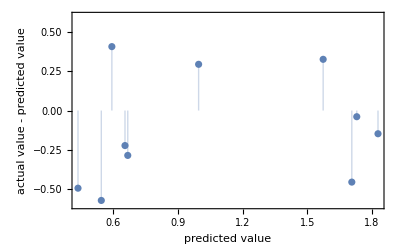
{-Graphics-,0.12973}

```mathematica
pm11/@{"ResidualPlot","MeanSquare"}
```

```mathematica
trainingDataRegression
```

(-82328.7 | -5.682 | -0.16 | 3.242 | 37.9 | 2.72
-30241. | -5.428 | -0.17 | 1.996 | 42.6 | 1.96
-19406.4 | -5.029 | 0.273 | 1.234 | 33.9 | 2.02
-20476.1 | -5.037 | 0.258 | 1.283 | 33.9 | 1.95
-31310.7 | -4.78 | 0.286 | 2.498 | 41.2 | 1.71
-29171.2 | -5.453 | -0.158 | 2.115 | 43.1 | 1.66
-29171. | -5.327 | -0.093 | 4.017 | 44.2 | 1.36
-20382.8 | -5.101 | 0.475 | 3.159 | 34.3 | 1.33
-17266.8 | -5.142 | 0.309 | 1.618 | 35.3 | 1.27
-22396.4 | -5.349 | 0.407 | 1.297 | 43.5 | 1.14
-21452.6 | -5.073 | 0.458 | 3.234 | 34.3 | 1.36
-28101.4 | -5.423 | -0.088 | 4.378 | 45. | 1.11
-21452.6 | -5.505 | 0.406 | 3.041 | 34.3 | 1.05
-19280.5 | -4.968 | 0.258 | 1.505 | 45.4 | 1.
-22522.4 | -5.063 | 0.465 | 3.276 | 34.2 | 1.38
-20382.8 | -5.505 | 0.403 | 3.089 | 35.2 | 0.87
-23498.6 | -5.703 | 0.257 | 1.288 | 34. | 0.86
-21452.5 | -5.443 | 0.389 | 2.994 | 35.1 | 0.83
-29171. | -5.499 | -0.03 | 3.92 | 44.2 | 0.84
-29171. | -5.569 | -0.07 | 3.714 | 44.2 | 0.84
-28101.4 | -5.536 | -0.049 | 4.009 | 45. | 0.81
-22396.4 | -5.281 | 0.313 | 0.427 | 43.5 | 0.76
-29171. | -5.407 | -0.075 | 4.42 | 44.2 | 0.66
-30240.9 | -5.303 | -0.082 | 4.043 | 43.6 | 0.68
-17266.9 | -5.243 | 0.522 | 2.553 | 34.7 | 0.67
-12104.5 | -5.971 | 0.37 | 1.567 | 35.2 | 0.59
-31310.5 | -5.311 | -0.088 | 4.067 | 43.1 | 0.58
-26669.7 | -5.59 | 0.079 | 3.375 | 39.8 | 0.46
-16164.5 | -5.293 | 0.309 | 1.899 | 48. | 0.41
-22522.2 | -5.435 | 0.391 | 2.947 | 35. | 0.38
-30240.9 | -5.247 | 0.286 | 3.05 | 43.6 | 0.38
-20382.8 | -5.524 | 0.388 | 3.136 | 34.3 | 0.33
-21452.6 | -5.41 | 0.384 | 2.979 | 35.1 | 0.23
-20382.7 | -5.481 | 0.39 | 3.237 | 35.2 | 0.03
-16196.9 | -5.443 | 0.406 | 3.724 | 36. | -0.67)

```mathematica
trainingSetComp
```

{{4.26288,1.00751,1.02879,0.933717,-0.409207,1.01218,0.181818,1.,1.29772,1.07062,1.24086,11.4186}→2.72,{1.56584,0.973494,0.982799,0.889077,-0.434783,0.623166,0.533597,1.00141,1.20883,1.20339,1.01218,11.4047}→1.96,{1.00484,0.919661,0.910556,0.896517,0.69821,0.385264,0.498024,1.00707,1.05705,0.957627,0.935333,12.9209}→2.02,{1.06023,0.918705,0.912004,0.895333,0.659847,0.400562,0.498024,1.00283,1.12345,0.957627,0.935333,15.3814}→1.95,{1.62123,0.988933,0.865472,0.856611,0.731458,0.779894,-0.592885,1.00707,1.27523,1.16384,1.00281,12.8419}→1.71,{1.51045,0.972947,0.987326,0.895333,-0.404092,0.660318,-0.517787,1.,1.14244,1.21751,1.03093,8.94419}→1.66,{1.51044,0.955458,0.964512,0.885019,-0.237852,1.25414,-0.865613,1.00849,1.14244,1.24859,1.03093,8.10698}→1.36,{1.0554,0.933188,0.923592,0.942847,1.21483,0.986263,1.37945,1.00849,1.06639,0.968927,0.982193,6.47442}→1.33,{0.894055,1.14128,0.931016,0.921711,0.790281,0.505151,0.525692,1.0099,0.924263,0.997175,0.961575,9.02326}→1.27,{1.15966,0.966662,0.968495,0.973115,1.04092,0.404933,1.07905,1.00849,1.13259,1.22881,1.10965,7.64651}→1.14,{1.11079,0.929499,0.918523,0.935238,1.17136,1.00968,1.39526,1.,1.13279,0.968927,0.969072,8.93488}→1.36,{1.45506,0.996311,0.981894,0.902097,-0.225064,1.36684,-0.881423,1.00141,1.07604,1.27119,1.04967,5.64651}→1.11,{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,1.13279,0.968927,0.969072,7.30698}→1.05,{0.998323,0.929499,0.899511,0.883666,0.659847,0.469872,1.28854,1.01132,0.990457,1.28249,1.10122,7.90233}→1.,{1.16618,0.944255,0.916712,0.934731,1.18926,1.02279,1.3913,1.00849,1.19918,0.966102,0.957826,11.3953}→1.38,{1.0554,0.992622,0.996741,0.998985,1.03069,0.964408,0.889328,1.0099,1.06639,0.99435,0.984067,5.86977}→0.87,{1.21673,1.00751,1.03259,1.00795,0.657289,0.402123,1.06324,1.0099,1.20852,0.960452,1.00187,2.96279}→0.86,{1.11078,0.981418,0.985515,0.985966,0.994885,0.934749,1.04348,1.0099,1.13279,0.991525,0.970947,-8.56744}→0.83,{1.51044,0.97404,0.995655,0.924586,-0.0767263,1.22385,1.1581,1.00707,1.14244,1.24859,1.03093,5.80465}→0.84,{1.51044,0.970351,1.00833,0.929828,-0.179028,1.15954,1.14229,1.00141,1.14244,1.24859,1.03093,-4.66512}→0.84,{1.45506,1.,1.00235,0.927968,-0.12532,1.25164,1.1581,0.992928,1.07604,1.27119,1.04967,3.34419}→0.81,{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.13259,1.22881,1.10965,6.0186}→0.76,{1.51044,0.962836,0.978997,0.901589,-0.191816,1.37996,-0.893281,0.997171,1.14244,1.24859,1.03093,8.10698}→0.66,{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.20883,1.23164,1.02156,10.5674}→0.68,{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,0.924263,0.980226,0.958763,-5.88372}→0.67,{0.626755,1.06695,1.08112,1.07203,0.946292,0.489229,0.70751,1.,0.706402,0.99435,0.8791,10.4233}→0.59,{1.62122,0.959147,0.961615,0.883328,-0.225064,1.26975,-0.865613,1.00707,1.27523,1.21751,1.00281,13.0279}→0.58,{1.38093,0.988933,1.01213,0.958573,0.202046,1.0537,1.05534,1.00707,1.4266,1.12429,1.02437,13.0698}→0.46,{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,0.848328,1.35593,1.08997,7.93953}→0.41,{1.16617,0.977729,0.984067,0.985289,1.,0.920075,1.04743,1.00849,1.19918,0.988701,0.958763,8.26512}→0.38,{1.56584,0.959147,0.950027,0.935577,0.731458,0.952232,1.18577,1.00566,1.20883,1.23164,1.02156,8.26512}→0.38,{1.0554,1.,1.00018,0.999662,0.992327,0.979082,0.968379,1.01697,1.06639,0.968927,0.982193,4.84651}→0.33,{1.11079,0.97404,0.97954,0.979709,0.982097,0.930066,1.02767,1.00849,1.13279,0.991525,0.970947,5.92093}→0.23,{1.05539,0.988933,0.992395,0.992898,0.997442,1.01062,0.98419,1.00849,1.06639,0.99435,0.984067,3.46047}→0.03,{0.838658,0.996311,0.985515,0.98884,1.03836,1.16266,1.21344,1.00849,0.85787,1.01695,0.975633,0.586047}→-0.67}

#### Regressing Normed Data

```mathematica
RegressionInput
```

(-82328.7 | -5.682 | -0.16 | 3.242 | 37.9 | 2.72
-30241. | -5.428 | -0.17 | 1.996 | 42.6 | 1.96
-19406.4 | -5.029 | 0.273 | 1.234 | 33.9 | 2.02
-20476.1 | -5.037 | 0.258 | 1.283 | 33.9 | 1.95
-18336.7 | -5.009 | 0.273 | 1.117 | 34.2 | 1.9
-31310.7 | -4.78 | 0.286 | 2.498 | 41.2 | 1.71
-86156.7 | -5.687 | -0.16 | 3.271 | 39.5 | 1.69
-21545.9 | -5.025 | 0.275 | 1.25 | 33.9 | 1.68
-29171.2 | -5.453 | -0.158 | 2.115 | 43.1 | 1.66
-29171. | -5.327 | -0.093 | 4.017 | 44.2 | 1.36
-20382.8 | -5.101 | 0.475 | 3.159 | 34.3 | 1.33
-18336.6 | -5.024 | 0.278 | 1.323 | 34.9 | 1.25
-30240.9 | -5.333 | -0.097 | 4.084 | 43.6 | 1.29
-17266.8 | -5.142 | 0.309 | 1.618 | 35.3 | 1.27
-22396.4 | -5.349 | 0.407 | 1.297 | 43.5 | 1.14
-21452.6 | -5.073 | 0.458 | 3.234 | 34.3 | 1.36
-28101.4 | -5.423 | -0.088 | 4.378 | 45. | 1.11
-19280.5 | -5.393 | 0.483 | 1.539 | 45.4 | 1.
-21452.6 | -5.505 | 0.406 | 3.041 | 34.3 | 1.05
-19280.5 | -4.968 | 0.258 | 1.505 | 45.4 | 1.
-22522.4 | -5.063 | 0.465 | 3.276 | 34.2 | 1.38
-20382.8 | -5.505 | 0.403 | 3.089 | 35.2 | 0.87
-23498.6 | -5.703 | 0.257 | 1.288 | 34. | 0.86
-21452.5 | -5.443 | 0.389 | 2.994 | 35.1 | 0.83
-29171. | -5.499 | -0.03 | 3.92 | 44.2 | 0.84
-29171. | -5.569 | -0.07 | 3.714 | 44.2 | 0.84
-28101.4 | -5.536 | -0.049 | 4.009 | 45. | 0.81
-22396.4 | -5.281 | 0.313 | 0.427 | 43.5 | 0.76
-29171. | -5.407 | -0.075 | 4.42 | 44.2 | 0.66
-30240.9 | -5.303 | -0.082 | 4.043 | 43.6 | 0.68
-17266.9 | -5.243 | 0.522 | 2.553 | 34.7 | 0.67
-12104.5 | -5.971 | 0.37 | 1.567 | 35.2 | 0.59
-31310.5 | -5.311 | -0.088 | 4.067 | 43.1 | 0.58
-26669.7 | -5.59 | 0.079 | 3.375 | 39.8 | 0.46
-19280.5 | -5.328 | 0.544 | 1.369 | 45.4 | 0.43
-16164.5 | -5.293 | 0.309 | 1.899 | 48. | 0.41
-22522.2 | -5.435 | 0.391 | 2.947 | 35. | 0.38
-30240.9 | -5.247 | 0.286 | 3.05 | 43.6 | 0.38
-30240.9 | -5.533 | -0.067 | 3.751 | 43.6 | 0.38
-20382.8 | -5.524 | 0.388 | 3.136 | 34.3 | 0.33
-21452.6 | -5.41 | 0.384 | 2.979 | 35.1 | 0.23
-20382.7 | -5.481 | 0.39 | 3.237 | 35.2 | 0.03
-19312.9 | -5.523 | 0.391 | 3.203 | 35.4 | 0.
-19312.8 | -5.719 | 0.288 | 1.449 | 35.4 | -0.03
-17266.8 | -5.444 | 0.405 | 3.673 | 34.7 | -0.06
-16196.9 | -5.443 | 0.406 | 3.724 | 36. | -0.67)

```mathematica
RegressionInputNormed=Transpose@ratioNormalize5[Transpose[RegressionInput][[1;;-2]],43]
```

(4.26288 | 1.02879 | -0.409207 | 1.01218 | 1.07062
1.56584 | 0.982799 | -0.434783 | 0.623166 | 1.20339
1.00484 | 0.910556 | 0.69821 | 0.385264 | 0.957627
1.06023 | 0.912004 | 0.659847 | 0.400562 | 0.957627
0.949452 | 0.906935 | 0.69821 | 0.348736 | 0.966102
1.62123 | 0.865472 | 0.731458 | 0.779894 | 1.16384
4.46109 | 1.02969 | -0.409207 | 1.02123 | 1.11582
1.11562 | 0.909832 | 0.703325 | 0.390259 | 0.957627
1.51045 | 0.987326 | -0.404092 | 0.660318 | 1.21751
1.51044 | 0.964512 | -0.237852 | 1.25414 | 1.24859
1.0554 | 0.923592 | 1.21483 | 0.986263 | 0.968927
0.949447 | 0.909651 | 0.710997 | 0.41305 | 0.985876
1.56584 | 0.965598 | -0.248082 | 1.27505 | 1.23164
0.894055 | 0.931016 | 0.790281 | 0.505151 | 0.997175
1.15966 | 0.968495 | 1.04092 | 0.404933 | 1.22881
1.11079 | 0.918523 | 1.17136 | 1.00968 | 0.968927
1.45506 | 0.981894 | -0.225064 | 1.36684 | 1.27119
0.998319 | 0.976462 | 1.23529 | 0.480487 | 1.28249
1.11079 | 0.996741 | 1.03836 | 0.949422 | 0.968927
0.998323 | 0.899511 | 0.659847 | 0.469872 | 1.28249
1.16618 | 0.916712 | 1.18926 | 1.02279 | 0.966102
1.0554 | 0.996741 | 1.03069 | 0.964408 | 0.99435
1.21673 | 1.03259 | 0.657289 | 0.402123 | 0.960452
1.11078 | 0.985515 | 0.994885 | 0.934749 | 0.991525
1.51044 | 0.995655 | -0.0767263 | 1.22385 | 1.24859
1.51044 | 1.00833 | -0.179028 | 1.15954 | 1.24859
1.45506 | 1.00235 | -0.12532 | 1.25164 | 1.27119
1.15966 | 0.956183 | 0.800512 | 0.133313 | 1.22881
1.51044 | 0.978997 | -0.191816 | 1.37996 | 1.24859
1.56584 | 0.960167 | -0.209719 | 1.26225 | 1.23164
0.894061 | 0.949303 | 1.33504 | 0.797065 | 0.980226
0.626755 | 1.08112 | 0.946292 | 0.489229 | 0.99435
1.62122 | 0.961615 | -0.225064 | 1.26975 | 1.21751
1.38093 | 1.01213 | 0.202046 | 1.0537 | 1.12429
0.998319 | 0.964693 | 1.3913 | 0.427412 | 1.28249
0.836977 | 0.958356 | 0.790281 | 0.592882 | 1.35593
1.16617 | 0.984067 | 1. | 0.920075 | 0.988701
1.56584 | 0.950027 | 0.731458 | 0.952232 | 1.23164
1.56584 | 1.00181 | -0.171355 | 1.17109 | 1.23164
1.0554 | 1.00018 | 0.992327 | 0.979082 | 0.968927
1.11079 | 0.97954 | 0.982097 | 0.930066 | 0.991525
1.05539 | 0.992395 | 0.997442 | 1.01062 | 0.99435
1. | 1. | 1. | 1. | 1.
0.999993 | 1.03549 | 0.736573 | 0.452388 | 1.
0.894052 | 0.985696 | 1.03581 | 1.14674 | 0.980226
0.838658 | 0.985515 | 1.03836 | 1.16266 | 1.01695)

```mathematica
Dimensions[%]
```

{46,5}

```mathematica
NormedInputFinal=ReplacePart[RegressionInputNormed,43->Nothing]
```

(4.26288 | 1.02879 | -0.409207 | 1.01218 | 1.07062
1.56584 | 0.982799 | -0.434783 | 0.623166 | 1.20339
1.00484 | 0.910556 | 0.69821 | 0.385264 | 0.957627
1.06023 | 0.912004 | 0.659847 | 0.400562 | 0.957627
0.949452 | 0.906935 | 0.69821 | 0.348736 | 0.966102
1.62123 | 0.865472 | 0.731458 | 0.779894 | 1.16384
4.46109 | 1.02969 | -0.409207 | 1.02123 | 1.11582
1.11562 | 0.909832 | 0.703325 | 0.390259 | 0.957627
1.51045 | 0.987326 | -0.404092 | 0.660318 | 1.21751
1.51044 | 0.964512 | -0.237852 | 1.25414 | 1.24859
1.0554 | 0.923592 | 1.21483 | 0.986263 | 0.968927
0.949447 | 0.909651 | 0.710997 | 0.41305 | 0.985876
1.56584 | 0.965598 | -0.248082 | 1.27505 | 1.23164
0.894055 | 0.931016 | 0.790281 | 0.505151 | 0.997175
1.15966 | 0.968495 | 1.04092 | 0.404933 | 1.22881
1.11079 | 0.918523 | 1.17136 | 1.00968 | 0.968927
1.45506 | 0.981894 | -0.225064 | 1.36684 | 1.27119
0.998319 | 0.976462 | 1.23529 | 0.480487 | 1.28249
1.11079 | 0.996741 | 1.03836 | 0.949422 | 0.968927
0.998323 | 0.899511 | 0.659847 | 0.469872 | 1.28249
1.16618 | 0.916712 | 1.18926 | 1.02279 | 0.966102
1.0554 | 0.996741 | 1.03069 | 0.964408 | 0.99435
1.21673 | 1.03259 | 0.657289 | 0.402123 | 0.960452
1.11078 | 0.985515 | 0.994885 | 0.934749 | 0.991525
1.51044 | 0.995655 | -0.0767263 | 1.22385 | 1.24859
1.51044 | 1.00833 | -0.179028 | 1.15954 | 1.24859
1.45506 | 1.00235 | -0.12532 | 1.25164 | 1.27119
1.15966 | 0.956183 | 0.800512 | 0.133313 | 1.22881
1.51044 | 0.978997 | -0.191816 | 1.37996 | 1.24859
1.56584 | 0.960167 | -0.209719 | 1.26225 | 1.23164
0.894061 | 0.949303 | 1.33504 | 0.797065 | 0.980226
0.626755 | 1.08112 | 0.946292 | 0.489229 | 0.99435
1.62122 | 0.961615 | -0.225064 | 1.26975 | 1.21751
1.38093 | 1.01213 | 0.202046 | 1.0537 | 1.12429
0.998319 | 0.964693 | 1.3913 | 0.427412 | 1.28249
0.836977 | 0.958356 | 0.790281 | 0.592882 | 1.35593
1.16617 | 0.984067 | 1. | 0.920075 | 0.988701
1.56584 | 0.950027 | 0.731458 | 0.952232 | 1.23164
1.56584 | 1.00181 | -0.171355 | 1.17109 | 1.23164
1.0554 | 1.00018 | 0.992327 | 0.979082 | 0.968927
1.11079 | 0.97954 | 0.982097 | 0.930066 | 0.991525
1.05539 | 0.992395 | 0.997442 | 1.01062 | 0.99435
0.999993 | 1.03549 | 0.736573 | 0.452388 | 1.
0.894052 | 0.985696 | 1.03581 | 1.14674 | 0.980226
0.838658 | 0.985515 | 1.03836 | 1.16266 | 1.01695)

```mathematica
NormedFiveVariables=Transpose@Join[Transpose[NormedInputFinal],{LogMUsInput}]
```

(4.26288 | 1.02879 | -0.409207 | 1.01218 | 1.07062 | 2.72
1.56584 | 0.982799 | -0.434783 | 0.623166 | 1.20339 | 1.96
1.00484 | 0.910556 | 0.69821 | 0.385264 | 0.957627 | 2.02
1.06023 | 0.912004 | 0.659847 | 0.400562 | 0.957627 | 1.95
0.949452 | 0.906935 | 0.69821 | 0.348736 | 0.966102 | 1.9
1.62123 | 0.865472 | 0.731458 | 0.779894 | 1.16384 | 1.71
4.46109 | 1.02969 | -0.409207 | 1.02123 | 1.11582 | 1.69
1.11562 | 0.909832 | 0.703325 | 0.390259 | 0.957627 | 1.68
1.51045 | 0.987326 | -0.404092 | 0.660318 | 1.21751 | 1.66
1.51044 | 0.964512 | -0.237852 | 1.25414 | 1.24859 | 1.36
1.0554 | 0.923592 | 1.21483 | 0.986263 | 0.968927 | 1.33
0.949447 | 0.909651 | 0.710997 | 0.41305 | 0.985876 | 1.25
1.56584 | 0.965598 | -0.248082 | 1.27505 | 1.23164 | 1.29
0.894055 | 0.931016 | 0.790281 | 0.505151 | 0.997175 | 1.27
1.15966 | 0.968495 | 1.04092 | 0.404933 | 1.22881 | 1.14
1.11079 | 0.918523 | 1.17136 | 1.00968 | 0.968927 | 1.36
1.45506 | 0.981894 | -0.225064 | 1.36684 | 1.27119 | 1.11
0.998319 | 0.976462 | 1.23529 | 0.480487 | 1.28249 | 1.
1.11079 | 0.996741 | 1.03836 | 0.949422 | 0.968927 | 1.05
0.998323 | 0.899511 | 0.659847 | 0.469872 | 1.28249 | 1.
1.16618 | 0.916712 | 1.18926 | 1.02279 | 0.966102 | 1.38
1.0554 | 0.996741 | 1.03069 | 0.964408 | 0.99435 | 0.87
1.21673 | 1.03259 | 0.657289 | 0.402123 | 0.960452 | 0.86
1.11078 | 0.985515 | 0.994885 | 0.934749 | 0.991525 | 0.83
1.51044 | 0.995655 | -0.0767263 | 1.22385 | 1.24859 | 0.84
1.51044 | 1.00833 | -0.179028 | 1.15954 | 1.24859 | 0.84
1.45506 | 1.00235 | -0.12532 | 1.25164 | 1.27119 | 0.81
1.15966 | 0.956183 | 0.800512 | 0.133313 | 1.22881 | 0.76
1.51044 | 0.978997 | -0.191816 | 1.37996 | 1.24859 | 0.66
1.56584 | 0.960167 | -0.209719 | 1.26225 | 1.23164 | 0.68
0.894061 | 0.949303 | 1.33504 | 0.797065 | 0.980226 | 0.67
0.626755 | 1.08112 | 0.946292 | 0.489229 | 0.99435 | 0.59
1.62122 | 0.961615 | -0.225064 | 1.26975 | 1.21751 | 0.58
1.38093 | 1.01213 | 0.202046 | 1.0537 | 1.12429 | 0.46
0.998319 | 0.964693 | 1.3913 | 0.427412 | 1.28249 | 0.43
0.836977 | 0.958356 | 0.790281 | 0.592882 | 1.35593 | 0.41
1.16617 | 0.984067 | 1. | 0.920075 | 0.988701 | 0.38
1.56584 | 0.950027 | 0.731458 | 0.952232 | 1.23164 | 0.38
1.56584 | 1.00181 | -0.171355 | 1.17109 | 1.23164 | 0.38
1.0554 | 1.00018 | 0.992327 | 0.979082 | 0.968927 | 0.33
1.11079 | 0.97954 | 0.982097 | 0.930066 | 0.991525 | 0.23
1.05539 | 0.992395 | 0.997442 | 1.01062 | 0.99435 | 0.03
0.999993 | 1.03549 | 0.736573 | 0.452388 | 1. | -0.03
0.894052 | 0.985696 | 1.03581 | 1.14674 | 0.980226 | -0.06
0.838658 | 0.985515 | 1.03836 | 1.16266 | 1.01695 | -0.67)

```mathematica
NormedRegressionTraining=NormedFiveVariables[[trainingIndicesRegression]]
```

(4.26288 | 1.02879 | -0.409207 | 1.01218 | 1.07062 | 2.72
1.56584 | 0.982799 | -0.434783 | 0.623166 | 1.20339 | 1.96
1.00484 | 0.910556 | 0.69821 | 0.385264 | 0.957627 | 2.02
1.06023 | 0.912004 | 0.659847 | 0.400562 | 0.957627 | 1.95
1.62123 | 0.865472 | 0.731458 | 0.779894 | 1.16384 | 1.71
1.51045 | 0.987326 | -0.404092 | 0.660318 | 1.21751 | 1.66
1.51044 | 0.964512 | -0.237852 | 1.25414 | 1.24859 | 1.36
1.0554 | 0.923592 | 1.21483 | 0.986263 | 0.968927 | 1.33
0.894055 | 0.931016 | 0.790281 | 0.505151 | 0.997175 | 1.27
1.15966 | 0.968495 | 1.04092 | 0.404933 | 1.22881 | 1.14
1.11079 | 0.918523 | 1.17136 | 1.00968 | 0.968927 | 1.36
1.45506 | 0.981894 | -0.225064 | 1.36684 | 1.27119 | 1.11
1.11079 | 0.996741 | 1.03836 | 0.949422 | 0.968927 | 1.05
0.998323 | 0.899511 | 0.659847 | 0.469872 | 1.28249 | 1.
1.16618 | 0.916712 | 1.18926 | 1.02279 | 0.966102 | 1.38
1.0554 | 0.996741 | 1.03069 | 0.964408 | 0.99435 | 0.87
1.21673 | 1.03259 | 0.657289 | 0.402123 | 0.960452 | 0.86
1.11078 | 0.985515 | 0.994885 | 0.934749 | 0.991525 | 0.83
1.51044 | 0.995655 | -0.0767263 | 1.22385 | 1.24859 | 0.84
1.51044 | 1.00833 | -0.179028 | 1.15954 | 1.24859 | 0.84
1.45506 | 1.00235 | -0.12532 | 1.25164 | 1.27119 | 0.81
1.15966 | 0.956183 | 0.800512 | 0.133313 | 1.22881 | 0.76
1.51044 | 0.978997 | -0.191816 | 1.37996 | 1.24859 | 0.66
1.56584 | 0.960167 | -0.209719 | 1.26225 | 1.23164 | 0.68
0.894061 | 0.949303 | 1.33504 | 0.797065 | 0.980226 | 0.67
0.626755 | 1.08112 | 0.946292 | 0.489229 | 0.99435 | 0.59
1.62122 | 0.961615 | -0.225064 | 1.26975 | 1.21751 | 0.58
1.38093 | 1.01213 | 0.202046 | 1.0537 | 1.12429 | 0.46
0.836977 | 0.958356 | 0.790281 | 0.592882 | 1.35593 | 0.41
1.16617 | 0.984067 | 1. | 0.920075 | 0.988701 | 0.38
1.56584 | 0.950027 | 0.731458 | 0.952232 | 1.23164 | 0.38
1.0554 | 1.00018 | 0.992327 | 0.979082 | 0.968927 | 0.33
1.11079 | 0.97954 | 0.982097 | 0.930066 | 0.991525 | 0.23
1.05539 | 0.992395 | 0.997442 | 1.01062 | 0.99435 | 0.03
0.838658 | 0.985515 | 1.03836 | 1.16266 | 1.01695 | -0.67)

```mathematica
NormedRegressionTesting=NormedFiveVariables[[testIndicesRegression]]
```

(0.949452 | 0.906935 | 0.69821 | 0.348736 | 0.966102 | 1.9
4.46109 | 1.02969 | -0.409207 | 1.02123 | 1.11582 | 1.69
1.11562 | 0.909832 | 0.703325 | 0.390259 | 0.957627 | 1.68
0.949447 | 0.909651 | 0.710997 | 0.41305 | 0.985876 | 1.25
1.56584 | 0.965598 | -0.248082 | 1.27505 | 1.23164 | 1.29
0.998319 | 0.976462 | 1.23529 | 0.480487 | 1.28249 | 1.
0.998319 | 0.964693 | 1.3913 | 0.427412 | 1.28249 | 0.43
1.56584 | 1.00181 | -0.171355 | 1.17109 | 1.23164 | 0.38
0.999993 | 1.03549 | 0.736573 | 0.452388 | 1. | -0.03
0.894052 | 0.985696 | 1.03581 | 1.14674 | 0.980226 | -0.06)

```mathematica
pnl2=NonlinearModelFit[NormedRegressionTraining,a+b x1+c x2+d x3+e x4+f x5+g x1^2+h x2^2+n x3^2+m x4^2+k x5^2,{a,b,c,d,e,f,g,h,n,m,k},
{x1,x2,x3,x4,x5}]
```

FittedModel[88.596+«14»+19.0282 x5^2]

```mathematica
predicted2=Map[
pnl2["BestFit"]/.Thread[{x1,x2,x3,x4,x5,output}->#]&,
NormedRegressionTesting
]
```

{1.77166,2.51281,1.94936,1.51123,1.02276,0.598587,0.889935,0.834278,0.72927,0.136867}

```mathematica
Thread[(predicted2-testResultsRegression)^2]
```

{0.0164701,0.677014,0.0725564,0.0682387,0.0714193,0.161132,0.21154,0.206368,0.57649,0.0387568}

```mathematica
Mean[%]
```

0.209999

```mathematica
FiveTraining=NormedFiveVariables[[trainingIndicesRegression]]
```

(4.26288 | 1.02879 | -0.409207 | 1.01218 | 1.07062 | 2.72
1.56584 | 0.982799 | -0.434783 | 0.623166 | 1.20339 | 1.96
1.00484 | 0.910556 | 0.69821 | 0.385264 | 0.957627 | 2.02
1.06023 | 0.912004 | 0.659847 | 0.400562 | 0.957627 | 1.95
1.62123 | 0.865472 | 0.731458 | 0.779894 | 1.16384 | 1.71
1.51045 | 0.987326 | -0.404092 | 0.660318 | 1.21751 | 1.66
1.51044 | 0.964512 | -0.237852 | 1.25414 | 1.24859 | 1.36
1.0554 | 0.923592 | 1.21483 | 0.986263 | 0.968927 | 1.33
0.894055 | 0.931016 | 0.790281 | 0.505151 | 0.997175 | 1.27
1.15966 | 0.968495 | 1.04092 | 0.404933 | 1.22881 | 1.14
1.11079 | 0.918523 | 1.17136 | 1.00968 | 0.968927 | 1.36
1.45506 | 0.981894 | -0.225064 | 1.36684 | 1.27119 | 1.11
1.11079 | 0.996741 | 1.03836 | 0.949422 | 0.968927 | 1.05
0.998323 | 0.899511 | 0.659847 | 0.469872 | 1.28249 | 1.
1.16618 | 0.916712 | 1.18926 | 1.02279 | 0.966102 | 1.38
1.0554 | 0.996741 | 1.03069 | 0.964408 | 0.99435 | 0.87
1.21673 | 1.03259 | 0.657289 | 0.402123 | 0.960452 | 0.86
1.11078 | 0.985515 | 0.994885 | 0.934749 | 0.991525 | 0.83
1.51044 | 0.995655 | -0.0767263 | 1.22385 | 1.24859 | 0.84
1.51044 | 1.00833 | -0.179028 | 1.15954 | 1.24859 | 0.84
1.45506 | 1.00235 | -0.12532 | 1.25164 | 1.27119 | 0.81
1.15966 | 0.956183 | 0.800512 | 0.133313 | 1.22881 | 0.76
1.51044 | 0.978997 | -0.191816 | 1.37996 | 1.24859 | 0.66
1.56584 | 0.960167 | -0.209719 | 1.26225 | 1.23164 | 0.68
0.894061 | 0.949303 | 1.33504 | 0.797065 | 0.980226 | 0.67
0.626755 | 1.08112 | 0.946292 | 0.489229 | 0.99435 | 0.59
1.62122 | 0.961615 | -0.225064 | 1.26975 | 1.21751 | 0.58
1.38093 | 1.01213 | 0.202046 | 1.0537 | 1.12429 | 0.46
0.836977 | 0.958356 | 0.790281 | 0.592882 | 1.35593 | 0.41
1.16617 | 0.984067 | 1. | 0.920075 | 0.988701 | 0.38
1.56584 | 0.950027 | 0.731458 | 0.952232 | 1.23164 | 0.38
1.0554 | 1.00018 | 0.992327 | 0.979082 | 0.968927 | 0.33
1.11079 | 0.97954 | 0.982097 | 0.930066 | 0.991525 | 0.23
1.05539 | 0.992395 | 0.997442 | 1.01062 | 0.99435 | 0.03
0.838658 | 0.985515 | 1.03836 | 1.16266 | 1.01695 | -0.67)

```mathematica
FiveTesting=NormedFiveVariables[[testIndicesRegression]]
```

{{0.949452,0.906935,0.69821,0.348736,0.966102,1.9},{4.46109,1.02969,-0.409207,1.02123,1.11582,1.69},{1.11562,0.909832,0.703325,0.390259,0.957627,1.68},{0.949447,0.909651,0.710997,0.41305,0.985876,1.25},{1.56584,0.965598,-0.248082,1.27505,1.23164,1.29},{0.998319,0.976462,1.23529,0.480487,1.28249,1.},{0.998319,0.964693,1.3913,0.427412,1.28249,0.43},{1.56584,1.00181,-0.171355,1.17109,1.23164,0.38},{0.999993,1.03549,0.736573,0.452388,1.,-0.03},{0.894052,0.985696,1.03581,1.14674,0.980226,-0.06}}

```mathematica
FiveTrainingSet=Thread[FiveTraining[[All,1;;-2]]->FiveTraining[[All,-1]]]
```

{{4.26288,1.02879,-0.409207,1.01218,1.07062}→2.72,{1.56584,0.982799,-0.434783,0.623166,1.20339}→1.96,{1.00484,0.910556,0.69821,0.385264,0.957627}→2.02,{1.06023,0.912004,0.659847,0.400562,0.957627}→1.95,{1.62123,0.865472,0.731458,0.779894,1.16384}→1.71,{1.51045,0.987326,-0.404092,0.660318,1.21751}→1.66,{1.51044,0.964512,-0.237852,1.25414,1.24859}→1.36,{1.0554,0.923592,1.21483,0.986263,0.968927}→1.33,{0.894055,0.931016,0.790281,0.505151,0.997175}→1.27,{1.15966,0.968495,1.04092,0.404933,1.22881}→1.14,{1.11079,0.918523,1.17136,1.00968,0.968927}→1.36,{1.45506,0.981894,-0.225064,1.36684,1.27119}→1.11,{1.11079,0.996741,1.03836,0.949422,0.968927}→1.05,{0.998323,0.899511,0.659847,0.469872,1.28249}→1.,{1.16618,0.916712,1.18926,1.02279,0.966102}→1.38,{1.0554,0.996741,1.03069,0.964408,0.99435}→0.87,{1.21673,1.03259,0.657289,0.402123,0.960452}→0.86,{1.11078,0.985515,0.994885,0.934749,0.991525}→0.83,{1.51044,0.995655,-0.0767263,1.22385,1.24859}→0.84,{1.51044,1.00833,-0.179028,1.15954,1.24859}→0.84,{1.45506,1.00235,-0.12532,1.25164,1.27119}→0.81,{1.15966,0.956183,0.800512,0.133313,1.22881}→0.76,{1.51044,0.978997,-0.191816,1.37996,1.24859}→0.66,{1.56584,0.960167,-0.209719,1.26225,1.23164}→0.68,{0.894061,0.949303,1.33504,0.797065,0.980226}→0.67,{0.626755,1.08112,0.946292,0.489229,0.99435}→0.59,{1.62122,0.961615,-0.225064,1.26975,1.21751}→0.58,{1.38093,1.01213,0.202046,1.0537,1.12429}→0.46,{0.836977,0.958356,0.790281,0.592882,1.35593}→0.41,{1.16617,0.984067,1.,0.920075,0.988701}→0.38,{1.56584,0.950027,0.731458,0.952232,1.23164}→0.38,{1.0554,1.00018,0.992327,0.979082,0.968927}→0.33,{1.11079,0.97954,0.982097,0.930066,0.991525}→0.23,{1.05539,0.992395,0.997442,1.01062,0.99435}→0.03,{0.838658,0.985515,1.03836,1.16266,1.01695}→-0.67}

```mathematica
FiveTestingSet=Thread[FiveTesting[[All,1;;-2]]->FiveTesting[[All,-1]]]
```

{{0.949452,0.906935,0.69821,0.348736,0.966102}→1.9,{4.46109,1.02969,-0.409207,1.02123,1.11582}→1.69,{1.11562,0.909832,0.703325,0.390259,0.957627}→1.68,{0.949447,0.909651,0.710997,0.41305,0.985876}→1.25,{1.56584,0.965598,-0.248082,1.27505,1.23164}→1.29,{0.998319,0.976462,1.23529,0.480487,1.28249}→1.,{0.998319,0.964693,1.3913,0.427412,1.28249}→0.43,{1.56584,1.00181,-0.171355,1.17109,1.23164}→0.38,{0.999993,1.03549,0.736573,0.452388,1.}→-0.03,{0.894052,0.985696,1.03581,1.14674,0.980226}→-0.06}

```mathematica
pFive=Predict[FiveTrainingSet,Method->{"RandomForest","LeafSize"->1,"DistributionSmoothing"->0.3}]
```

PredictorFunction[…]

```mathematica
pmFive=PredictorMeasurements[pFive,FiveTestingSet]
```

PredictorMeasurementsObject[…]

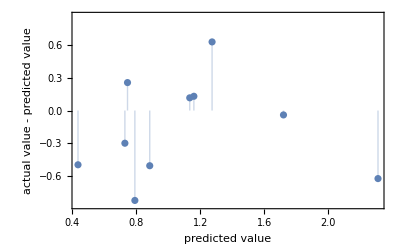
{-Graphics-,0.213721}

```mathematica
pmFive/@{"ResidualPlot","MeanSquare"}
```

```mathematica
TwelveRegressInput=Transpose@Join[Transpose[InputFinal],{LogMUsInput}]
```

(4.26288 | 1.00751 | 1.02879 | 0.933717 | -0.409207 | 1.01218 | 0.181818 | 1. | 1.29772 | 1.07062 | 1.24086 | 11.4186 | 2.72
1.56584 | 0.973494 | 0.982799 | 0.889077 | -0.434783 | 0.623166 | 0.533597 | 1.00141 | 1.20883 | 1.20339 | 1.01218 | 11.4047 | 1.96
1.00484 | 0.919661 | 0.910556 | 0.896517 | 0.69821 | 0.385264 | 0.498024 | 1.00707 | 1.05705 | 0.957627 | 0.935333 | 12.9209 | 2.02
1.06023 | 0.918705 | 0.912004 | 0.895333 | 0.659847 | 0.400562 | 0.498024 | 1.00283 | 1.12345 | 0.957627 | 0.935333 | 15.3814 | 1.95
0.949452 | 0.924307 | 0.906935 | 0.893135 | 0.69821 | 0.348736 | 0.501976 | 1.00424 | 0.990661 | 0.966102 | 0.946579 | 10.4605 | 1.9
1.62123 | 0.988933 | 0.865472 | 0.856611 | 0.731458 | 0.779894 | -0.592885 | 1.00707 | 1.27523 | 1.16384 | 1.00281 | 12.8419 | 1.71
4.46109 | 1.00751 | 1.02969 | 0.934562 | -0.409207 | 1.02123 | 0.181818 | 1.00283 | 1.23133 | 1.11582 | 1.2821 | 9.9814 | 1.69
1.11562 | 0.918295 | 0.909832 | 0.896179 | 0.703325 | 0.390259 | 0.482213 | 1.00849 | 1.18985 | 0.957627 | 0.917526 | 15.7488 | 1.68
1.51045 | 0.972947 | 0.987326 | 0.895333 | -0.404092 | 0.660318 | -0.517787 | 1. | 1.14244 | 1.21751 | 1.03093 | 8.94419 | 1.66
1.51044 | 0.955458 | 0.964512 | 0.885019 | -0.237852 | 1.25414 | -0.865613 | 1.00849 | 1.14244 | 1.24859 | 1.03093 | 8.10698 | 1.36
1.0554 | 0.933188 | 0.923592 | 0.942847 | 1.21483 | 0.986263 | 1.37945 | 1.00849 | 1.06639 | 0.968927 | 0.982193 | 6.47442 | 1.33
0.949447 | 0.929362 | 0.909651 | 0.896348 | 0.710997 | 0.41305 | 0.494071 | 1.01273 | 0.990661 | 0.985876 | 0.948454 | 11.4837 | 1.25
1.56584 | 0.977729 | 0.965598 | 0.885357 | -0.248082 | 1.27505 | -0.869565 | 1. | 1.20883 | 1.23164 | 1.02156 | 10.5674 | 1.29
0.894055 | 1.14128 | 0.931016 | 0.921711 | 0.790281 | 0.505151 | 0.525692 | 1.0099 | 0.924263 | 0.997175 | 0.961575 | 9.02326 | 1.27
1.15966 | 0.966662 | 0.968495 | 0.973115 | 1.04092 | 0.404933 | 1.07905 | 1.00849 | 1.13259 | 1.22881 | 1.10965 | 7.64651 | 1.14
1.11079 | 0.929499 | 0.918523 | 0.935238 | 1.17136 | 1.00968 | 1.39526 | 1. | 1.13279 | 0.968927 | 0.969072 | 8.93488 | 1.36
1.45506 | 0.996311 | 0.981894 | 0.902097 | -0.225064 | 1.36684 | -0.881423 | 1.00141 | 1.07604 | 1.27119 | 1.04967 | 5.64651 | 1.11
0.998319 | 0.992622 | 0.976462 | 0.993575 | 1.23529 | 0.480487 | 1.28854 | 1. | 0.990457 | 1.28249 | 1.10122 | 7.90233 | 1.
1.11079 | 0.992622 | 0.996741 | 0.999493 | 1.03836 | 0.949422 | 1.04743 | 1.00849 | 1.13279 | 0.968927 | 0.969072 | 7.30698 | 1.05
0.998323 | 0.929499 | 0.899511 | 0.883666 | 0.659847 | 0.469872 | 1.28854 | 1.01132 | 0.990457 | 1.28249 | 1.10122 | 7.90233 | 1.
1.16618 | 0.944255 | 0.916712 | 0.934731 | 1.18926 | 1.02279 | 1.3913 | 1.00849 | 1.19918 | 0.966102 | 0.957826 | 11.3953 | 1.38
1.0554 | 0.992622 | 0.996741 | 0.998985 | 1.03069 | 0.964408 | 0.889328 | 1.0099 | 1.06639 | 0.99435 | 0.984067 | 5.86977 | 0.87
1.21673 | 1.00751 | 1.03259 | 1.00795 | 0.657289 | 0.402123 | 1.06324 | 1.0099 | 1.20852 | 0.960452 | 1.00187 | 2.96279 | 0.86
1.11078 | 0.981418 | 0.985515 | 0.985966 | 0.994885 | 0.934749 | 1.04348 | 1.0099 | 1.13279 | 0.991525 | 0.970947 | -8.56744 | 0.83
1.51044 | 0.97404 | 0.995655 | 0.924586 | -0.0767263 | 1.22385 | 1.1581 | 1.00707 | 1.14244 | 1.24859 | 1.03093 | 5.80465 | 0.84
1.51044 | 0.970351 | 1.00833 | 0.929828 | -0.179028 | 1.15954 | 1.14229 | 1.00141 | 1.14244 | 1.24859 | 1.03093 | -4.66512 | 0.84
1.45506 | 1. | 1.00235 | 0.927968 | -0.12532 | 1.25164 | 1.1581 | 0.992928 | 1.07604 | 1.27119 | 1.04967 | 3.34419 | 0.81
1.15966 | 0.959147 | 0.956183 | 0.945891 | 0.800512 | 0.133313 | 1.11858 | 0.992928 | 1.13259 | 1.22881 | 1.10965 | 6.0186 | 0.76
1.51044 | 0.962836 | 0.978997 | 0.901589 | -0.191816 | 1.37996 | -0.893281 | 0.997171 | 1.14244 | 1.24859 | 1.03093 | 8.10698 | 0.66
1.56584 | 0.959147 | 0.960167 | 0.88282 | -0.209719 | 1.26225 | -0.87747 | 1.00849 | 1.20883 | 1.23164 | 1.02156 | 10.5674 | 0.68
0.894061 | 0.962836 | 0.949303 | 0.974806 | 1.33504 | 0.797065 | 1.49407 | 1.00849 | 0.924263 | 0.980226 | 0.958763 | -5.88372 | 0.67
0.626755 | 1.06695 | 1.08112 | 1.07203 | 0.946292 | 0.489229 | 0.70751 | 1. | 0.706402 | 0.99435 | 0.8791 | 10.4233 | 0.59
1.62122 | 0.959147 | 0.961615 | 0.883328 | -0.225064 | 1.26975 | -0.865613 | 1.00707 | 1.27523 | 1.21751 | 1.00281 | 13.0279 | 0.58
1.38093 | 0.988933 | 1.01213 | 0.958573 | 0.202046 | 1.0537 | 1.05534 | 1.00707 | 1.4266 | 1.12429 | 1.02437 | 13.0698 | 0.46
0.998319 | 0.985244 | 0.964693 | 0.992898 | 1.3913 | 0.427412 | 1.04743 | 1.00849 | 0.990457 | 1.28249 | 1.10122 | 7.90233 | 0.43
0.836977 | 0.985244 | 0.958356 | 0.947244 | 0.790281 | 0.592882 | 1.3004 | 1.00141 | 0.848328 | 1.35593 | 1.08997 | 7.93953 | 0.41
1.16617 | 0.977729 | 0.984067 | 0.985289 | 1. | 0.920075 | 1.04743 | 1.00849 | 1.19918 | 0.988701 | 0.958763 | 8.26512 | 0.38
1.56584 | 0.959147 | 0.950027 | 0.935577 | 0.731458 | 0.952232 | 1.18577 | 1.00566 | 1.20883 | 1.23164 | 1.02156 | 8.26512 | 0.38
1.56584 | 0.977729 | 1.00181 | 0.924248 | -0.171355 | 1.17109 | 1.12648 | 1.00424 | 1.20883 | 1.23164 | 1.02156 | 8.26512 | 0.38
1.0554 | 1. | 1.00018 | 0.999662 | 0.992327 | 0.979082 | 0.968379 | 1.01697 | 1.06639 | 0.968927 | 0.982193 | 4.84651 | 0.33
1.11079 | 0.97404 | 0.97954 | 0.979709 | 0.982097 | 0.930066 | 1.02767 | 1.00849 | 1.13279 | 0.991525 | 0.970947 | 5.92093 | 0.23
1.05539 | 0.988933 | 0.992395 | 0.992898 | 0.997442 | 1.01062 | 0.98419 | 1.00849 | 1.06639 | 0.99435 | 0.984067 | 3.46047 | 0.03
0.999993 | 1.01872 | 1.03549 | 1.01573 | 0.736573 | 0.452388 | 1.20553 | 1.00424 | 1. | 1. | 1. | -14.3256 | -0.03
0.894052 | 0.996311 | 0.985696 | 0.989009 | 1.03581 | 1.14674 | 1.21739 | 1.01414 | 0.924263 | 0.980226 | 0.958763 | 2.02326 | -0.06
0.838658 | 0.996311 | 0.985515 | 0.98884 | 1.03836 | 1.16266 | 1.21344 | 1.00849 | 0.85787 | 1.01695 | 0.975633 | 0.586047 | -0.67)

```mathematica
TwelveTraining=TwelveRegressInput[[trainingIndicesRegression]]
```

(4.26288 | 1.00751 | 1.02879 | 0.933717 | -0.409207 | 1.01218 | 0.181818 | 1. | 1.29772 | 1.07062 | 1.24086 | 11.4186 | 2.72
1.56584 | 0.973494 | 0.982799 | 0.889077 | -0.434783 | 0.623166 | 0.533597 | 1.00141 | 1.20883 | 1.20339 | 1.01218 | 11.4047 | 1.96
1.00484 | 0.919661 | 0.910556 | 0.896517 | 0.69821 | 0.385264 | 0.498024 | 1.00707 | 1.05705 | 0.957627 | 0.935333 | 12.9209 | 2.02
1.06023 | 0.918705 | 0.912004 | 0.895333 | 0.659847 | 0.400562 | 0.498024 | 1.00283 | 1.12345 | 0.957627 | 0.935333 | 15.3814 | 1.95
1.62123 | 0.988933 | 0.865472 | 0.856611 | 0.731458 | 0.779894 | -0.592885 | 1.00707 | 1.27523 | 1.16384 | 1.00281 | 12.8419 | 1.71
1.51045 | 0.972947 | 0.987326 | 0.895333 | -0.404092 | 0.660318 | -0.517787 | 1. | 1.14244 | 1.21751 | 1.03093 | 8.94419 | 1.66
1.51044 | 0.955458 | 0.964512 | 0.885019 | -0.237852 | 1.25414 | -0.865613 | 1.00849 | 1.14244 | 1.24859 | 1.03093 | 8.10698 | 1.36
1.0554 | 0.933188 | 0.923592 | 0.942847 | 1.21483 | 0.986263 | 1.37945 | 1.00849 | 1.06639 | 0.968927 | 0.982193 | 6.47442 | 1.33
0.894055 | 1.14128 | 0.931016 | 0.921711 | 0.790281 | 0.505151 | 0.525692 | 1.0099 | 0.924263 | 0.997175 | 0.961575 | 9.02326 | 1.27
1.15966 | 0.966662 | 0.968495 | 0.973115 | 1.04092 | 0.404933 | 1.07905 | 1.00849 | 1.13259 | 1.22881 | 1.10965 | 7.64651 | 1.14
1.11079 | 0.929499 | 0.918523 | 0.935238 | 1.17136 | 1.00968 | 1.39526 | 1. | 1.13279 | 0.968927 | 0.969072 | 8.93488 | 1.36
1.45506 | 0.996311 | 0.981894 | 0.902097 | -0.225064 | 1.36684 | -0.881423 | 1.00141 | 1.07604 | 1.27119 | 1.04967 | 5.64651 | 1.11
1.11079 | 0.992622 | 0.996741 | 0.999493 | 1.03836 | 0.949422 | 1.04743 | 1.00849 | 1.13279 | 0.968927 | 0.969072 | 7.30698 | 1.05
0.998323 | 0.929499 | 0.899511 | 0.883666 | 0.659847 | 0.469872 | 1.28854 | 1.01132 | 0.990457 | 1.28249 | 1.10122 | 7.90233 | 1.
1.16618 | 0.944255 | 0.916712 | 0.934731 | 1.18926 | 1.02279 | 1.3913 | 1.00849 | 1.19918 | 0.966102 | 0.957826 | 11.3953 | 1.38
1.0554 | 0.992622 | 0.996741 | 0.998985 | 1.03069 | 0.964408 | 0.889328 | 1.0099 | 1.06639 | 0.99435 | 0.984067 | 5.86977 | 0.87
1.21673 | 1.00751 | 1.03259 | 1.00795 | 0.657289 | 0.402123 | 1.06324 | 1.0099 | 1.20852 | 0.960452 | 1.00187 | 2.96279 | 0.86
1.11078 | 0.981418 | 0.985515 | 0.985966 | 0.994885 | 0.934749 | 1.04348 | 1.0099 | 1.13279 | 0.991525 | 0.970947 | -8.56744 | 0.83
1.51044 | 0.97404 | 0.995655 | 0.924586 | -0.0767263 | 1.22385 | 1.1581 | 1.00707 | 1.14244 | 1.24859 | 1.03093 | 5.80465 | 0.84
1.51044 | 0.970351 | 1.00833 | 0.929828 | -0.179028 | 1.15954 | 1.14229 | 1.00141 | 1.14244 | 1.24859 | 1.03093 | -4.66512 | 0.84
1.45506 | 1. | 1.00235 | 0.927968 | -0.12532 | 1.25164 | 1.1581 | 0.992928 | 1.07604 | 1.27119 | 1.04967 | 3.34419 | 0.81
1.15966 | 0.959147 | 0.956183 | 0.945891 | 0.800512 | 0.133313 | 1.11858 | 0.992928 | 1.13259 | 1.22881 | 1.10965 | 6.0186 | 0.76
1.51044 | 0.962836 | 0.978997 | 0.901589 | -0.191816 | 1.37996 | -0.893281 | 0.997171 | 1.14244 | 1.24859 | 1.03093 | 8.10698 | 0.66
1.56584 | 0.959147 | 0.960167 | 0.88282 | -0.209719 | 1.26225 | -0.87747 | 1.00849 | 1.20883 | 1.23164 | 1.02156 | 10.5674 | 0.68
0.894061 | 0.962836 | 0.949303 | 0.974806 | 1.33504 | 0.797065 | 1.49407 | 1.00849 | 0.924263 | 0.980226 | 0.958763 | -5.88372 | 0.67
0.626755 | 1.06695 | 1.08112 | 1.07203 | 0.946292 | 0.489229 | 0.70751 | 1. | 0.706402 | 0.99435 | 0.8791 | 10.4233 | 0.59
1.62122 | 0.959147 | 0.961615 | 0.883328 | -0.225064 | 1.26975 | -0.865613 | 1.00707 | 1.27523 | 1.21751 | 1.00281 | 13.0279 | 0.58
1.38093 | 0.988933 | 1.01213 | 0.958573 | 0.202046 | 1.0537 | 1.05534 | 1.00707 | 1.4266 | 1.12429 | 1.02437 | 13.0698 | 0.46
0.836977 | 0.985244 | 0.958356 | 0.947244 | 0.790281 | 0.592882 | 1.3004 | 1.00141 | 0.848328 | 1.35593 | 1.08997 | 7.93953 | 0.41
1.16617 | 0.977729 | 0.984067 | 0.985289 | 1. | 0.920075 | 1.04743 | 1.00849 | 1.19918 | 0.988701 | 0.958763 | 8.26512 | 0.38
1.56584 | 0.959147 | 0.950027 | 0.935577 | 0.731458 | 0.952232 | 1.18577 | 1.00566 | 1.20883 | 1.23164 | 1.02156 | 8.26512 | 0.38
1.0554 | 1. | 1.00018 | 0.999662 | 0.992327 | 0.979082 | 0.968379 | 1.01697 | 1.06639 | 0.968927 | 0.982193 | 4.84651 | 0.33
1.11079 | 0.97404 | 0.97954 | 0.979709 | 0.982097 | 0.930066 | 1.02767 | 1.00849 | 1.13279 | 0.991525 | 0.970947 | 5.92093 | 0.23
1.05539 | 0.988933 | 0.992395 | 0.992898 | 0.997442 | 1.01062 | 0.98419 | 1.00849 | 1.06639 | 0.99435 | 0.984067 | 3.46047 | 0.03
0.838658 | 0.996311 | 0.985515 | 0.98884 | 1.03836 | 1.16266 | 1.21344 | 1.00849 | 0.85787 | 1.01695 | 0.975633 | 0.586047 | -0.67)

```mathematica
TwelveTesting=TwelveRegressInput[[testIndicesRegression]]
```

(0.949452 | 0.924307 | 0.906935 | 0.893135 | 0.69821 | 0.348736 | 0.501976 | 1.00424 | 0.990661 | 0.966102 | 0.946579 | 10.4605 | 1.9
4.46109 | 1.00751 | 1.02969 | 0.934562 | -0.409207 | 1.02123 | 0.181818 | 1.00283 | 1.23133 | 1.11582 | 1.2821 | 9.9814 | 1.69
1.11562 | 0.918295 | 0.909832 | 0.896179 | 0.703325 | 0.390259 | 0.482213 | 1.00849 | 1.18985 | 0.957627 | 0.917526 | 15.7488 | 1.68
0.949447 | 0.929362 | 0.909651 | 0.896348 | 0.710997 | 0.41305 | 0.494071 | 1.01273 | 0.990661 | 0.985876 | 0.948454 | 11.4837 | 1.25
1.56584 | 0.977729 | 0.965598 | 0.885357 | -0.248082 | 1.27505 | -0.869565 | 1. | 1.20883 | 1.23164 | 1.02156 | 10.5674 | 1.29
0.998319 | 0.992622 | 0.976462 | 0.993575 | 1.23529 | 0.480487 | 1.28854 | 1. | 0.990457 | 1.28249 | 1.10122 | 7.90233 | 1.
0.998319 | 0.985244 | 0.964693 | 0.992898 | 1.3913 | 0.427412 | 1.04743 | 1.00849 | 0.990457 | 1.28249 | 1.10122 | 7.90233 | 0.43
1.56584 | 0.977729 | 1.00181 | 0.924248 | -0.171355 | 1.17109 | 1.12648 | 1.00424 | 1.20883 | 1.23164 | 1.02156 | 8.26512 | 0.38
0.999993 | 1.01872 | 1.03549 | 1.01573 | 0.736573 | 0.452388 | 1.20553 | 1.00424 | 1. | 1. | 1. | -14.3256 | -0.03
0.894052 | 0.996311 | 0.985696 | 0.989009 | 1.03581 | 1.14674 | 1.21739 | 1.01414 | 0.924263 | 0.980226 | 0.958763 | 2.02326 | -0.06)

```mathematica
NonLin12=NonlinearModelFit[TwelveTraining,a+b x1+c x2+d x3+e x4+f x5+g x6+h x7+i x8+j x9+k x10+l x11+ m x12+n x1^2+o x2^2+p x3^2+q x4^2+r x5^2+s x6^2+t x7^2+u x8^2+v x9^2+w x10^2+y x11^2+z x12^2,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,y,z},
{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12}]
```

FittedModel[-1469.76+«33»+10.0189 x9^2]

```mathematica
predictedTwelve=Map[
NonLin12["BestFit"]/.Thread[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,output}->#]&,
TwelveTesting
]
```

{1.67005,2.70764,2.221,1.12117,0.91804,0.655827,1.45157,0.671719,-0.0564597,-0.347312}

```mathematica
Thread[(predictedTwelve-testResultsRegression)^2]
```

{0.0528759,1.03559,0.292678,0.0165964,0.138354,0.118455,1.0436,0.0850997,0.000700117,0.0825483}

```mathematica
Mean[%]
```

0.28665